## 3.1 First idea for durations

Equation

(∂p[y0,t0,y1,t1])/(∂t1)==1/2∂^2/(∂y1^2)(B[y1,t1]^2 p[y0,t0,y1,t1])-∂/(∂y1)(A[y1,t1]p[y0,t0,y1,t1])

Equation

(∂p[y0,t0,y1,t1])/(∂t0)+1/2 B[y0,t0]^2(∂^2 p[y0,t0,y1,t1])/(∂y0^2)+A[y0,t0](∂p[y0,t0,y1,t1])/(∂y0)==0

Equation

```mathematica
p[S0_:100,S1_:100,t1_:1,σ_:0.16,μ_:0,t0_:0]:=1/(σ S1 √(2π(t1-t0)))ⅇ^(-((Log[S0/S1]+(μ-1/2 σ^2)(t1-t0))^2)/(2 σ^2(t1-t0)));
```

```mathematica
p[S0,S1,t1,σ,μ,t0]
```

(ⅇ^(-(((-t0+t1) (μ-σ^2/2)+Log[S0/S1])^2)/(2 (-t0+t1) σ^2)))/(√(2 π) S1 √(-t0+t1) σ)

```mathematica
Expand[D[p[S0,S1,t1,σ,μ,t0],t1]==1/2 D[σ^2 S1^2 p[S0,S1,t1,σ,μ,t0],{S1,2}]-D[μ S1 p[S0,S1,t1,σ,μ,t0],S1]]
```

True

```mathematica
Expand[D[p[S0,S1,t1,σ,μ,t0],t0]+1/2 σ^2 S0^2 D[p[S0,S1,t1,σ,μ,t0],{S0,2}]+μ S0 D[ p[S0,S1,t1,σ,μ,t0],S0]==0]
```

True

```mathematica
DSolve[{1/2 σ^2 S^2 D[u[S],{S,2}]+μ S D[u[S],S]==-1,{u[S0]==u[S1]==0}},u[S],S]
```

{{u[S]→-(2 S^(-(2 μ)/σ^2) (-S^((2 μ)/σ^2) S0^((2 μ)/σ^2) S1 Log[2 S μ-S σ^2]+S^((2 μ)/σ^2) S0 S1^((2 μ)/σ^2) Log[2 S μ-S σ^2]+S^((2 μ)/σ^2) S0^((2 μ)/σ^2) S1 Log[2 S0 μ-S0 σ^2]-S S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S0 μ-S0 σ^2]-S^((2 μ)/σ^2) S0 S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]+S S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]))/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))}}

```mathematica
Expand[%]
```

{{u[S]→(2 S0^((2 μ)/σ^2) S1 Log[2 S μ-S σ^2])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))-(2 S0 S1^((2 μ)/σ^2) Log[2 S μ-S σ^2])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))-(2 S0^((2 μ)/σ^2) S1 Log[2 S0 μ-S0 σ^2])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))+(2 S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S0 μ-S0 σ^2])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))+(2 S0 S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))-(2 S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))}}

```mathematica
-1/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))2 S^(-(2 μ)/σ^2) (-S^((2 μ)/σ^2) S0^((2 μ)/σ^2) S1 Log[2 S μ-S σ^2]+S^((2 μ)/σ^2) S0 S1^((2 μ)/σ^2) Log[2 S μ-S σ^2]+S^((2 μ)/σ^2) S0^((2 μ)/σ^2) S1 Log[2 S0 μ-S0 σ^2]-S S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S0 μ-S0 σ^2]-S^((2 μ)/σ^2) S0 S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]+S S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2])-> 
1/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (σ^2/2- μ))  (-S^((2 μ)/σ^2)S^(-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1 Log[2 S μ-S σ^2]+S^((2 μ)/σ^2) S^(-(2 μ)/σ^2)S0 S1^((2 μ)/σ^2) Log[2 S μ-S σ^2]+S^((2 μ)/σ^2) S^(-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1 Log[2 S0 μ-S0 σ^2]-S S^(-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S0 μ-S0 σ^2]-S^((2 μ)/σ^2) S^(-(2 μ)/σ^2)S0 S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]+S S^(-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2])-> 
1/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (σ^2/2- μ))  (-S0^((2 μ)/σ^2) S1 Log[2 S μ-S σ^2]+S0 S1^((2 μ)/σ^2) Log[2 S μ-S σ^2]+S0^((2 μ)/σ^2) S1 Log[2 S0 μ-S0 σ^2]- S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S0 μ-S0 σ^2]-S0 S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]+ S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2])-> 
1/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (σ^2/2- μ))  ((S0 S1^((2 μ)/σ^2)-S0^((2 μ)/σ^2) S1 )(Log[S]+Log[2μ-σ^2])+(S0^((2 μ)/σ^2) S1- S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2))(Log[S0]+Log[2μ-σ^2])+( S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)-S0 S1^((2 μ)/σ^2) )(Log[S1]+Log[2μ-σ^2]))-> 
1/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (σ^2/2- μ))  ((S0 S1^((2 μ)/σ^2)-S0^((2 μ)/σ^2) S1 )Log[S]+(S0^((2 μ)/σ^2) S1- S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2))Log[S0]+( S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)-S0 S1^((2 μ)/σ^2) )Log[S1])-> 
1/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (σ^2/2- μ))  ((S0 S1^((2 μ)/σ^2)-S0^((2 μ)/σ^2) S1 )Log[S]-( S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)-S0 S1^((2 μ)/σ^2)+S0 S1^((2 μ)/σ^2)-S0^((2 μ)/σ^2) S1)Log[S0]+( S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)-S0 S1^((2 μ)/σ^2) )Log[S1])-> 
1/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (σ^2/2- μ))  ((S0 S1^((2 μ)/σ^2)-S0^((2 μ)/σ^2) S1 )Log[S/S0]+( S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)-S0 S1^((2 μ)/σ^2) )Log[S1/S0])-> 
1/(σ^2/2- μ)  (Log[S/S0]+((S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)-S0 S1^((2 μ)/σ^2))/(-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) )Log[S1/S0])-> 
1/(σ^2/2- μ)  (Log[S/S0]-((S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)-S0 S1^((2 μ)/σ^2))/(S0^((2 μ)/σ^2) S1-S0 S1^((2 μ)/σ^2)) )Log[S1/S0])-> 
1/(σ^2/2- μ)  (Log[S/S0]-(((S^(1-(2 μ)/σ^2)S0^((2 μ)/σ^2) S1^((2 μ)/σ^2))/(S0 S1^((2 μ)/σ^2))-(S0 S1^((2 μ)/σ^2))/(S0 S1^((2 μ)/σ^2)))/((S0^((2 μ)/σ^2) S1)/(S0 S1^((2 μ)/σ^2))-(S0 S1^((2 μ)/σ^2))/(S0 S1^((2 μ)/σ^2))) )Log[S1/S0])-> 
1/(σ^2/2- μ)  (Log[S/S0]-((S^(1-(2 μ)/σ^2)S0^(-(1-(2 μ)/σ^2))-1)/(S0^(-(1-(2 μ)/σ^2)) S1^(1-(2 μ)/σ^2)-1) )Log[S1/S0])-> 
1/(σ^2/2- μ)  (Log[S/S0]-((1-(S/S0)^(1-(2 μ)/σ^2))/(1-(S1/S0)^(1-(2 μ)/σ^2)) )Log[S1/S0])-> 
(2/σ^2)/((1-(2 μ)/σ^2)(1-(S1/S0)^(1-(2 μ)/σ^2)))  ((1-(S1/S0)^(1-(2 μ)/σ^2))Log[S/S0]-(1-(S/S0)^(1-(2 μ)/σ^2) )Log[S1/S0])
```

-(2 S^(-(2 μ)/σ^2) (-S^((2 μ)/σ^2) S0^((2 μ)/σ^2) S1 Log[2 S μ-S σ^2]+S^((2 μ)/σ^2) S0 S1^((2 μ)/σ^2) Log[2 S μ-S σ^2]+S^((2 μ)/σ^2) S0^((2 μ)/σ^2) S1 Log[2 S0 μ-S0 σ^2]-S S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S0 μ-S0 σ^2]-S^((2 μ)/σ^2) S0 S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]+S S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]))/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (2 μ-σ^2))→(-S0^((2 μ)/σ^2) S1 Log[2 S μ-S σ^2]+S0 S1^((2 μ)/σ^2) Log[2 S μ-S σ^2]+S0^((2 μ)/σ^2) S1 Log[2 S0 μ-S0 σ^2]-S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S0 μ-S0 σ^2]-S0 S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (-μ+σ^2/2))→(-S0^((2 μ)/σ^2) S1 Log[2 S μ-S σ^2]+S0 S1^((2 μ)/σ^2) Log[2 S μ-S σ^2]+S0^((2 μ)/σ^2) S1 Log[2 S0 μ-S0 σ^2]-S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S0 μ-S0 σ^2]-S0 S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2]+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2) Log[2 S1 μ-S1 σ^2])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (-μ+σ^2/2))→((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (Log[S]+Log[2 μ-σ^2])+(S0^((2 μ)/σ^2) S1-S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) (Log[S0]+Log[2 μ-σ^2])+(-S0 S1^((2 μ)/σ^2)+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) (Log[S1]+Log[2 μ-σ^2]))/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (-μ+σ^2/2))→((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) Log[S]+(S0^((2 μ)/σ^2) S1-S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) Log[S0]+(-S0 S1^((2 μ)/σ^2)+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) Log[S1])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (-μ+σ^2/2))→((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) Log[S]-(-S0^((2 μ)/σ^2) S1+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) Log[S0]+(-S0 S1^((2 μ)/σ^2)+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) Log[S1])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (-μ+σ^2/2))→((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) Log[S/S0]+(-S0 S1^((2 μ)/σ^2)+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) Log[S1/S0])/((-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)) (-μ+σ^2/2))→(Log[S/S0]+((-S0 S1^((2 μ)/σ^2)+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) Log[S1/S0])/(-S0^((2 μ)/σ^2) S1+S0 S1^((2 μ)/σ^2)))/(-μ+σ^2/2)→(Log[S/S0]-((-S0 S1^((2 μ)/σ^2)+S^(1-(2 μ)/σ^2) S0^((2 μ)/σ^2) S1^((2 μ)/σ^2)) Log[S1/S0])/(S0^((2 μ)/σ^2) S1-S0 S1^((2 μ)/σ^2)))/(-μ+σ^2/2)→(Log[S/S0]-((-1+S^(1-(2 μ)/σ^2) S0^(-1+(2 μ)/σ^2)) Log[S1/S0])/(-1+S0^(-1+(2 μ)/σ^2) S1^(1-(2 μ)/σ^2)))/(-μ+σ^2/2)→(Log[S/S0]-((-1+S^(1-(2 μ)/σ^2) S0^(-1+(2 μ)/σ^2)) Log[S1/S0])/(-1+S0^(-1+(2 μ)/σ^2) S1^(1-(2 μ)/σ^2)))/(-μ+σ^2/2)→(Log[S/S0]-((1-(S/S0)^(1-(2 μ)/σ^2)) Log[S1/S0])/(1-(S1/S0)^(1-(2 μ)/σ^2)))/(-μ+σ^2/2)→(2 ((1-(S1/S0)^(1-(2 μ)/σ^2)) Log[S/S0]-(1-(S/S0)^(1-(2 μ)/σ^2)) Log[S1/S0]))/((1-(S1/S0)^(1-(2 μ)/σ^2)) (1-(2 μ)/σ^2) σ^2)

```mathematica
d[S_,S0_,S1_,σ_,μ_:0]:=(2/σ^2)/((1-(2 μ)/σ^2)(1-(S1/S0)^(1-(2 μ)/σ^2)))  ((1-(S1/S0)^(1-(2 μ)/σ^2))Log[S/S0]-(1-(S/S0)^(1-(2 μ)/σ^2) )Log[S1/S0]);
```

```mathematica
dur[S_,S0_,S1_,σ_,μ_:0]:=1/(σ^2/2-μ)  (Log[S/S0]-(1-(S/S0)^(1-(2 μ)/σ^2) )/(1-(S1/S0)^(1-(2 μ)/σ^2))Log[S1/S0]);
```

```mathematica
dη1[S0_,α_,η_,σ_,μ_:0]:=Module[{γ},
γ=1-(2 μ)/σ^2;
2/(γ σ^2)  (Log[(S0+α (1/2-η))/(S0-α (1/2+η))]-(1-((S0+α (1/2-η))/(S0-α (1/2+η)))^γ )/(1-((S0+α (1/2+η))/(S0-α (1/2+η)))^γ)Log[(S0+α (1/2+η))/(S0-α (1/2+η))])];
```

```mathematica
dη2[S0_,α_,η_,σ_,μ_:0]:=Module[{γ},
γ=1-(2 μ)/σ^2;
2/(γ σ^2)  (Log[(S0-α (1/2-η))/(S0-α (1/2+η))]-(1-((S0-α (1/2-η))/(S0-α (1/2+η)))^γ )/(1-((S0+α (1/2+η))/(S0-α (1/2+η)))^γ)Log[(S0+α (1/2+η))/(S0-α (1/2+η))])];
```

```mathematica
Plot3D[dη1[S,α,η,σ,μ]//.{S->100,α->0.01,μ->0},{η,0.05,0.50},{σ,0.001,0.015},AxesLabel->Automatic,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[dη2[S,α,η,σ,μ]//.{S->100,α->0.01,μ->0},{η,0.05,0.50},{σ,0.001,0.015},AxesLabel->Automatic,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[dη1[S,α,η,σ,μ]/dη2[S,α,η,σ,μ]//.{S->100,α->0.01,μ->0},{η,0.05,0.50},{σ,0.001,0.015},AxesLabel->Automatic,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[dη1[S,α,η,σ,μ]/dη2[S,α,η,σ,μ]//.{S->100,α->0.1,μ->0},{η,0.05,0.50},{σ,0.001,0.015},AxesLabel->Automatic,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[dη1[S,α,η,σ,μ]/dη2[S,α,η,σ,μ]//.{S->100,α->0.01,μ->0.01},{η,0.05,0.50},{σ,0.001,0.015},AxesLabel->Automatic,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
dur[1+(1/2-η)αS,1-(1/2+η)αS,1+(1/2+η)αS,σ,μ]
```

(Log[(1+αS (1/2-η))/(1-αS (1/2+η))]-((1-((1+αS (1/2-η))/(1-αS (1/2+η)))^(1-(2 μ)/σ^2)) Log[(1+αS (1/2+η))/(1-αS (1/2+η))])/(1-((1+αS (1/2+η))/(1-αS (1/2+η)))^(1-(2 μ)/σ^2)))/(-μ+σ^2/2)

```mathematica
Log[(1+αS (1/2-η))/(1-αS (1/2+η))]-> Log[(1-αS (1/2+η)+αS)/(1-αS (1/2+η))]-> Log[1+αS/(1-αS (1/2+η))]
```

Log[(1+αS (1/2-η))/(1-αS (1/2+η))]→Log[(1+αS-αS (1/2+η))/(1-αS (1/2+η))]→Log[1+αS/(1-αS (1/2+η))]

```mathematica
Log[(1+αS (1/2+η))/(1-αS (1/2+η))]-> Log[(1-αS (1/2+η)+αS(1+2η))/(1-αS (1/2+η))]-> Log[1+(αS(1+2η))/(1-αS (1/2+η))]
```

Log[(1+αS (1/2+η))/(1-αS (1/2+η))]→Log[(1-αS (1/2+η)+αS (1+2 η))/(1-αS (1/2+η))]→Log[1+(αS (1+2 η))/(1-αS (1/2+η))]

```mathematica
Plot3D[dur[1+(1/2-η)αS,1-(1/2+η)αS,1+(1/2+η)αS,σ,μ]//.{αS->0.01/100,μ->0},{η,0.05,0.50},{σ,0.001,0.015},AxesLabel->Automatic,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[dur[1+(1/2-η)αS,1-(1/2+η)αS,1+(1/2+η)αS,σ,μ]//.{αS->0.01/100,η->0.25},{μ,-0.025,0.025},{σ,0.001,0.015},AxesLabel->Automatic,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[dur[1+(1/2-η)αS,1-(1/2+η)αS,1+(1/2+η)αS,σ,μ]//.{η->0.25,μ->0},{αS,0.001/100,0.1/100},{σ,0.001,0.005},AxesLabel->Automatic,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
DSolve[{1/2 σ^2 S^2 D[u[S],{S,2}]+0 S D[u[S],S]==-1,{u[S0]==u[S1]==0}},u[S],S]
```

{{u[S]→(2 (S0 Log[S]-S1 Log[S]-S Log[S0]+S1 Log[S0]+S Log[S1]-S0 Log[S1]))/((S0-S1) σ^2)}}

```mathematica
d[S,S0,S1,σ]
```

(2 ((1-S1/S0) Log[S/S0]-(1-S/S0) Log[S1/S0]))/((1-S1/S0) σ^2)

```mathematica
d0[S_,S0_,S1_,σ_]:=2/σ^2  (Log[S/S0]-(S -S0)/(S1-S0)Log[S1/S0]);
```

```mathematica
Series[Log[1/(1-x/2)],{x,0,3}]
```

x/2+x^2/8+x^3/24+O[x]^4

```mathematica
Series[Log[(1+x/2)/(1-x/2)],{x,0,3}]
```

x+x^3/12+O[x]^4

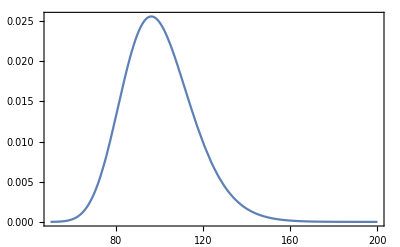

```mathematica
Plot[p[100,S1],{S1,50,200},PlotRange->All,Frame->True,AxesOrigin->{100,0}]
```

Figure 1

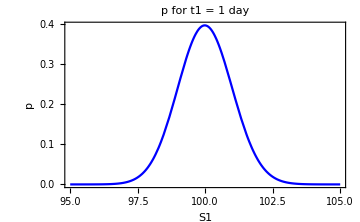

```mathematica
Plot[p[100,S1,1/252],{S1,95,105},PlotRange->All,Frame->True,AxesOrigin->{100,0},PlotStyle->Blue,FrameLabel->{Style[Framed["S1"],10],Style[Framed["p"],10]},PlotLabel->Style[Framed["p for t1 = 1 day"],12],ImageSize->Medium]
```

Figure 2

```mathematica
Plot3D[p[100,S1,t1,0.01/√(24 3600)],{S1,99.99,100.01},{t1,0.001,3},AxesLabel->{Style[Framed["S1"],12],Style[Framed["t1"],12],Style[Framed["p"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["p up to 3 seconds, truncated at S0=100"],14]]
```

General::munfl: Exp[-3556.57] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

## 3.2 A better idea for durations

Figure 3

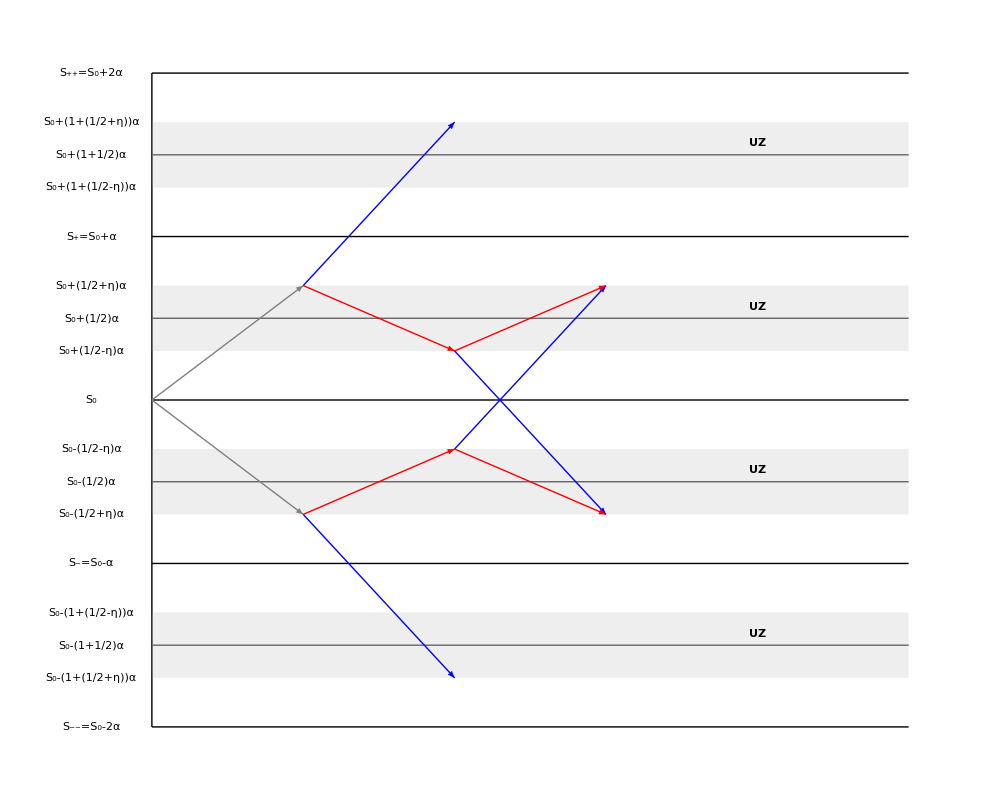

```mathematica
xlbl=-0.4;
eta=0.2;
Graphics[{Text[Style["S_0",Large],{xlbl,0}],Text[Style["S_+=S_0+α",Large],{xlbl,1}],Text[Style["S_(++)=S_0+2α",Large],{xlbl,2}],Text[Style["S_-=S_0-α",Large],{xlbl,-1}],Text[Style["S_(--)=S_0-2α",Large],{xlbl,-2}],
Text[Style["S_0+(1/2)α",Medium],{xlbl,1/2}],Text[Style["S_0+(1+1/2)α",Medium],{xlbl,1+1/2}],Text[Style["S_0-(1/2)α",Medium],{xlbl,-1/2}],Text[Style["S_0-(1+1/2)α",Medium],{xlbl,-1-1/2}],
Text[Style["S_0+(1/2+η)α",Medium],{xlbl,1/2+eta}],Text[Style["S_0+(1+(1/2+η))α",Medium],{xlbl,1+1/2+eta}],Text[Style["S_0-(1/2+η)α",Medium],{xlbl,-1/2-eta}],Text[Style["S_0-(1+(1/2+η))α",Medium],{xlbl,-1-1/2-eta}],
Text[Style["S_0+(1/2-η)α",Medium],{xlbl,1/2-eta}],Text[Style["S_0+(1+(1/2-η))α",Medium],{xlbl,1+1/2-eta}],Text[Style["S_0-(1/2-η)α",Medium],{xlbl,-1/2+eta}],Text[Style["S_0-(1+(1/2-η))α",Medium],{xlbl,-1-1/2+eta}],
Black,
Line[{{0,0},{5,0}}],Line[{{0,1},{5,1}}],Line[{{0,2},{5,2}}],Line[{{0,-1},{5,-1}}],Line[{{0,-2},{5,-2}}],Line[{{0,-2},{0,2}}],
Darker[Gray],
Line[{{0,1/2},{5,1/2}}],Line[{{0,1+1/2},{5,1+1/2}}],Line[{{0,-1+1/2},{5,-1+1/2}}],Line[{{0,-2+1/2},{5,-2+1/2}}],
Lighter[Gray],Opacity[0.2],
Rectangle[{0,1/2-eta},{5,1/2+eta}],Rectangle[{0,1+1/2-eta},{5,1+1/2+eta}],Rectangle[{0,-1+1/2-eta},{5,-1+1/2+eta}],Rectangle[{0,-2+1/2-eta},{5,-2+1/2+eta}],
Opacity[1],Gray,
Arrow[{{0,0},{1,1/2+eta}}],Arrow[{{0,0},{1,-1/2-eta}}],
Blue,
Arrow[{{1,1/2+eta},{2,1+1/2+eta}}],
Arrow[{{1,-1/2-eta},{2,-1-1/2-eta}}],
Red,
Arrow[{{1,1/2+eta},{2,1/2-eta}}],
Arrow[{{1,-1/2-eta},{2,-1/2+eta}}],
Blue,
Arrow[{{2,1/2-eta},{3,-1/2-eta}}],
Arrow[{{2,-1/2+eta},{3,1/2+eta}}],
Red,
Arrow[{{2,1/2-eta},{3,1/2+eta}}],
Arrow[{{2,-1/2+eta},{3,-1/2-eta}}],
Black,
Text[Style["UZ",Large,Bold],{4,1.57}],Text[Style["UZ",Large,Bold],{4,0.57}],Text[Style["UZ",Large,Bold],{4,-0.43}],Text[Style["UZ",Large,Bold],{4,-1.43}]},
ImageSize->{1000,800}]
```

```mathematica
Series[Log[1+(2η x)/(1-2η x)],{x,0,3}]
```

2 η x+2 η^2 x^2+(8 η^3 x^3)/3+O[x]^4

```mathematica
Series[Log[1+((1+2η) x)/(1-2η x)],{x,0,3}]
```

(1+2 η) x+1/2 (-1+4 η^2) x^2+1/3 (1+8 η^3) x^3+O[x]^4

```mathematica
2 η^2-1/2 (-1+4 η^2) ((2η)/(1+2η))
```

2 η^2-(η (-1+4 η^2))/(1+2 η)

```mathematica
Expand[2 η^2(1+2η)]
```

2 η^2+4 η^3

```mathematica
Expand[η (1-4 η^2)]
```

η-4 η^3

```mathematica
Series[Log[1+(2η x)/(1-2η x)]-Log[1+((1+2η) x)/(1-2η x)]((2η)/(1+2η)),{x,0,3}]
```

η x^2+2/3 (-η+2 η^2) x^3+O[x]^4

## 3.3 Not all durations are equal

### 3.3.1 Double-barrier hitting times

Equations

ω=μ-1/2 σ^2

x_0=Log[S_0]

x_T=Log[S_T]

b_±=Log[B_±]

nmv[x,m,v]:=(ⅇ^(-(x-m)^2/(2v)))/(√(2π v))

u[x,t]:=ⅇ^(α(x-x_0)+β t)p[x,t]

α=-ω/σ^2=-(μ/σ^2)+1/2

β=ω^2/(2 σ^2)=1/2(μ/σ-1/2 σ)^2=1/2(μ/σ)^2-1/2 2 μ/σ 1/2 σ+1/2 1/4 σ^2=1/2(μ/σ)^2-1/2 μ+1/8 σ^2=1/2(-μ α+1/4 σ^2)

p[x,t]:=ⅇ^(-α(x-x_0)-β t)u[x,t]

P_±[x,t]:=ⅇ^(ω/σ^2(b_±-x_0))∑_(n=1)^∞ (
(ⅇ^(ω/σ^2 y_n^±)𝒩[(y_n^±+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 y_n^±)𝒩[(y_n^±-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 z_n^±)𝒩[(z_n^±+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 z_n^±)𝒩[(z_n^±-ω t)/(σ √t)]))

y_n^±=±(2(n-1)b_∓-(2n-1)b_±+x_0)=±((2n-1)(b_∓-b_±)+x_0-b_∓)=±((2n-2)(b_∓-b_±)+x_0-b_∓+b_∓-b_±)=±(2(n-1)Log[(B_∓)/(B_±)]+Log[S_0/(B_±)])=±Log[S_0/(B_±)((B_∓)/(B_±))^(2(n-1))]

z_n^±=±(2n b_∓-(2n-1)b_±-x_0)=±((2n-1)(b_∓-b_±)-x_0+b_∓)=±((2n-1)(b_∓-b_±)-x_0+b_∓+b_∓-b_±)=±(2(n-1)Log[(B_∓)/(B_±)]+Log[(B_∓)^2/(S_0 B_±)])=±Log[(B_∓)^2/(S_0 B_±)((B_∓)/(B_±))^(2(n-1))]

ϕ_±[x,t]:=(∂P_±[x,t])/(∂t)

ϕ_±[x,t]:=ⅇ^(ω/σ^2(b_±-x_0))∑_(n=1)^∞ (
(ⅇ^(ω/σ^2 y_n^±)𝓃[(y_n^±+ω t)/(σ √t)](-y_n^±/(2σ t √t)+ω/(2σ √t))+ⅇ^(-ω/σ^2 y_n^±)𝓃[(y_n^±-ω t)/(σ √t)](-y_n^±/(2σ t √t)-ω/(2σ √t)))-
(ⅇ^(ω/σ^2 z_n^±)𝓃[(z_n^±+ω t)/(σ √t)](-z_n^±/(2σ t √t)+ω/(2σ √t))+ⅇ^(-ω/σ^2 z_n^±)𝓃[(z_n^±-ω t)/(σ √t)](-z_n^±/(2σ t √t)-ω/(2σ √t))))

ϕ_±[x,t]:=ⅇ^(ω/σ^2(b_±-x_0))∑_(n=1)^∞ (
(ⅇ^(ω/σ^2 y_n^±)𝓃[(y_n^±+ω t)/(σ √t)](-y_n^±/(2σ t √t)+(ω t)/(2σ t √t))+ⅇ^(-ω/σ^2 y_n^±)𝓃[(y_n^±-ω t)/(σ √t)](-y_n^±/(2σ t √t)-(ω t)/(2σ t √t)))-
(ⅇ^(ω/σ^2 z_n^±)𝓃[(z_n^±+ω t)/(σ √t)](-z_n^±/(2σ t √t)+(ω t)/(2σ t √t))+ⅇ^(-ω/σ^2 z_n^±)𝓃[(z_n^±-ω t)/(σ √t)](-z_n^±/(2σ t √t)-(ω t)/(2σ t √t))))

ϕ_±[x,t]:=(ⅇ^(μ/σ^2(b_±-x_0)))/(2t)∑_(n=1)^∞ (
(ⅇ^(ω/σ^2 y_n^±)𝓃[(y_n^±+ω t)/(σ √t)]((-y_n^±+ω t)/(σ √t))-ⅇ^(-ω/σ^2 y_n^±)𝓃[(y_n^±-ω t)/(σ √t)]((y_n^±+ω t)/(σ √t)))-
(ⅇ^(ω/σ^2 z_n^±)𝓃[(z_n^±+ω t)/(σ √t)]((-z_n^±+ω t)/(σ √t))-ⅇ^(-ω/σ^2 z_n^±)𝓃[(z_n^±-ω t)/(σ √t)]((z_n^±+ω t)/(σ √t))))

μ/σ^2(b_±-x_0)+ω/σ^2 y_n^±-1/2((y_n^±+ω t)/(σ √t))^2

```mathematica
FullSimplify[(μ-1/2 σ^2)/σ^2 Subscript[y, n]-1/2((Subscript[y, n]+(μ-1/2 σ^2) t)/(σ √t))^2]
```

-(t^2 (-2 μ+σ^2)^2+4 y_n^2)/(8 t σ^2)

```mathematica
FullSimplify[-(μ-1/2 σ^2)/σ^2 Subscript[y, n]-1/2((Subscript[y, n]-(μ-1/2 σ^2) t)/(σ √t))^2]
```

-(t^2 (-2 μ+σ^2)^2+4 y_n^2)/(8 t σ^2)

```mathematica
-(t^2 (-2 μ+σ^2)^2)/(8 t σ^2)-(4 Subscript[y, n]^2)/(8 t σ^2)
```

```mathematica
-1/2(((μ-1/2 σ^2)t)/(σ √t))^2-1/2(Subscript[y, n]/(σ √t))^2
```

```mathematica
Simplify[ⅇ^(±ω/σ^2 Log[x])]
```

x^(±ω/σ^2)

y_n^±=±Log[S_0/(B_±)((B_∓)/(B_±))^(2(n-1))]

z_n^±=±Log[(B_∓)^2/(S_0 B_±)((B_∓)/(B_±))^(2(n-1))]

ⅇ^(ω/σ^2(b_±-x_0))=((B_±)/S_0)^(ω/σ^2)

ⅇ^(±ω/σ^2 y_n^±)=(S_0/(B_±))^(±ω/σ^2)((B_∓)/(B_±))^(±2(n-1)ω/σ^2)

ⅇ^(±ω/σ^2 z_n^±)=((B_∓)^2/(S_0 B_±))^(±ω/σ^2)((B_∓)/(B_±))^(±2(n-1)ω/σ^2)

ϕ_±[x,t]:=((B_±)/S_0)^(ω/σ^2)(1/(2t))∑_(n=1)^∞ (
((S_0/(B_±))^(±ω/σ^2)((B_∓)/(B_±))^(±2(n-1)ω/σ^2)𝓃[(y_n^±+ω t)/(σ √t)]((-y_n^±+ω t)/(σ √t))-(S_0/(B_±))^(∓ω/σ^2)((B_∓)/(B_±))^(∓2(n-1)ω/σ^2)𝓃[(y_n^±-ω t)/(σ √t)]((y_n^±+ω t)/(σ √t)))-
(((B_∓)^2/(S_0 B_±))^(±ω/σ^2)((B_∓)/(B_±))^(±2(n-1)ω/σ^2)𝓃[(z_n^±+ω t)/(σ √t)]((-z_n^±+ω t)/(σ √t))-((B_∓)^2/(S_0 B_±))^(∓ω/σ^2)((B_∓)/(B_±))^(∓2(n-1)ω/σ^2)𝓃[(z_n^±-ω t)/(σ √t)]((z_n^±+ω t)/(σ √t))))

```mathematica
nn[z_?NumberQ]:=Exp[-(z^2)/2]/Sqrt[2 Pi]; 
nn[-∞]=0;
nn[+∞]=0;
nn::usage="nn[x] returns the pdf for the normal distribution n[x]";
```

```mathematica
ns[z_]:=Exp[-(z^2)/2]/Sqrt[2 Pi];
```

```mathematica
NN[z_?NumberQ]:=CDF[NormalDistribution[0,1]][z]; 
NN[-∞]=0;
NN[+∞]=1; 
NN::usage="NN[x] returns the cumulative normal N[x]";
```

```mathematica
nmaxd=2000;
```

```mathematica
ncdf[z_]:=1/2 Erfc[-z/(√2)];
```

Equation: CDF for hitting times

```mathematica
Ptup[S0_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=Module[{ω,x0,bu,bd},
If[t==0,0,
ω=μ-1/2 σ^2;
x0=Log[S0];
bu=Log[Bu];
bd=Log[Bd];
yn[n_]:=+1*(2*(n-1)*bd-(2n-1)*bu+x0);
zn[n_]:=+1*(2*n*bd-(2n-1)*bu-x0);
ⅇ^(ω/σ^2(bu-x0))Sum[Quiet[
(ⅇ^(ω/σ^2 yn[n])NN[(yn[n]+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn[n])NN[(yn[n]-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn[n])NN[(zn[n]+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn[n])NN[(zn[n]-ω t)/(σ √t)])],{n,1,nmax}]]];
```

```mathematica
Ptdown[S0_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=Module[{ω,x0,bu,bd},
If[t==0,0,
ω=μ-1/2 σ^2;
x0=Log[S0];
bu=Log[Bu];
bd=Log[Bd];
yn[n_]:=-1*(2*(n-1)*bu-(2n-1)*bd+x0);
zn[n_]:=-1*(2*n*bu-(2n-1)*bd-x0);
ⅇ^(ω/σ^2(bd-x0))Sum[Quiet[
(ⅇ^(ω/σ^2 yn[n])NN[(yn[n]+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn[n])NN[(yn[n]-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn[n])NN[(zn[n]+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn[n])NN[(zn[n]-ω t)/(σ √t)])],{n,1,nmax}]]];
```

```mathematica
Pt[sud_,ud_,s0_,α_,η_,σ_,μ_,t_]:=Module[{ω,x0,b1,b2,yn,zn,n=0,ans=0,ϵ=10^-10,pn=1},
If[t==0,0,
ω=μ-1/2 σ^2;
x0=Log[s0+sud(1/2-η)α];
b1=Log[s0+ud(1/2+η)α];
b2=Log[s0-ud(1/2+η)α];
While[pn>ϵ,
n++;
yn=+ud*(2*(n-1)*b2-(2n-1)*b1+x0);
zn=+ud*(2*n*b2-(2n-1)*b1-x0);
pn=
(ⅇ^(ω/σ^2 yn)ncdf[(yn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn)ncdf[(yn-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn)ncdf[(zn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn)ncdf[(zn-ω t)/(σ √t)]);
ans+=pn;]];
ⅇ^(ω/σ^2(b1-x0))ans];
```

```mathematica
Ptn[sud_,ud_,s0_,α_,η_,σ_,μ_,t_, nmax_:nmaxd]:=Module[{ω,x0,b1,b2,yn,zn},
If[t==0,0,
ω=μ-1/2 σ^2;
x0=Log[s0+sud(1/2-η)α];
b1=Log[s0+ud(1/2+η)α];
b2=Log[s0-ud(1/2+η)α];
ⅇ^(ω/σ^2(b1-x0))*Sum[Quiet[
yn=+ud*(2*(n-1)*b2-(2n-1)*b1+x0);
zn=+ud*(2*n*b2-(2n-1)*b1-x0);
(ⅇ^(ω/σ^2 yn)ncdf[(yn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn)ncdf[(yn-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn)ncdf[(zn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn)ncdf[(zn-ω t)/(σ √t)])],{n,1,nmax}]]];
```

```mathematica
Ptn[1,1,100,0.01,0.5,0.01,0,1,155]
```

0.5

```mathematica
Pt[1,1,100,0.01,0.5,0.01,0,1]
```

0.5

```mathematica
N[Pt[1,1,100,0.01,0.5,0.01,0,1],15]
```

0.5

```mathematica
Ptk[sud_,ud_,s0_,α_,η_,σ_,μ_,t_,k_:1]:=Module[{ω,x0,b1,b2,yn,zn,n=0,ans=0,ϵ=10^-10,pn=1},
If[t==0,0,
ω=μ-1/2 σ^2;
x0=Log[s0+sud(1/2-η)α];
b1=Log[s0+ud(1/2+η+(k-1))α];
b2=Log[s0-ud(1/2+η)α];
While[pn>ϵ,
n++;
yn=+ud*(2*(n-1)*b2-(2n-1)*b1+x0);
zn=+ud*(2*n*b2-(2n-1)*b1-x0);
pn=
(ⅇ^(ω/σ^2 yn)ncdf[(yn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn)ncdf[(yn-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn)ncdf[(zn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn)ncdf[(zn-ω t)/(σ √t)]);
ans+=pn;]];
ⅇ^(ω/σ^2(b1-x0))ans];
```

```mathematica
s=100;α=0.01;σ=0.01;μ=0;t=1;
Grid[Table[Grid[{{Ptk[-1,+1,s,α,η,σ,μ,t,k],Ptk[-1,+1,s,α k,η/k,σ,μ,t,1]},{Ptk[+1,-1,s,α,η,σ,μ,t,k],Ptk[+1,-1,s,α k,η/k,σ,μ,t,1]},{(2 η/k)/(1+2 η/k)}},Frame->All],{k,1,5},{η,0.1,0.5,0.1}],Frame->All]
```

0.166667 | 0.166667
0.166667 | 0.166667
0.166667 |  | 0.285714 | 0.285714
0.285714 | 0.285714
0.285714 |  | 0.375 | 0.375
0.375 | 0.375
0.375 |  | 0.444444 | 0.444444
0.444444 | 0.444444
0.444444 |  | 0.5 | 0.5
0.5 | 0.5
0.5 | 
0.0909091 | 0.0909091
0.0909091 | 0.0909091
0.0909091 |  | 0.166667 | 0.166667
0.166667 | 0.166667
0.166667 |  | 0.230769 | 0.230769
0.230769 | 0.230769
0.230769 |  | 0.285714 | 0.285714
0.285714 | 0.285714
0.285714 |  | 0.333333 | 0.333333
0.333333 | 0.333333
0.333333 | 
0.0625 | 0.0625
0.0625 | 0.0625
0.0625 |  | 0.117647 | 0.117647
0.117647 | 0.117647
0.117647 |  | 0.166667 | 0.166667
0.166667 | 0.166667
0.166667 |  | 0.210526 | 0.210526
0.210526 | 0.210526
0.210526 |  | 0.25 | 0.25
0.25 | 0.25
0.25 | 
0.047619 | 0.047619
0.047619 | 0.047619
0.047619 |  | 0.0909091 | 0.0909091
0.0909091 | 0.0909091
0.0909091 |  | 0.130435 | 0.130435
0.130435 | 0.130435
0.130435 |  | 0.166667 | 0.166667
0.166667 | 0.166667
0.166667 |  | 0.2 | 0.2
0.2 | 0.2
0.2 | 
0.0384615 | 0.0384615
0.0384615 | 0.0384615
0.0384615 |  | 0.0740741 | 0.0740741
0.0740741 | 0.0740741
0.0740741 |  | 0.107143 | 0.107143
0.107143 | 0.107143
0.107143 |  | 0.137931 | 0.137931
0.137931 | 0.137931
0.137931 |  | 0.166667 | 0.166667
0.166667 | 0.166667
0.166667 |

```mathematica
s=100;α=0.01;σ=0.01;μ=0;t=1;
Grid[Table[Grid[{{Ptk[-1,-1,s,α,η,σ,μ,t,k],Ptk[-1,-1,s,α,η+(k-1)/2,σ,μ,t,1]},{Ptk[+1,+1,s,α,η,σ,μ,t,k],Ptk[+1,+1,s,α,η+(k-1)/2,σ,μ,t,1]},{1/(1+2(η+(k-1)/2))}},Frame->All],{k,1,5},{η,0.1,0.5,0.1}],Frame->All]
```

0.833333 | 0.833333
0.833333 | 0.833333
0.833333 |  | 0.714286 | 0.714286
0.714286 | 0.714286
0.714286 |  | 0.625 | 0.625
0.625 | 0.625
0.625 |  | 0.555556 | 0.555556
0.555556 | 0.555556
0.555556 |  | 0.5 | 0.5
0.5 | 0.5
0.5 | 
0.454545 | 0.454545
0.454545 | 0.454545
0.454545 |  | 0.416667 | 0.416667
0.416667 | 0.416667
0.416667 |  | 0.384615 | 0.384615
0.384615 | 0.384615
0.384615 |  | 0.357143 | 0.357143
0.357143 | 0.357143
0.357143 |  | 0.333333 | 0.333333
0.333333 | 0.333333
0.333333 | 
0.3125 | 0.3125
0.3125 | 0.3125
0.3125 |  | 0.294118 | 0.294118
0.294118 | 0.294118
0.294118 |  | 0.277778 | 0.277778
0.277778 | 0.277778
0.277778 |  | 0.263158 | 0.263158
0.263158 | 0.263158
0.263158 |  | 0.25 | 0.25
0.25 | 0.25
0.25 | 
0.238095 | 0.238095
0.238095 | 0.238095
0.238095 |  | 0.227273 | 0.227273
0.227273 | 0.227273
0.227273 |  | 0.217391 | 0.217391
0.217391 | 0.217391
0.217391 |  | 0.208333 | 0.208333
0.208333 | 0.208333
0.208333 |  | 0.2 | 0.2
0.2 | 0.2
0.2 | 
0.192308 | 0.192308
0.192308 | 0.192308
0.192308 |  | 0.185185 | 0.185185
0.185185 | 0.185185
0.185185 |  | 0.178571 | 0.178571
0.178571 | 0.178571
0.178571 |  | 0.172414 | 0.172414
0.172414 | 0.172414
0.172414 |  | 0.166667 | 0.166667
0.166667 | 0.166667
0.166667 |

```mathematica
s=100;α=0.01;σ=0.01;μ=0;t=10^-4;
Grid[Table[Grid[{{Ptk[-1,+1,s,α,η,σ,μ,t,k],Ptk[-1,+1,s,α k,η/k,σ,μ,t,1]},{Ptk[+1,-1,s,α,η,σ,μ,t,k],Ptk[+1,-1,s,α k,η/k,σ,μ,t,1]}},Frame->All],{k,1,5},{η,0.1,0.5,0.1}],Frame->All]
```

0.156326 | 0.156326
0.156326 | 0.156326 | 0.245591 | 0.245591
0.24559 | 0.24559 | 0.289532 | 0.289532
0.289528 | 0.289528 | 0.307997 | 0.307997
0.307987 | 0.307987 | 0.31462 | 0.31462
0.314602 | 0.314602
0.0291108 | 0.0291053
0.0290996 | 0.029105 | 0.0403995 | 0.0403909
0.0403805 | 0.0403891 | 0.0441384 | 0.0441283
0.0441136 | 0.0441236 | 0.0451968 | 0.0451863
0.0451673 | 0.0451778 | 0.0454539 | 0.0454432
0.0454199 | 0.0454306
0.0020278 | 0.00202597
0.00202408 | 0.0020259 | 0.00255772 | 0.00255528
0.00255248 | 0.00255492 | 0.00267612 | 0.00267351
0.00267009 | 0.0026727 | 0.00269888 | 0.00269623
0.00269226 | 0.00269491 | 0.00270281 | 0.00270015
0.00269564 | 0.0026983
0.0000526474 | 0.0000525196
0.0000523876 | 0.0000525152 | 0.0000619206 | 0.0000617655
0.0000615914 | 0.0000617461 | 0.0000633228 | 0.0000631628
0.000062964 | 0.0000631236 | 0.0000635119 | 0.0000633512
0.0000631306 | 0.0000632909 | 0.0000635422 | 0.0000633814
0.0000631393 | 0.0000632996
5.09281×10^-7 | 5.06703×10^-7
5.04055×10^-7 | 5.06621×10^-7 | 5.69766×10^-7 | 5.66831×10^-7
5.63592×10^-7 | 5.66512×10^-7 | 5.76019×10^-7 | 5.73042×10^-7
5.69474×10^-7 | 5.72435×10^-7 | 5.76695×10^-7 | 5.73713×10^-7
5.69846×10^-7 | 5.7281×10^-7 | 5.76884×10^-7 | 5.73901×10^-7
5.69737×10^-7 | 5.72701×10^-7

```mathematica
s=100;α=0.01;σ=0.01;μ=0;t=10^-4;
Grid[Table[Grid[{{Ptk[-1,-1,s,α,η,σ,μ,t,k],Ptk[-1,-1,s,α,η+(k-1)/2,σ,μ,t,1]},{Ptk[+1,+1,s,α,η,σ,μ,t,k],Ptk[+1,+1,s,α,η+(k-1)/2,σ,μ,t,1]}},Frame->All],{k,1,5},{η,0.1,0.5,0.1}],Frame->All]
```

0.822992 | 0.822992
0.822993 | 0.822993 | 0.674133 | 0.674133
0.674138 | 0.674138 | 0.539324 | 0.539324
0.539333 | 0.539333 | 0.418604 | 0.418604
0.418618 | 0.418618 | 0.314602 | 0.314602
0.31462 | 0.31462
0.228733 | 0.228755
0.228797 | 0.228775 | 0.160809 | 0.16083
0.16087 | 0.160849 | 0.109254 | 0.109271
0.109307 | 0.109289 | 0.071694 | 0.0717081
0.0717379 | 0.0717238 | 0.0454199 | 0.0454306
0.0454539 | 0.0454432
0.0277599 | 0.0277754
0.0278005 | 0.027785 | 0.0163701 | 0.0163808
0.0163984 | 0.0163877 | 0.00930878 | 0.00931583
0.00932753 | 0.00932047 | 0.00510274 | 0.00510717
0.00511461 | 0.00511018 | 0.00269564 | 0.0026983
0.00270281 | 0.00270015
0.00137125 | 0.00137353
0.00137691 | 0.00137462 | 0.000672232 | 0.000673487
0.000675354 | 0.000674096 | 0.000317373 | 0.000318033
0.00031902 | 0.000318359 | 0.000144274 | 0.000144606
0.000145106 | 0.000144773 | 0.0000631393 | 0.0000632996
0.0000635422 | 0.0000633814
0.000026573 | 0.0000266718
0.0000268093 | 0.0000267101 | 0.0000107725 | 0.0000108163
0.0000108775 | 0.0000108335 | 4.20257×10^-6 | 4.22117×10^-6
4.24727×10^-6 | 4.22856×10^-6 | 1.57754×10^-6 | 1.58513×10^-6
1.59579×10^-6 | 1.58817×10^-6 | 5.69737×10^-7 | 5.72701×10^-7
5.76884×10^-7 | 5.73901×10^-7

Co Up Pt[-1,+1,s,α k,η/k,σ,μ,t]
Co Down Pt[+1,-1,s,α k,η/k,σ,μ,t]
Al Down Pt[-1,-1,s,α,η+(k-1)/2,σ,μ,t]
Al Up Pt[+1,+1,s,α,η+(k-1)/2,σ,μ,t]

```mathematica
multlikel[pw_,x_]:=Factorial[Total[x]]/Apply[Times,Map[Factorial,x]] Apply[Times,MapThread[Power,{pw,x}]];
```

```mathematica
prior={1/3,1/3,1/6,1/6};
```

```mathematica
FrobeniusSolve[{1,1,1,1},4]
```

{{0,0,0,4},{0,0,1,3},{0,0,2,2},{0,0,3,1},{0,0,4,0},{0,1,0,3},{0,1,1,2},{0,1,2,1},{0,1,3,0},{0,2,0,2},{0,2,1,1},{0,2,2,0},{0,3,0,1},{0,3,1,0},{0,4,0,0},{1,0,0,3},{1,0,1,2},{1,0,2,1},{1,0,3,0},{1,1,0,2},{1,1,1,1},{1,1,2,0},{1,2,0,1},{1,2,1,0},{1,3,0,0},{2,0,0,2},{2,0,1,1},{2,0,2,0},{2,1,0,1},{2,1,1,0},{2,2,0,0},{3,0,0,1},{3,0,1,0},{3,1,0,0},{4,0,0,0}}

```mathematica
N[Map[multlikel[prior,#]&,FrobeniusSolve[{1,1,1,1},4]]]
```

{0.000771605,0.00308642,0.00462963,0.00308642,0.000771605,0.00617284,0.0185185,0.0185185,0.00617284,0.0185185,0.037037,0.0185185,0.0246914,0.0246914,0.0123457,0.00617284,0.0185185,0.0185185,0.00617284,0.037037,0.0740741,0.037037,0.0740741,0.0740741,0.0493827,0.0185185,0.037037,0.0185185,0.0740741,0.0740741,0.0740741,0.0246914,0.0246914,0.0493827,0.0123457}

```mathematica
N[Map[multlikelnl[prior,#]&,FrobeniusSolve[{1,1,1,1},4]]]
```

{0.000771605,0.00308642,0.00462963,0.00308642,0.000771605,0.00617284,0.0185185,0.0185185,0.00617284,0.0185185,0.037037,0.0185185,0.0246914,0.0246914,0.0123457,0.00617284,0.0185185,0.0185185,0.00617284,0.037037,0.0740741,0.037037,0.0740741,0.0740741,0.0493827,0.0185185,0.037037,0.0185185,0.0740741,0.0740741,0.0740741,0.0246914,0.0246914,0.0493827,0.0123457}

```mathematica
Total[Map[multlikel[prior,#]&,FrobeniusSolve[{1,1,1,1},4]]]
```

1

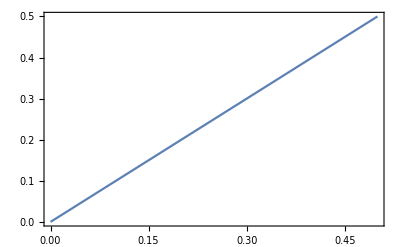

```mathematica
Plot[multlikel[{x,x,1/2-x,1/2-x},{1,0,0,0}],{x,0,1/2},Frame->True,PlotRange->All]
```

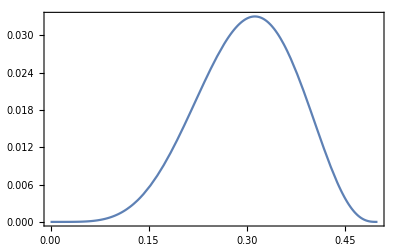

```mathematica
Plot[multlikel[{x,x,1/2-x,1/2-x},{3,2,1,2}],{x,0,1/2},Frame->True,PlotRange->All]
```

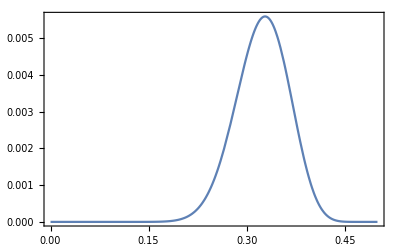

```mathematica
Plot[multlikel[{x,x,1/2-x,1/2-x},{10,11,5,6}],{x,0,1/2},Frame->True,PlotRange->All]
```

General::munfl: 2.10029×10^-175 2.10029×10^-175 is too small to represent as a normalized machine number; precision may be lost.

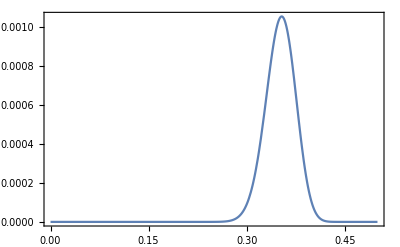

```mathematica
Plot[multlikel[{x,x,1/2-x,1/2-x},{35,35,16,13}],{x,0,1/2},Frame->True,PlotRange->All]
```

```mathematica
Plot3D[multlikelnl[{η,η,1/2-η+μ/5,1/2-η-μ/5},{35,35,16,13}],{η,0,1/2},{μ,-0.10,+0.10},PlotRange->All,AxesLabel->Automatic]
```

General::munfl: 2.31559×10^-156 2.31559×10^-156 is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
prior2={0.4,0.3,0.2,0.1};
```

```mathematica
multlikel[prior2,{4,3,2,1}]
```

0.0348365

```mathematica
multloglikel[pw_,x_]:=N[{Log[Factorial[Total[x]]], Log[Apply[Times,Map[Factorial,x]]], Log[Apply[Times,MapThread[Power,{pw,x}]]]}];
```

```mathematica
multloglikel[prior2,{4,3,2,1}]
```

{15.1044,5.66296,-12.7985}

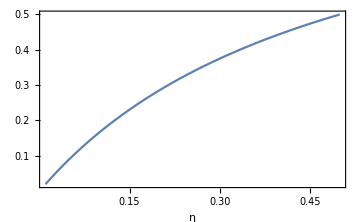

```mathematica
Module[{sud=-1,ud=+1 ,k=1,s=100, α=0.01,σ=0.01,μ=0,t=1},
Plot[Pt[sud,ud,s,α k,η/k,σ,μ,t],{η,0.01,0.5},Frame->True,
PlotRange->All,ImageSize->Medium,FrameLabel->Automatic,PlotLegends->Automatic]]
```

```mathematica
Module[{sud=-1,ud=+1 ,k=1,s=100, α=0.01,μ=0,t=1},
Plot3D[Pt[sud,ud,s,α k,η/k,σ,μ,t],{η,0.01,0.5},{σ,0.01,0.2},
PlotRange->All,ImageSize->Medium,AxesLabel->Automatic,PlotLegends->Automatic]]
```

-Graphics3D-

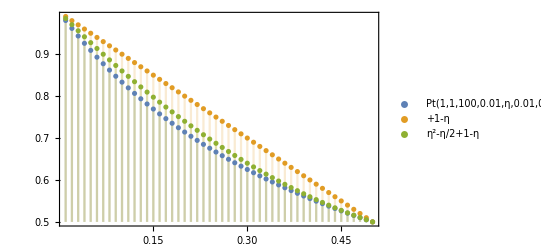

```mathematica
DiscretePlot[{Pt[1,1,100,0.01,η,0.01,0,1],+1-η,η^2-η/2+1-η},{η,0.01,0.50,0.01},Frame->True,PlotRange->All,PlotLegends->"Expressions"]
```

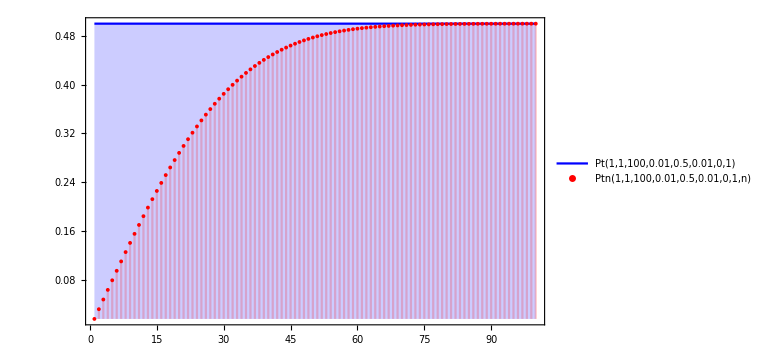

```mathematica
DiscretePlot[{Pt[1,1,100,0.01,0.5,0.01,0,1],Ptn[1,1,100,0.01,0.5,0.01,0,1,n]},{n,1,100},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->"Expressions",Joined->{True,False},ImageSize->Large]
```

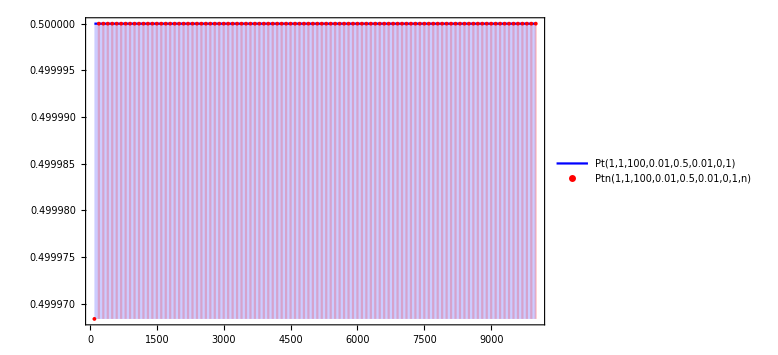

```mathematica
DiscretePlot[{Pt[1,1,100,0.01,0.5,0.01,0,1],Ptn[1,1,100,0.01,0.5,0.01,0,1,n]},{n,100,10001,100},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->"Expressions",Joined->{True,False},ImageSize->Large]
```

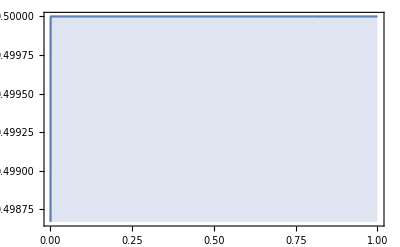

```mathematica
DiscretePlot[Pt[1,1,100,0.01,0.5,0.01,0,t],{t,5 10^-4,10^0,10^-4},PlotRange->All,Frame->True]
```

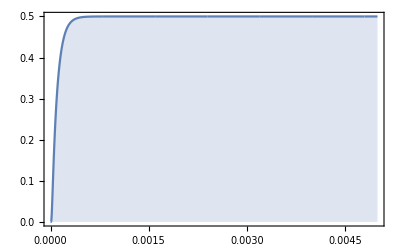

```mathematica
DiscretePlot[Pt[1,1,100,0.01,0.5,0.01,0,t],{t,0,5 10^-3,10^-7},PlotRange->All,Frame->True]
```

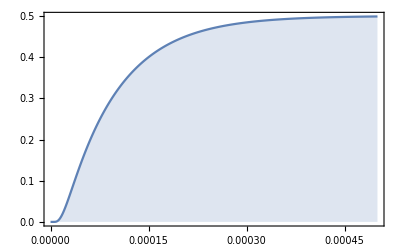

```mathematica
DiscretePlot[Pt[1,1,100,0.01,0.5,0.01,0,t],{t,0,5 10^-4,10^-7},PlotRange->All,Frame->True]
```

```mathematica
paupt1=Pt[1,1,100,0.01,0.5,0.01,0,1]
```

0.5

```mathematica
Pt[1,1,100,0.01,0.5,0.01,0,5 10^-4]/paupt001
```

0.997449

```mathematica
getpdf[cdf_]:=Module[{tcdf=Transpose[cdf]},Transpose[{Rest[First[tcdf]],Differences[Last[tcdf]]}]];
```

```mathematica
getscaledpdf[cdf_]:=Module[{tcdf=Transpose[cdf]},Transpose[{Rest[First[tcdf]],Differences[Last[tcdf]]/Differences[First[tcdf]]}]];
```

```mathematica
Refine[PDF[InverseGaussianDistribution[μ,λ],x],x>0]
```

(ⅇ^(-(λ (x-μ)^2)/(2 x μ^2)) √λ)/(√(2 π) x^(3/2))

```mathematica
Refine[CDF[InverseGaussianDistribution[μ,λ],x],x>0]
```

1/2 Erfc[(√λ (-x+μ))/(√2 √x μ)]+1/2 ⅇ^((2 λ)/μ) Erfc[(√λ (x+μ))/(√2 √x μ)]

```mathematica
Refine[PDF[InverseGaussianDistribution[μ,λ,θ],x],x>0]
```

(ⅇ^(-(λ (1+x^2/μ^2))/(2 x)) x^(-1+θ) μ^-θ)/(2 BesselK[θ,λ/μ])

```mathematica
Refine[PDF[InverseGaussianDistribution[μ,λ,0],x],x>0]
```

(ⅇ^(-(λ (1+x^2/μ^2))/(2 x)))/(2 x BesselK[0,λ/μ])

```mathematica
Refine[PDF[InverseGaussianDistribution[μ,1],x],x>0]
```

(ⅇ^(-(x-μ)^2/(2 x μ^2)))/(√(2 π) x^(3/2))

```mathematica
Mean[InverseGaussianDistribution[μ,λ,θ]]
```

(μ BesselK[1+θ,λ/μ])/BesselK[θ,λ/μ]

```mathematica
gigmean[{μ_,λ_,θ_}]:=(μ BesselK[1+θ,λ/μ])/BesselK[θ,λ/μ];
```

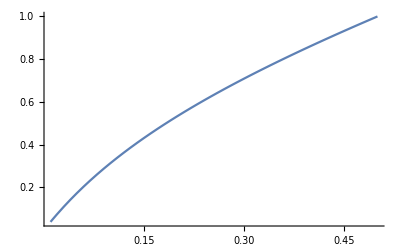

```mathematica
Plot[(2+2η)/3/((1+4η)/(6η)),{η,0.01,0.5},PlotRange->All]
```

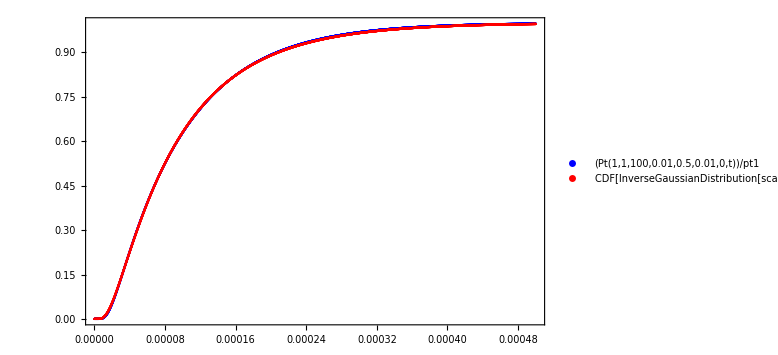

```mathematica
pt1=Pt[1,1,100,0.01,0.5,0.01,0,1 10^0];
p=0.371;b=1.166;scale=1.17 0.5 (0.01/(100 0.01))^2;
DiscretePlot[{Pt[1,1,100,0.01,0.5,0.01,0,t]/pt1,CDF[InverseGaussianDistribution[scale,b scale,p]][t]},{t,0,5 10^-4,1 10^-7},
PlotRange->{{0,5 10^-4},All},Frame->True,Filling->None,PlotStyle->{Blue,Red},ImageSize->Large,PlotLegends->"Expressions"]
```

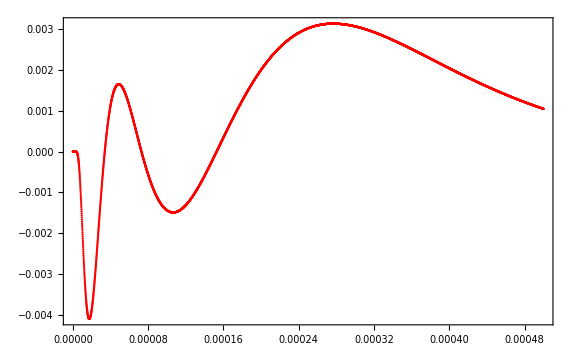

```mathematica
pt1=Pt[1,1,100,0.01,0.5,0.01,0,1 10^0];
p=0.371;b=1.166;scale=1.17 0.5 (0.01/(100 0.01))^2;
DiscretePlot[Pt[1,1,100,0.01,0.5,0.01,0,t]/pt1-CDF[InverseGaussianDistribution[scale,b scale,p]][t],{t,0,5 10^-4,1 10^-7},
PlotRange->{{0,5 10^-4},All},Frame->True,Filling->None,PlotStyle->{Red},ImageSize->Large]
```

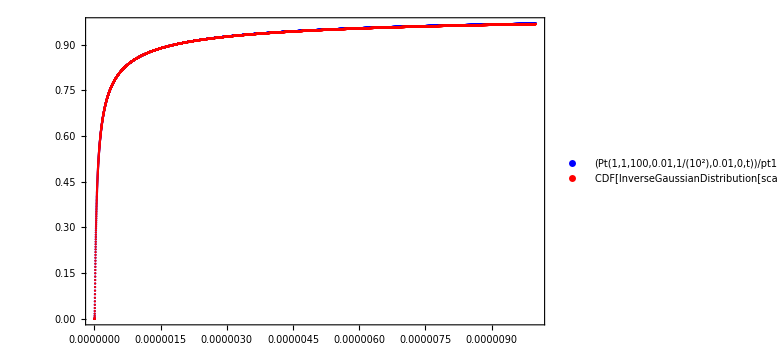

```mathematica
pt1=Pt[1,1,100,0.01,10^-2,0.01,0,1 10^0];
p=-0.4984;b=0.0215;scale=1.857 10^-2(0.01/(100 0.01))^2;
DiscretePlot[{Pt[1,1,100,0.01,10^-2,0.01,0,t]/pt1,CDF[InverseGaussianDistribution[scale,b scale,p]][t]},{t,0,1 10^-5,1 10^-9},
PlotRange->{{0,1 10^-5},All},Frame->True,Filling->None,PlotStyle->{Blue,Red},ImageSize->Large,PlotLegends->"Expressions"]
```

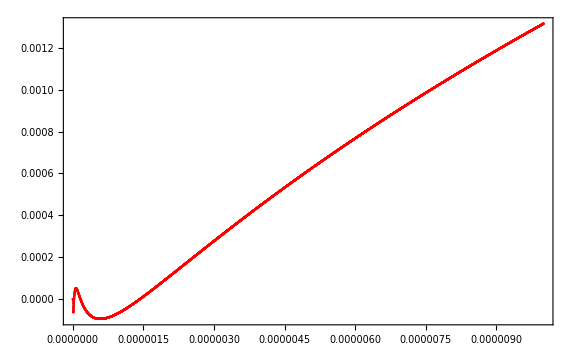

```mathematica
pt1=Pt[1,1,100,0.01,10^-2,0.01,0,1 10^0];
p=-0.4984;b=0.0215;scale=1.857 10^-2(0.01/(100 0.01))^2;
DiscretePlot[Pt[1,1,100,0.01,10^-2,0.01,0,t]/pt1-CDF[InverseGaussianDistribution[scale,b scale,p]][t],{t,0,1 10^-5,1 10^-9},
PlotRange->{{0,1 10^-5},All},Frame->True,Filling->None,PlotStyle->{Red},ImageSize->Large]
```

```mathematica
header={"ud","sud", "s0","s","α","η","σ","μ","dist","p","b","scale","adj","scale_adj", "mean","adj_mean"};
```

```mathematica
chgetaAUp = Transpose[Rest[Import["/Users/marcoscscarreira/My Papers/UZModelUncertainty/chg_eta_A_Up.csv"]]];
chgetaADown = Transpose[Rest[Import["/Users/marcoscscarreira/My Papers/UZModelUncertainty/chg_eta_A_Down.csv"]]];
chgetaCUp = Transpose[Rest[Import["/Users/marcoscscarreira/My Papers/UZModelUncertainty/chg_eta_C_Up.csv"]]];
chgetaCDown = Transpose[Rest[Import["/Users/marcoscscarreira/My Papers/UZModelUncertainty/chg_eta_C_Down.csv"]]];
```

```mathematica
buildtables[data_,legends_:True]:=Module[{
ηs=data⟦6⟧,ps=data⟦10⟧,bs=data⟦11⟧,scales=data⟦12⟧,adjs=data⟦13⟧,scaleadjs=data⟦14⟧,mean=data⟦15⟧,adjmean=data⟦16⟧,
θs,λs,μs,p,b,scaleadj,θ,λ,μ,am},
θs=ps;λs=bs scales;μs=scales;
p=Transpose[{ηs,ps}];
b=Transpose[{ηs,bs}];
scaleadj=Transpose[{ηs,scaleadjs}];
θ=Transpose[{ηs,θs}];
λ=Transpose[{ηs,λs}];
μ=Transpose[{ηs,μs}];
am=Transpose[{ηs,adjmean}];
ListLinePlot[{p,b,scaleadj,am},Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->If[legends,{"p", "b", "scale_adj", "adj_mean"},None]]];
```

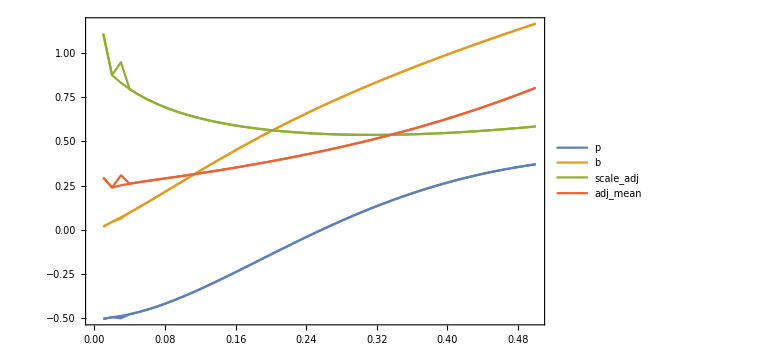

```mathematica
g1=buildtables[chgetaAUp];
g2=buildtables[chgetaADown,False];
Show[g1,g2]
```

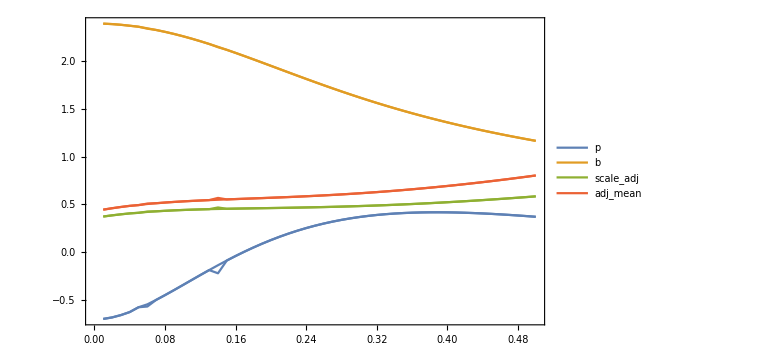

```mathematica
g1=buildtables[chgetaCUp];
g2=buildtables[chgetaCDown,False];
Show[g1,g2]
```

```mathematica
PTset[S_,α_,η_,σ_,μ_,t_]:=Module[{ω,x0u,x0d,bu,bd,ynu,znu,ynd,znd,n=0,ansau=0,ansad=0,ϵ=10^-10,pnau=1,pnad=1},
If[t==0,0,
ω=μ-1/2 σ^2;
x0u=Log[S+(1/2-η)α];
x0d=Log[S-(1/2-η)α];
bu=Log[S+(1/2+η)α];
bd=Log[S-(1/2+η)α];
While[Max[pnau,pnad]>ϵ,
n++;
ynu=+1*(2*(n-1)*bd-(2n-1)*bu+x0u);
znu=+1*(2*n*bd-(2n-1)*bu-x0u);
ynd=-1*(2*(n-1)*bu-(2n-1)*bd+x0d);
znd=-1*(2*n*bu-(2n-1)*bd-x0d);
pnau=
ⅇ^(ω/σ^2(bu-x0u))((ⅇ^(ω/σ^2 ynu)ncdf[(ynu+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 ynu)ncdf[(ynu-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 znu)ncdf[(znu+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 znu)ncdf[(znu-ω t)/(σ √t)]));
pnad=
ⅇ^(ω/σ^2(bd-x0d))((ⅇ^(ω/σ^2 ynd)ncdf[(ynd+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 ynd)ncdf[(ynd-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 znd)ncdf[(znd+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 znd)ncdf[(znd-ω t)/(σ √t)]));
ansau+=pnau;ansad+=pnad;]];
{{{ansau,1-ansau},{1-ansad,ansad}},{{(ansau ansad)/(ansau+ ansad),((1-ansau )ansad)/(ansau+ ansad)},{(ansau(1- ansad))/(ansau+ ansad),(ansau ansad)/(ansau+ ansad)}}}];
```

```mathematica
PTUp[S_,α_,η_,σ_,μ_,t_]:=Module[{ω,x0u,x0d,bu,bd,ynu,znu,ynd,znd,n=0,ansau=0,ansad=0,ϵ=10^-10,pnau=1,pnad=1},
If[t==0,0,
ω=μ-1/2 σ^2;
x0u=Log[S+(1/2-η)α];
x0d=Log[S-(1/2-η)α];
bu=Log[S+(1/2+η)α];
bd=Log[S-(1/2+η)α];
While[Max[pnau,pnad]>ϵ,
n++;
ynu=+1*(2*(n-1)*bd-(2n-1)*bu+x0u);
znu=+1*(2*n*bd-(2n-1)*bu-x0u);
ynd=-1*(2*(n-1)*bu-(2n-1)*bd+x0d);
znd=-1*(2*n*bu-(2n-1)*bd-x0d);
pnau=
ⅇ^(ω/σ^2(bu-x0u))((ⅇ^(ω/σ^2 ynu)ncdf[(ynu+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 ynu)ncdf[(ynu-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 znu)ncdf[(znu+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 znu)ncdf[(znu-ω t)/(σ √t)]));
pnad=
ⅇ^(ω/σ^2(bd-x0d))((ⅇ^(ω/σ^2 ynd)ncdf[(ynd+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 ynd)ncdf[(ynd-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 znd)ncdf[(znd+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 znd)ncdf[(znd-ω t)/(σ √t)]));
ansau+=pnau;ansad+=pnad;]];
(ansau ansad)/(ansau+ ansad)ansau+(ansau(1- ansad))/(ansau+ ansad)(1-ansad)];
```

```mathematica
PTSumC[S_,α_,η_,σ_,μ_,t_]:=Module[{ω,x0u,x0d,bu,bd,ynu,znu,ynd,znd,n=0,ansau=0,ansad=0,ϵ=10^-10,pnau=1,pnad=1},
If[t==0,0,
ω=μ-1/2 σ^2;
x0u=Log[S+(1/2-η)α];
x0d=Log[S-(1/2-η)α];
bu=Log[S+(1/2+η)α];
bd=Log[S-(1/2+η)α];
While[Max[pnau,pnad]>ϵ,
n++;
ynu=+1*(2*(n-1)*bd-(2n-1)*bu+x0u);
znu=+1*(2*n*bd-(2n-1)*bu-x0u);
ynd=-1*(2*(n-1)*bu-(2n-1)*bd+x0d);
znd=-1*(2*n*bu-(2n-1)*bd-x0d);
pnau=
ⅇ^(ω/σ^2(bu-x0u))((ⅇ^(ω/σ^2 ynu)ncdf[(ynu+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 ynu)ncdf[(ynu-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 znu)ncdf[(znu+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 znu)ncdf[(znu-ω t)/(σ √t)]));
pnad=
ⅇ^(ω/σ^2(bd-x0d))((ⅇ^(ω/σ^2 ynd)ncdf[(ynd+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 ynd)ncdf[(ynd-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 znd)ncdf[(znd+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 znd)ncdf[(znd-ω t)/(σ √t)]));
ansau+=pnau;ansad+=pnad;]];
((1-ansau )ansad)/(ansau+ ansad)+(ansau(1- ansad))/(ansau+ ansad)];
```

```mathematica
Ptup[100+(1/2-0.3)0.01,100+(1/2+0.3)0.01,100-(1/2+0.3)0.01,0.01/(√(24 3600)),3,0,20]
```

0.308572

```mathematica
Ptup[100+(1/2-0.3)0.01,100+(1/2+0.3)0.01,100-(1/2+0.3)0.01,0.01,3/(24 3600),0,20]
```

0.308572

```mathematica
Ptdown[100-(1/2-0.3)0.01,100+(1/2+0.3)0.01,100-(1/2+0.3)0.01,0.01,3/(24 3600),0,20]
```

0.308542

```mathematica
DiscretePlot3D[PTSumC[100,0.01,η,σ,0,1],{η,0.01,0.50,0.01},{σ,0.001,0.031, 0.001},AxesLabel->Automatic,ImageSize->Large,ViewPoint->{-2.9,-1.35,1.2}]
```

-Graphics3D-

```mathematica
DiscretePlot3D[PTSumC[100,0.01,η,σ,0.2,1],{η,0.01,0.50,0.01},{σ,0.001,0.031, 0.001},AxesLabel->Automatic,ImageSize->Large,ViewPoint->{-2.9266275383190408,1.005143127707287,1.3691378837704562}]
```

-Graphics3D-

```mathematica
DiscretePlot3D[PTSumC[100,0.01,η,σ,0.4,1],{η,0.01,0.50,0.01},{σ,0.001,0.031, 0.001},AxesLabel->Automatic,ImageSize->Large,ViewPoint->{-2.9266275383190408,1.005143127707287,1.3691378837704562}]
```

-Graphics3D-

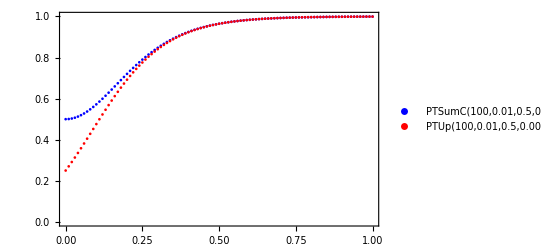

```mathematica
DiscretePlot[{PTSumC[100,0.01,0.5,0.005,μ,1],PTUp[100,0.01,0.5,0.005,μ,1]},
{μ,0,1,0.01},Frame->True,PlotRange->{{0,1},{0,1}},Filling->None,
PlotStyle->{Blue,Red},PlotLegends->"Expressions"]
```

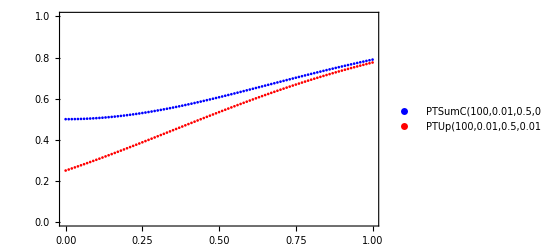

```mathematica
DiscretePlot[{PTSumC[100,0.01,0.5,0.01,μ,1],PTUp[100,0.01,0.5,0.01,μ,1]},
{μ,0,1,0.01},Frame->True,PlotRange->{{0,1},{0,1}},Filling->None,
PlotStyle->{Blue,Red},PlotLegends->"Expressions"]
```

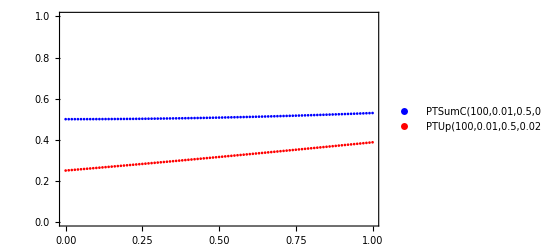

```mathematica
DiscretePlot[{PTSumC[100,0.01,0.5,0.02,μ,1],PTUp[100,0.01,0.5,0.02,μ,1]},
{μ,0,1,0.01},Frame->True,PlotRange->{{0,1},{0,1}},Filling->None,
PlotStyle->{Blue,Red},PlotLegends->"Expressions"]
```

```mathematica
tblCo=Table[{100,10^Subscript[α, e],η,10^Subscript[σ, e],μ,PTSumC[100,10^Subscript[α, e],η,10^Subscript[σ, e],μ,1],PTCup[100,10^Subscript[α, e],η,10^Subscript[σ, e],μ,1]},
{Subscript[α, e],-2,-2},{η,0.1,0.5,0.2},{Subscript[σ, e],-3,-1},{μ,0,1,0.2}];
```

```mathematica
Grid[N[Partition[Flatten[tblCo],7]]]
```

100. | 0.01 | 0.1 | 0.001 | 0. | 0.166667 | 0.0833333
100. | 0.01 | 0.1 | 0.001 | 0.2 | 0.99933 | 0.99933
100. | 0.01 | 0.1 | 0.001 | 0.4 | 1. | 1.
100. | 0.01 | 0.1 | 0.001 | 0.6 | 1. | 1.
100. | 0.01 | 0.1 | 0.001 | 0.8 | 1. | 1.
100. | 0.01 | 0.1 | 0.001 | 1. | 1. | 1.
100. | 0.01 | 0.1 | 0.01 | 0. | 0.166667 | 0.0833333
100. | 0.01 | 0.1 | 0.01 | 0.2 | 0.169764 | 0.104872
100. | 0.01 | 0.1 | 0.01 | 0.4 | 0.178894 | 0.129362
100. | 0.01 | 0.1 | 0.01 | 0.6 | 0.193591 | 0.15651
100. | 0.01 | 0.1 | 0.01 | 0.8 | 0.21316 | 0.185905
100. | 0.01 | 0.1 | 0.01 | 1. | 0.236762 | 0.21707
100. | 0.01 | 0.1 | 0.1 | 0. | 0.166667 | 0.0833333
100. | 0.01 | 0.1 | 0.1 | 0.2 | 0.166667 | 0.0835335
100. | 0.01 | 0.1 | 0.1 | 0.4 | 0.166668 | 0.083734
100. | 0.01 | 0.1 | 0.1 | 0.6 | 0.166669 | 0.0839347
100. | 0.01 | 0.1 | 0.1 | 0.8 | 0.166672 | 0.0841358
100. | 0.01 | 0.1 | 0.1 | 1. | 0.166674 | 0.0843372
100. | 0.01 | 0.3 | 0.001 | 0. | 0.375 | 0.1875
100. | 0.01 | 0.3 | 0.001 | 0.2 | 1. | 1.
100. | 0.01 | 0.3 | 0.001 | 0.4 | 1. | 1.
100. | 0.01 | 0.3 | 0.001 | 0.6 | 1. | 1.
100. | 0.01 | 0.3 | 0.001 | 0.8 | 1. | 1.
100. | 0.01 | 0.3 | 0.001 | 1. | 1. | 1.
100. | 0.01 | 0.3 | 0.01 | 0. | 0.375 | 0.1875
100. | 0.01 | 0.3 | 0.01 | 0.2 | 0.385864 | 0.252646
100. | 0.01 | 0.3 | 0.01 | 0.4 | 0.416882 | 0.32619
100. | 0.01 | 0.3 | 0.01 | 0.6 | 0.463827 | 0.404522
100. | 0.01 | 0.3 | 0.01 | 0.8 | 0.521022 | 0.483635
100. | 0.01 | 0.3 | 0.01 | 1. | 0.582699 | 0.559877
100. | 0.01 | 0.3 | 0.1 | 0. | 0.375 | 0.1875
100. | 0.01 | 0.3 | 0.1 | 0.2 | 0.375001 | 0.188101
100. | 0.01 | 0.3 | 0.1 | 0.4 | 0.375004 | 0.188702
100. | 0.01 | 0.3 | 0.1 | 0.6 | 0.37501 | 0.189305
100. | 0.01 | 0.3 | 0.1 | 0.8 | 0.375018 | 0.189909
100. | 0.01 | 0.3 | 0.1 | 1. | 0.375028 | 0.190514
100. | 0.01 | 0.5 | 0.001 | 0. | 0.5 | 0.25
100. | 0.01 | 0.5 | 0.001 | 0.2 | 1. | 1.
100. | 0.01 | 0.5 | 0.001 | 0.4 | 1. | 1.
100. | 0.01 | 0.5 | 0.001 | 0.6 | 1. | 1.
100. | 0.01 | 0.5 | 0.001 | 0.8 | 1. | 1.
100. | 0.01 | 0.5 | 0.001 | 1. | 1. | 1.
100. | 0.01 | 0.5 | 0.01 | 0. | 0.5 | 0.25
100. | 0.01 | 0.5 | 0.01 | 0.2 | 0.519479 | 0.358427
100. | 0.01 | 0.5 | 0.01 | 0.4 | 0.572181 | 0.476066
100. | 0.01 | 0.5 | 0.01 | 0.6 | 0.644213 | 0.590634
100. | 0.01 | 0.5 | 0.01 | 0.8 | 0.720476 | 0.692259
100. | 0.01 | 0.5 | 0.01 | 1. | 0.790018 | 0.775809
100. | 0.01 | 0.5 | 0.1 | 0. | 0.5 | 0.25
100. | 0.01 | 0.5 | 0.1 | 0.2 | 0.500002 | 0.251001
100. | 0.01 | 0.5 | 0.1 | 0.4 | 0.500008 | 0.252004
100. | 0.01 | 0.5 | 0.1 | 0.6 | 0.500018 | 0.253009
100. | 0.01 | 0.5 | 0.1 | 0.8 | 0.500032 | 0.254016
100. | 0.01 | 0.5 | 0.1 | 1. | 0.50005 | 0.255025

```mathematica
Map[Grid,PTset[100,0.01,0.5,0.01,0,1]]
```

{0.5 | 0.5
0.5 | 0.5,0.25 | 0.25
0.25 | 0.25}

```mathematica
Map[Grid,PTset[100,0.01,0.5,0.02,0,1]]
```

{0.5 | 0.5
0.5 | 0.5,0.25 | 0.25
0.25 | 0.25}

```mathematica
Map[Grid,PTset[100,0.01,0.3,0.01,0,1]]
```

{0.625 | 0.375
0.375 | 0.625,0.3125 | 0.1875
0.1875 | 0.3125}

```mathematica
Map[Grid,PTset[100,0.01,0.2,0.01,0,1]]
```

{0.714286 | 0.285714
0.285714 | 0.714286,0.357143 | 0.142857
0.142857 | 0.357143}

```mathematica
Map[Grid,PTset[100,0.01,0.3,0.02,0,1]]
```

{0.625 | 0.375
0.375 | 0.625,0.3125 | 0.1875
0.1875 | 0.3125}

```mathematica
Map[Grid,PTset[100,0.01,0.3,0.01,0.2,1]]
```

{0.697429 | 0.302571
0.451384 | 0.548616,0.307068 | 0.133218
0.252646 | 0.307068}

```mathematica
Map[Grid,PTset[100,0.01,0.3,0.02,0.2,1]]
```

{0.643616 | 0.356384
0.393866 | 0.606134,0.312156 | 0.172848
0.202839 | 0.312156}

```mathematica
Map[Grid,PTset[100,0.01,0.3,0.01,0.4,1]]
```

{0.762741 | 0.237259
0.52803 | 0.47197,0.291559 | 0.0906924
0.32619 | 0.291559}

```mathematica
Map[Grid,PTset[100,0.01,0.3,0.04,0.4,1]]
```

{0.634343 | 0.365657
0.384405 | 0.615595,0.312414 | 0.180087
0.195085 | 0.312414}

```mathematica
Grid[Table[{η,Map[Grid,PTset[100,0.01,η,0.01,0.4,1]]},{η,0.05, 0.5, 0.05}]]
```

0.05 | {0.940968 | 0.0590315
0.131377 | 0.868623,0.451675 | 0.0283358
0.0683147 | 0.451675}
0.1 | {0.892342 | 0.107658
0.239597 | 0.760403,0.410553 | 0.0495317
0.129362 | 0.410553}
0.15 | {0.851712 | 0.148288
0.33002 | 0.66998,0.374997 | 0.065289
0.184717 | 0.374997}
0.2 | {0.817358 | 0.182642
0.406477 | 0.593523,0.343842 | 0.0768329
0.235482 | 0.343842}
0.25 | {0.788017 | 0.211983
0.471778 | 0.528222,0.31624 | 0.0850713
0.282448 | 0.31624}
0.3 | {0.762741 | 0.237259
0.52803 | 0.47197,0.291559 | 0.0906924
0.32619 | 0.291559}
0.35 | {0.740807 | 0.259193
0.576846 | 0.423154,0.269318 | 0.0942287
0.367135 | 0.269318}
0.4 | {0.72165 | 0.27835
0.619481 | 0.380519,0.249147 | 0.096099
0.405608 | 0.249147}
0.45 | {0.704825 | 0.295175
0.656926 | 0.343074,0.230754 | 0.0966378
0.441854 | 0.230754}
0.5 | {0.689976 | 0.310024
0.689976 | 0.310024,0.213909 | 0.0961151
0.476066 | 0.213909}

```mathematica
Grid[Table[{η,Map[Grid,PTset[100,0.01,η,0.01,0,1]]},{η,0.05, 0.5, 0.05}]]
```

0.05 | {0.909091 | 0.0909091
0.0909091 | 0.909091,0.454545 | 0.0454545
0.0454545 | 0.454545}
0.1 | {0.833333 | 0.166667
0.166667 | 0.833333,0.416667 | 0.0833333
0.0833333 | 0.416667}
0.15 | {0.769231 | 0.230769
0.230769 | 0.769231,0.384615 | 0.115385
0.115385 | 0.384615}
0.2 | {0.714286 | 0.285714
0.285714 | 0.714286,0.357143 | 0.142857
0.142857 | 0.357143}
0.25 | {0.666667 | 0.333333
0.333333 | 0.666667,0.333333 | 0.166667
0.166667 | 0.333333}
0.3 | {0.625 | 0.375
0.375 | 0.625,0.3125 | 0.1875
0.1875 | 0.3125}
0.35 | {0.588235 | 0.411765
0.411765 | 0.588235,0.294118 | 0.205882
0.205882 | 0.294118}
0.4 | {0.555556 | 0.444444
0.444444 | 0.555556,0.277778 | 0.222222
0.222222 | 0.277778}
0.45 | {0.526316 | 0.473684
0.473684 | 0.526316,0.263158 | 0.236842
0.236842 | 0.263158}
0.5 | {0.5 | 0.5
0.5 | 0.5,0.25 | 0.25
0.25 | 0.25}

```mathematica
Grid[Table[{σ,Map[Grid,PTset[100,0.01,0.3,σ,0.02,1]]},{σ,0.001, 0.02, 0.001}]]
```

0.001 | {0.983319 | 0.0166812
0.910801 | 0.0891989,0.0817804 | 0.00138734
0.835052 | 0.0817804}
0.002 | {0.792028 | 0.207972
0.565328 | 0.434672,0.280649 | 0.0736933
0.365008 | 0.280649}
0.003 | {0.705086 | 0.294914
0.459955 | 0.540045,0.305814 | 0.127912
0.260461 | 0.305814}
0.004 | {0.670951 | 0.329049
0.422507 | 0.577493,0.310362 | 0.152208
0.227068 | 0.310362}
0.005 | {0.654642 | 0.345358
0.405281 | 0.594719,0.311622 | 0.164397
0.21236 | 0.311622}
0.006 | {0.645666 | 0.354334
0.395975 | 0.604025,0.312076 | 0.171264
0.204585 | 0.312076}
0.007 | {0.640218 | 0.359782
0.390384 | 0.609616,0.312271 | 0.175487
0.199971 | 0.312271}
0.008 | {0.636668 | 0.363332
0.386765 | 0.613235,0.312366 | 0.17826
0.197008 | 0.312366}
0.009 | {0.634228 | 0.365772
0.384289 | 0.615711,0.312416 | 0.180177
0.194991 | 0.312416}
0.01 | {0.632479 | 0.367521
0.382519 | 0.617481,0.312445 | 0.181555
0.193555 | 0.312445}
0.011 | {0.631184 | 0.368816
0.381212 | 0.618788,0.312462 | 0.182579
0.192496 | 0.312462}
0.012 | {0.630198 | 0.369802
0.380218 | 0.619782,0.312473 | 0.18336
0.191693 | 0.312473}
0.013 | {0.629431 | 0.370569
0.379445 | 0.620555,0.312481 | 0.183969
0.19107 | 0.312481}
0.014 | {0.628821 | 0.371179
0.378832 | 0.621168,0.312486 | 0.184453
0.190576 | 0.312486}
0.015 | {0.628329 | 0.371671
0.378337 | 0.621663,0.312489 | 0.184844
0.190178 | 0.312489}
0.016 | {0.627927 | 0.372073
0.377933 | 0.622067,0.312492 | 0.185165
0.189852 | 0.312492}
0.017 | {0.627593 | 0.372407
0.377598 | 0.622402,0.312493 | 0.18543
0.189583 | 0.312493}
0.018 | {0.627313 | 0.372687
0.377317 | 0.622683,0.312495 | 0.185653
0.189357 | 0.312495}
0.019 | {0.627076 | 0.372924
0.377079 | 0.622921,0.312496 | 0.185842
0.189166 | 0.312496}
0.02 | {0.626874 | 0.373126
0.376876 | 0.623124,0.312497 | 0.186003
0.189003 | 0.312497}

```mathematica
Grid[Table[{σ,Map[Grid,PTset[100,0.01,0.5,σ,0.02,1]]},{σ,0.001, 0.101, 0.005}]]
```

0.001 | {0.982016 | 0.0179843
0.982016 | 0.0179843,0.0176609 | 0.000323435
0.964355 | 0.0176609}
0.006 | {0.527749 | 0.472251
0.527749 | 0.472251,0.24923 | 0.223021
0.278519 | 0.24923}
0.011 | {0.508264 | 0.491736
0.508264 | 0.491736,0.249932 | 0.241805
0.258332 | 0.249932}
0.016 | {0.503906 | 0.496094
0.503906 | 0.496094,0.249985 | 0.246109
0.253921 | 0.249985}
0.021 | {0.502268 | 0.497732
0.502268 | 0.497732,0.249995 | 0.247738
0.252273 | 0.249995}
0.026 | {0.501479 | 0.498521
0.501479 | 0.498521,0.249998 | 0.248523
0.251481 | 0.249998}
0.031 | {0.501041 | 0.498959
0.501041 | 0.498959,0.249999 | 0.248961
0.251042 | 0.249999}
0.036 | {0.500772 | 0.499228
0.500772 | 0.499228,0.249999 | 0.249229
0.250772 | 0.249999}
0.041 | {0.500595 | 0.499405
0.500595 | 0.499405,0.25 | 0.249405
0.250595 | 0.25}
0.046 | {0.500473 | 0.499527
0.500473 | 0.499527,0.25 | 0.249528
0.250473 | 0.25}
0.051 | {0.500384 | 0.499616
0.500384 | 0.499616,0.25 | 0.249616
0.250385 | 0.25}
0.056 | {0.500319 | 0.499681
0.500319 | 0.499681,0.25 | 0.249681
0.250319 | 0.25}
0.061 | {0.500269 | 0.499731
0.500269 | 0.499731,0.25 | 0.249731
0.250269 | 0.25}
0.066 | {0.50023 | 0.49977
0.50023 | 0.49977,0.25 | 0.24977
0.25023 | 0.25}
0.071 | {0.500198 | 0.499802
0.500198 | 0.499802,0.25 | 0.249802
0.250198 | 0.25}
0.076 | {0.500173 | 0.499827
0.500173 | 0.499827,0.25 | 0.249827
0.250173 | 0.25}
0.081 | {0.500152 | 0.499848
0.500152 | 0.499848,0.25 | 0.249848
0.250152 | 0.25}
0.086 | {0.500135 | 0.499865
0.500135 | 0.499865,0.25 | 0.249865
0.250135 | 0.25}
0.091 | {0.500121 | 0.499879
0.500121 | 0.499879,0.25 | 0.249879
0.250121 | 0.25}
0.096 | {0.500109 | 0.499891
0.500109 | 0.499891,0.25 | 0.249892
0.250109 | 0.25}
0.101 | {0.500098 | 0.499902
0.500098 | 0.499902,0.25 | 0.249902
0.250098 | 0.25}

Figure 4

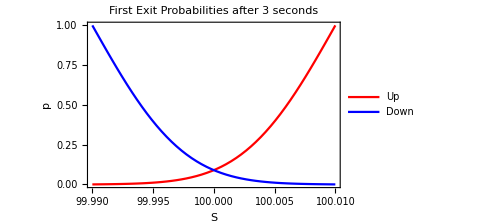

```mathematica
Plot[{
Ptup[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0,20],
Ptdown[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0,20]},
{S,100-0.01,100+0.01},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},PlotLegends->{"Up","Down"},PlotLabel->Style[Framed["First Exit Probabilities after 3 seconds"],12],FrameLabel->{Style[Framed["S"],10],Style[Framed["p"],10]},ImageSize->Medium]
```

Figure 4

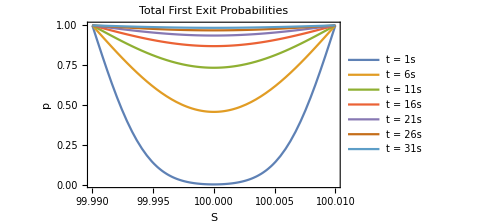

```mathematica
Plot[Evaluate[Table[Ptup[S,100+0.01,100-0.01,0.01/(√(24 3600)),t,0,20]+Ptdown[S,100+0.01,100-0.01,0.01/(√(24 3600)),t,0,20],{t,1,31,5}]],
{S,100-0.01,100+0.01},Frame->True,PlotRange->All,PlotLegends->Table[StringJoin["t = ",ToString[t],"s"],{t,1,31,5}],PlotLabel->Style[Framed["Total First Exit Probabilities"],12],FrameLabel->{Style[Framed["S"],10],Style[Framed["p"],10]},ImageSize->Medium]
```

```mathematica
FullSimplify[Refine[Ptup[S0, Bu, Bd, σ, t, μ, 1],t>0]]
```

NN[(t μ-(t σ^2)/2-Log[Bu]+Log[S0])/(√t σ)]+1/(Bd Bu)(-Bd^(2-(2 μ)/σ^2) Bu^((2 μ)/σ^2) NN[(-2 t μ+t σ^2+4 Log[Bd]-2 Log[Bu]-2 Log[S0])/(2 √t σ)]+S0^(1-(2 μ)/σ^2) (-Bd^((2 μ)/σ^2) Bu NN[(t μ-(t σ^2)/2+2 Log[Bd]-Log[Bu]-Log[S0])/(√t σ)]+Bd Bu^((2 μ)/σ^2) NN[(-t μ+(t σ^2)/2-Log[Bu]+Log[S0])/(√t σ)]))

```mathematica
FullSimplify[Refine[Ptup[S0, Bu, Bd, σ, t, 0, 1],t>0]]
```

-(Bd NN[(t σ^2+4 Log[Bd]-2 Log[Bu]-2 Log[S0])/(2 √t σ)])/Bu+NN[(-(t σ^2)/2-Log[Bu]+Log[S0])/(√t σ)]+(S0 NN[((t σ^2)/2-Log[Bu]+Log[S0])/(√t σ)])/Bu-(S0 NN[-(t σ^2-4 Log[Bd]+2 Log[Bu]+2 Log[S0])/(2 √t σ)])/Bd

```mathematica
FullSimplify[Refine[Ptdown[S0, Bu, Bd, σ, t, 0, 1],t>0]]
```

NN[((t σ^2)/2+Log[Bd]-Log[S0])/(√t σ)]+(S0 NN[(-(t σ^2)/2+Log[Bd]-Log[S0])/(√t σ)]-Bu NN[(-(t σ^2)/2+Log[Bd]-2 Log[Bu]+Log[S0])/(√t σ)])/Bd-(S0 NN[((t σ^2)/2+Log[Bd]-2 Log[Bu]+Log[S0])/(√t σ)])/Bu

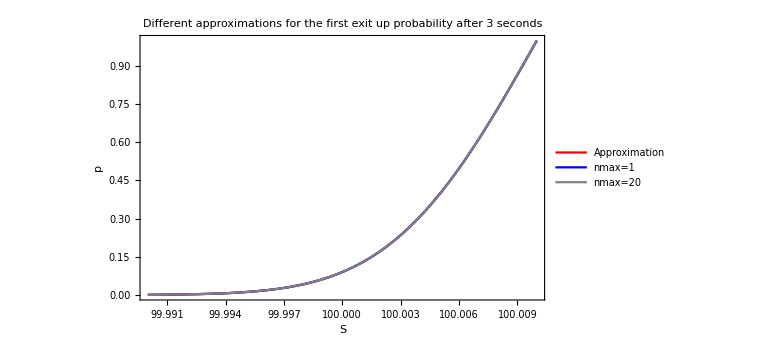

```mathematica
Plot[{NN[(Log[S/(100+0.01)]-1/2(0.01/(√(24 3600)))^2 3)/((0.01/(√(24 3600)))√3)]+(S/(100+0.01))NN[(Log[S/(100+0.01)]+1/2(0.01/(√(24 3600)))^2 3)/((0.01/(√(24 3600)))√3)],
Ptup[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0,1],
Ptup[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0,20]},
{S,100-0.01,100+0.01},Frame->True,PlotRange->All,PlotStyle->{Red,Blue, Gray},PlotLegends->{"Approximation","nmax=1","nmax=20"},PlotLabel->Style[Framed["Different approximations for the first exit up probability after 3 seconds"],14],FrameLabel->{Style[Framed["S"],12],Style[Framed["p"],12]},ImageSize->Large]
```

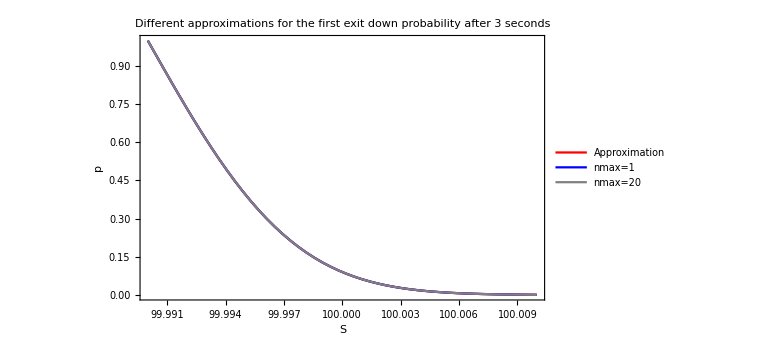

```mathematica
Plot[{(S/(100-0.01))NN[(Log[(100-0.01)/S]-1/2(0.01/(√(24 3600)))^2 3)/((0.01/(√(24 3600)))√3)]+NN[(Log[(100-0.01)/S]+1/2(0.01/(√(24 3600)))^2 3)/((0.01/(√(24 3600)))√3)],
Ptdown[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0,1],
Ptdown[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0,20]},
{S,100-0.01,100+0.01},Frame->True,PlotRange->All,PlotStyle->{Red,Blue, Gray},PlotLegends->{"Approximation","nmax=1","nmax=20"},PlotLabel->Style[Framed["Different approximations for the first exit down probability after 3 seconds"],14],FrameLabel->{Style[Framed["S"],12],Style[Framed["p"],12]},ImageSize->Large]
```

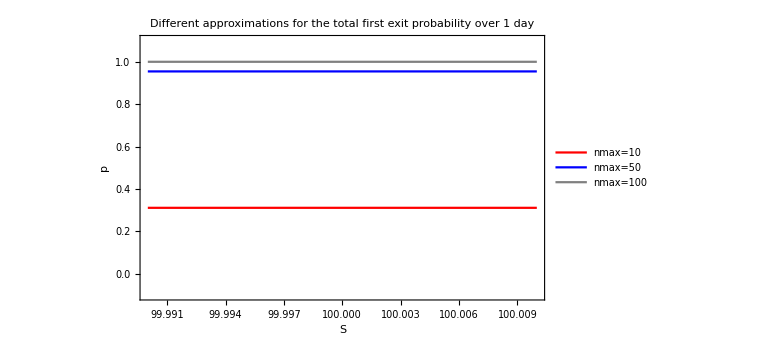

```mathematica
Plot[{Ptup[S,100+0.01,100-0.01,0.01,1,0,10]+Ptdown[S,100+0.01,100-0.01,0.01,1,0,10],
Ptup[S,100+0.01,100-0.01,0.01,1,0,50]+Ptdown[S,100+0.01,100-0.01,0.01,1,0,50],
Ptup[S,100+0.01,100-0.01,0.01,1,0,100]+Ptdown[S,100+0.01,100-0.01,0.01,1,0,100]},
{S,100-0.01,100+0.01},Frame->True,PlotRange->{All,{-0.1,1.1}},PlotStyle->{Red,Blue, Gray},PlotLegends->{"nmax=10","nmax=50","nmax=100"},PlotLabel->Style[Framed["Different approximations for the total first exit probability over 1 day"],14],FrameLabel->{Style[Framed["S"],12],Style[Framed["p"],12]},ImageSize->Large]
```

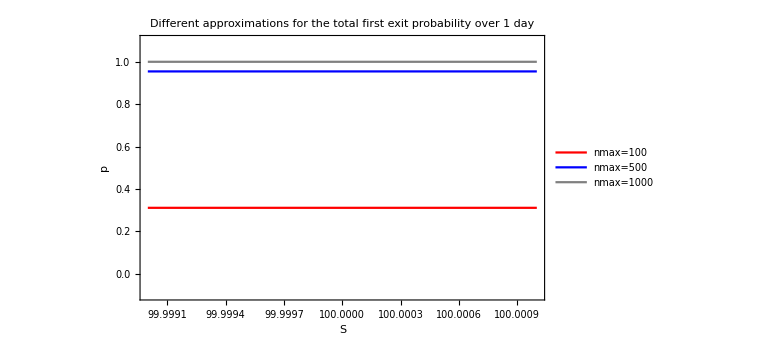

```mathematica
Plot[{Ptup[S,100+0.001,100-0.001,0.01,1,0,100]+Ptdown[S,100+0.001,100-0.001,0.01,1,0,100],
Ptup[S,100+0.001,100-0.001,0.01,1,0,500]+Ptdown[S,100+0.001,100-0.001,0.01,1,0,500],
Ptup[S,100+0.001,100-0.001,0.01,1,0,1000]+Ptdown[S,100+0.001,100-0.001,0.01,1,0,1000]},
{S,100-0.001,100+0.001},Frame->True,PlotRange->{All,{-0.1,1.1}},PlotStyle->{Red,Blue, Gray},PlotLegends->{"nmax=100","nmax=500","nmax=1000"},PlotLabel->Style[Framed["Different approximations for the total first exit probability over 1 day"],14],FrameLabel->{Style[Framed["S"],12],Style[Framed["p"],12]},ImageSize->Large]
```

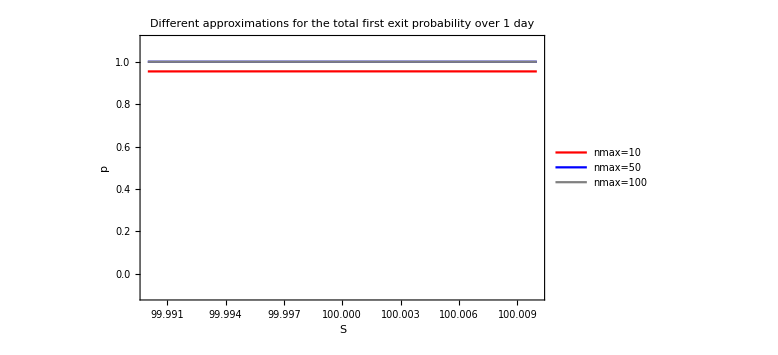

```mathematica
Plot[{Ptup[S,100+0.01,100-0.01,0.002,1,0,10]+Ptdown[S,100+0.01,100-0.01,0.002,1,0,10],
Ptup[S,100+0.01,100-0.01,0.002,1,0,50]+Ptdown[S,100+0.01,100-0.01,0.002,1,0,50],
Ptup[S,100+0.01,100-0.01,0.002,1,0,100]+Ptdown[S,100+0.01,100-0.01,0.002,1,0,100]},
{S,100-0.01,100+0.01},Frame->True,PlotRange->{All,{-0.1,1.1}},PlotStyle->{Red,Blue, Gray},PlotLegends->{"nmax=10","nmax=50","nmax=100"},PlotLabel->Style[Framed["Different approximations for the total first exit probability over 1 day"],14],FrameLabel->{Style[Framed["S"],12],Style[Framed["p"],12]},ImageSize->Large]
```

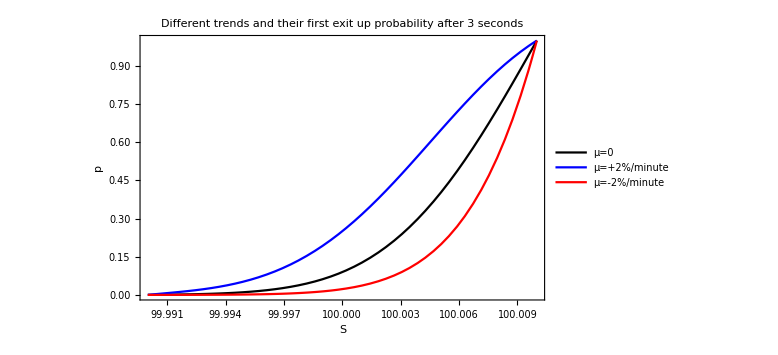

```mathematica
Plot[{
Ptup[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0,20],
Ptup[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0.02/(24 60),20],
Ptup[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,-0.02/(24 60),20]},
{S,100-0.01,100+0.01},Frame->True,PlotRange->All,PlotStyle->{Black,Blue,Red},PlotLegends->{"μ=0","μ=+2%/minute","μ=-2%/minute"},PlotLabel->Style[Framed["Different trends and their first exit up probability after 3 seconds"],14],FrameLabel->{Style[Framed["S"],12],Style[Framed["p"],12]},ImageSize->Large]
```

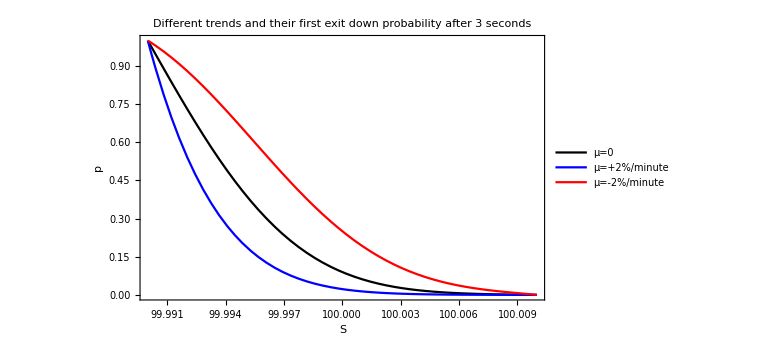

```mathematica
Plot[{
Ptdown[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0,20],
Ptdown[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,0.02/(24 60),20],
Ptdown[S,100+0.01,100-0.01,0.01/(√(24 3600)),3,-0.02/(24 60),20]},
{S,100-0.01,100+0.01},Frame->True,PlotRange->All,PlotStyle->{Black,Blue,Red},PlotLegends->{"μ=0","μ=+2%/minute","μ=-2%/minute"},PlotLabel->Style[Framed["Different trends and their first exit down probability after 3 seconds"],14],FrameLabel->{Style[Framed["S"],12],Style[Framed["p"],12]},ImageSize->Large]
```

### 3.3.2 Double-barrier densities of first exit times

```mathematica
FullSimplify[D[ⅇ^(ω/σ^2(bu-x0))
(ⅇ^(ω/σ^2 yn)NN[(yn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn)NN[(yn-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn)NN[(zn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn)NN[(zn-ω t)/(σ √t)]),t]]
```

1/(2 t^(3/2) σ)ⅇ^(-((yn+zn) ω)/σ^2) (-ⅇ^(((bu-x0+zn) ω)/σ^2) (yn+t ω) NN'[(yn-t ω)/(√t σ)]+ⅇ^((yn ω)/σ^2) (zn+t ω) NN'[(zn-t ω)/(√t σ)]-ⅇ^(((bu-x0+2 yn+zn) ω)/σ^2) (yn-t ω) NN'[(yn+t ω)/(√t σ)]+ⅇ^(((yn+2 zn) ω)/σ^2) (zn-t ω) NN'[(zn+t ω)/(√t σ)])

```mathematica
ⅇ^((μ-1/2 σ^2)/σ^2(bu-x0))
```

ⅇ^(((bu-x0) (μ-σ^2/2))/σ^2)

```mathematica
ⅇ^(μ/σ^2(bu-x0))ⅇ^(-1/2(bu-x0))
```

```mathematica
{FullSimplify[D[NN[(yn+ω t)/(σ √t)],t]],FullSimplify[D[NN[(yn-ω t)/(σ √t)],t]],FullSimplify[D[NN[(zn+ω t)/(σ √t)],t]],FullSimplify[D[NN[(zn-ω t)/(σ √t)],t]]}
```

{((-yn+t ω) NN'[(yn+t ω)/(√t σ)])/(2 t^(3/2) σ),-((yn+t ω) NN'[(yn-t ω)/(√t σ)])/(2 t^(3/2) σ),((-zn+t ω) NN'[(zn+t ω)/(√t σ)])/(2 t^(3/2) σ),-((zn+t ω) NN'[(zn-t ω)/(√t σ)])/(2 t^(3/2) σ)}

```mathematica
{ns[(ω t)/(σ √t)],ns[yn/(σ √t)]}
```

{(ⅇ^(-(t ω^2)/(2 σ^2)))/(√(2 π)),(ⅇ^(-yn^2/(2 t σ^2)))/(√(2 π))}

```mathematica
{ⅇ^(ω/σ^2(bu-x0+yn)) ns[(yn+t ω)/(√t σ)],ⅇ^(ω/σ^2(bu-x0-yn)) ns[(yn-t ω)/(√t σ)],ⅇ^(ω/σ^2(bu-x0+zn))ns[(zn+t ω)/(√t σ)],ⅇ^(ω/σ^2(bu-x0-zn)) ns[(zn-t ω)/(√t σ)]}
```

{(ⅇ^(((bu-x0+yn) ω)/σ^2-(yn+t ω)^2/(2 t σ^2)))/(√(2 π)),(ⅇ^(((bu-x0-yn) ω)/σ^2-(yn-t ω)^2/(2 t σ^2)))/(√(2 π)),(ⅇ^(((bu-x0+zn) ω)/σ^2-(zn+t ω)^2/(2 t σ^2)))/(√(2 π)),(ⅇ^(((bu-x0-zn) ω)/σ^2-(zn-t ω)^2/(2 t σ^2)))/(√(2 π))}

```mathematica
Map[FullSimplify,{((bu-x0+yn) ω)/σ^2-(yn+t ω)^2/(2 t σ^2),((bu-x0-yn) ω)/σ^2-(yn-t ω)^2/(2 t σ^2),ω/σ^2(bu-x0+zn)-(zn+t ω)^2/(2 t σ^2),ω/σ^2(bu-x0-zn)-(zn-t ω)^2/(2 t σ^2)}]
```

{(2 (bu-x0+yn) ω-(yn+t ω)^2/t)/(2 σ^2),-(yn^2+t ω (-2 bu+2 x0+t ω))/(2 t σ^2),(2 (bu-x0+zn) ω-(zn+t ω)^2/t)/(2 σ^2),-(zn^2+t ω (-2 bu+2 x0+t ω))/(2 t σ^2)}

```mathematica
Map[Expand,{(2 (bu-x0+yn) ω-(yn+t ω)^2/t)/(2 σ^2),-(yn^2+t ω (-2 bu+2 x0+t ω))/(2 t σ^2),(2 (bu-x0+zn) ω-(zn+t ω)^2/t)/(2 σ^2),-(zn^2+t ω (-2 bu+2 x0+t ω))/(2 t σ^2)}]
```

{-yn^2/(2 t σ^2)+(bu ω)/σ^2-(x0 ω)/σ^2-(t ω^2)/(2 σ^2),-yn^2/(2 t σ^2)+(bu ω)/σ^2-(x0 ω)/σ^2-(t ω^2)/(2 σ^2),-zn^2/(2 t σ^2)+(bu ω)/σ^2-(x0 ω)/σ^2-(t ω^2)/(2 σ^2),-zn^2/(2 t σ^2)+(bu ω)/σ^2-(x0 ω)/σ^2-(t ω^2)/(2 σ^2)}

```mathematica
Map[FullSimplify,{+(bu ω)/σ^2-(x0 ω)/σ^2,+(bu ω)/σ^2-(x0 ω)/σ^2,+(bu ω)/σ^2-(x0 ω)/σ^2,+(bu ω)/σ^2-(x0 ω)/σ^2}]
```

{((bu-x0) ω)/σ^2,((bu-x0) ω)/σ^2,((bu-x0) ω)/σ^2,((bu-x0) ω)/σ^2}

```mathematica
FullSimplify[D[ⅇ^((μ-1/2 σ^2)/σ^2(bu-x0))ⅇ^((μ-1/2 σ^2)/σ^2 yn)NN[(yn+(μ-1/2 σ^2) t)/(σ √t)],t]]
```

-(ⅇ^(-((bu-x0+yn) (-2 μ+σ^2))/(2 σ^2)) (2 yn+t (-2 μ+σ^2)) NN'[(yn+t (μ-σ^2/2))/(√t σ)])/(4 t^(3/2) σ)

```mathematica
-(ⅇ^(-((bu-x0+yn) (-2 μ+σ^2))/(2 σ^2)) (2 yn+t (-2 μ+σ^2)) NN'[(yn+t (μ-σ^2/2))/(√t σ)])/(4 t^(3/2) σ)
```

```mathematica
FullSimplify[-((bu-x0+yn) (-2 μ+σ^2))/(2 σ^2)-1/2((yn+t (μ-σ^2/2))/(√t σ))^2]
```

(-4 yn^2+t (2 μ-σ^2) (4 bu-4 x0-2 t μ+t σ^2))/(8 t σ^2)

```mathematica
-(yn^2+t ( μ-1/2 σ^2) (2bu-2 x0- t μ+1/2 t σ^2))/(2 t σ^2)
```

```mathematica
1/(2 t)(- yn+t ( μ-1/2 σ^2))/(σ √t)ⅇ^(-1/2(4(bu-x0+yn) ( μ-1/2 σ^2)t)/(σ^2 t)) ⅇ^(-1/2((yn+t (μ-σ^2/2))/(√t σ))^2)
```

Equation: PDF for hitting times

```mathematica
ϕtup[S0_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=Module[{x0,bu,bd},
If[t==0,0,
x0=Log[S0];
bu=Log[Bu];
bd=Log[Bd];
yn[n_]:=+1*(2*(n-1)*bd-(2n-1)*bu+x0);
zn[n_]:=+1*(2*n*bd-(2n-1)*bu-x0);
ⅇ^(μ/σ^2(bu-x0))(√(2π))/t nn[(μ/σ-1/2 σ)√t]Sum[Quiet[
nn[zn[n]/(σ √t)](zn[n]/(σ √t))-nn[yn[n]/(σ √t)](yn[n]/(σ √t))],{n,1,nmax}]]];
```

```mathematica
ϕtdown[S0_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=
Module[{x0,bu,bd},
If[t==0,0,
x0=Log[S0];
bu=Log[Bu];
bd=Log[Bd];
yn[n_]:=-1*(2*(n-1)*bu-(2n-1)*bd+x0);
zn[n_]:=-1*(2*n*bu-(2n-1)*bd-x0);
ⅇ^(μ/σ^2(bd-x0))(√(2π))/t nn[(μ/σ-1/2 σ)√t]Sum[Quiet[
nn[zn[n]/(σ √t)](zn[n]/(σ √t))-nn[yn[n]/(σ √t)](yn[n]/(σ √t))],{n,1,nmax}]]];
```

Figure 5

```mathematica
Plot3D[ϕtup[x,100+0.01,100-0.01,0.01/(√(24 3600)),t,0,20],{x,100-0.01,100+0.01},{t,0,10},
AxesLabel->{Style[Framed["S_0"],12],Style[Framed["t"],12],Style[Framed["ϕ_+"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["Density for hitting times - upper barrier S_+=S_0+α, μ=0"],14]]
```

-Graphics3D-

Figure 5

```mathematica
Plot3D[ϕtdown[x,100+0.01,100-0.01,0.01/(√(24 3600)),t,0,20],{x,100-0.01,100+0.01},{t,0,10},
AxesLabel->{Style[Framed["S_0"],12],Style[Framed["t"],12],Style[Framed["ϕ_+"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["Density for hitting times - lower barrier S_+=S_0-α, μ=0"],14]]
```

-Graphics3D-

Figure 6

```mathematica
Plot3D[ϕtup[x,100+0.01,100-0.01,0.01/(√(24 3600)),t,0.02/(24 60),20],{x,100-0.01,100+0.01},{t,0,10},
AxesLabel->{Style[Framed["S_0"],12],Style[Framed["t"],12],Style[Framed["ϕ_+"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["Density for hitting times - upper barrier S_+=S_0+α, μ=+2%/minute"],14]]
```

-Graphics3D-

Figure 6

```mathematica
Plot3D[ϕtdown[x,100+0.01,100-0.01,0.01/(√(24 3600)),t,0.02/(24 60),20],{x,100-0.01,100+0.01},{t,0,10},
AxesLabel->{Style[Framed["S_0"],12],Style[Framed["t"],12],Style[Framed["ϕ_+"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["Density for hitting times - lower barrier S_+=S_0-α, μ=+2%/minute"],14]]
```

-Graphics3D-

Figure 7

```mathematica
Plot3D[ϕtup[x,100+0.01,100-0.01,0.01/(√(24 3600)),t,-0.02/(24 60),20],{x,100-0.01,100+0.01},{t,0,10},
AxesLabel->{Style[Framed["S_0"],12],Style[Framed["t"],12],Style[Framed["ϕ_+"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["Density for hitting times - upper barrier S_+=S_0+α, μ=-2%/minute"],14]]
```

-Graphics3D-

Figure 7

```mathematica
Plot3D[ϕtdown[x,100+0.01,100-0.01,0.01/(√(24 3600)),t,-0.02/(24 60),20],{x,100-0.01,100+0.01},{t,0,10},
AxesLabel->{Style[Framed["S_0"],12],Style[Framed["t"],12],Style[Framed["ϕ_+"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["Density for hitting times - lower barrier S_+=S_0-α, μ=2%/minute"],14]]
```

-Graphics3D-

### 3.3.3 Starting spot and barriers for the Uncertainty Zones model

```mathematica
?ϕtup
```

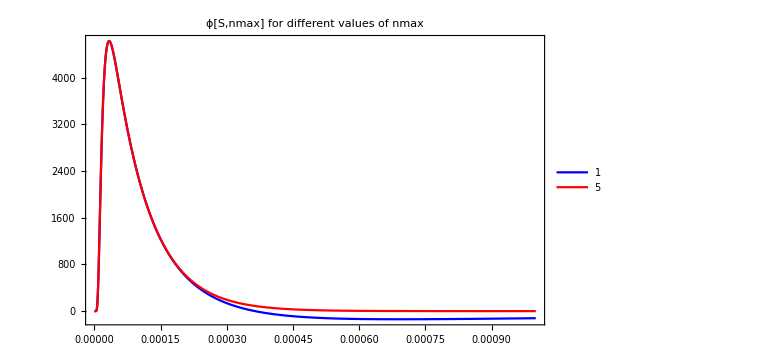

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
μ=0},
DiscretePlot[{
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1],
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,5]},
{t,0,0.001,0.000001},Frame->True,PlotRange->All,PlotStyle->{Blue,Red},Filling->None,Joined->True,
PlotLegends->{1,5},PlotLabel->"ϕ[S,nmax] for different values of nmax",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

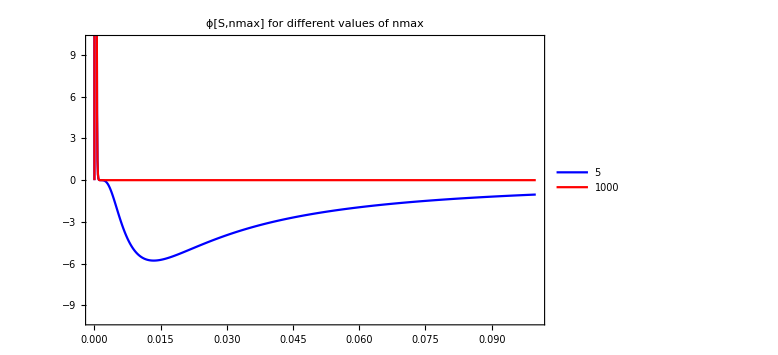

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
μ=0},
DiscretePlot[{
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,5],
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]},
{t,0,0.1,0.0001},Frame->True,PlotRange->{All,{-10,10}},PlotStyle->{Blue,Red},Filling->None,Joined->True,
PlotLegends->{5,1000},PlotLabel->"ϕ[S,nmax] for different values of nmax",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

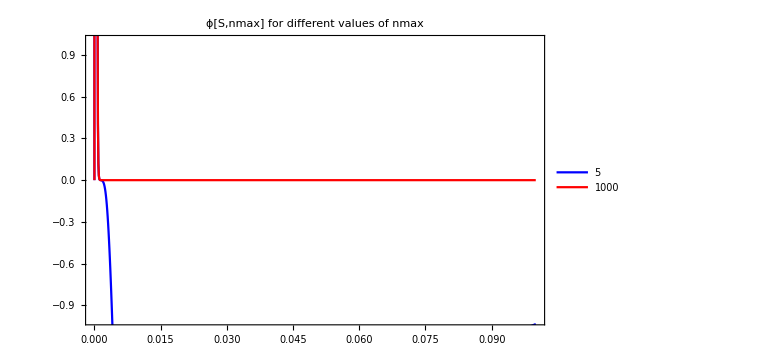

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
μ=0},
DiscretePlot[{
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,5],
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]},
{t,0,0.1,0.0001},Frame->True,PlotRange->{All,{-1,1}},PlotStyle->{Blue,Red},Filling->None,Joined->True,
PlotLegends->{5,1000},PlotLabel->"ϕ[S,nmax] for different values of nmax",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

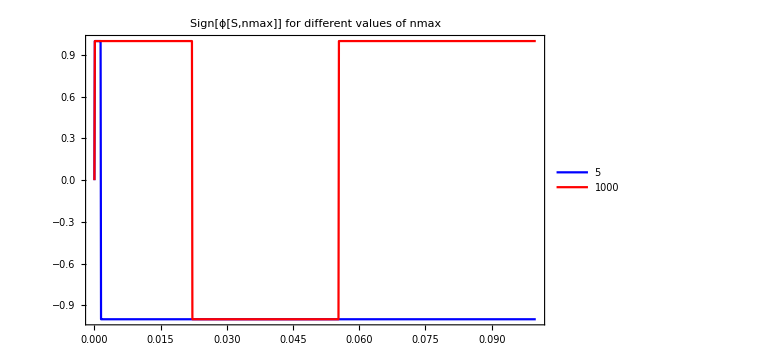

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
μ=0},
DiscretePlot[{
Sign[ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,5]],
Sign[ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]]},
{t,0,0.1,0.0001},Frame->True,PlotRange->All,PlotStyle->{Blue,Red},Filling->None,Joined->True,
PlotLegends->{5,1000},PlotLabel->"Sign[ϕ[S,nmax]] for different values of nmax",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

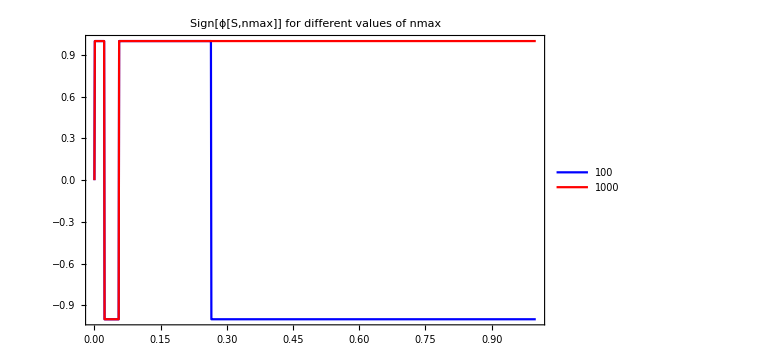

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
μ=0},
DiscretePlot[{
Sign[ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,100]],
Sign[ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]]},
{t,0,1,0.001},Frame->True,PlotRange->All,PlotStyle->{Blue,Red},Filling->None,Joined->True,
PlotLegends->{100,1000},PlotLabel->"Sign[ϕ[S,nmax]] for different values of nmax",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

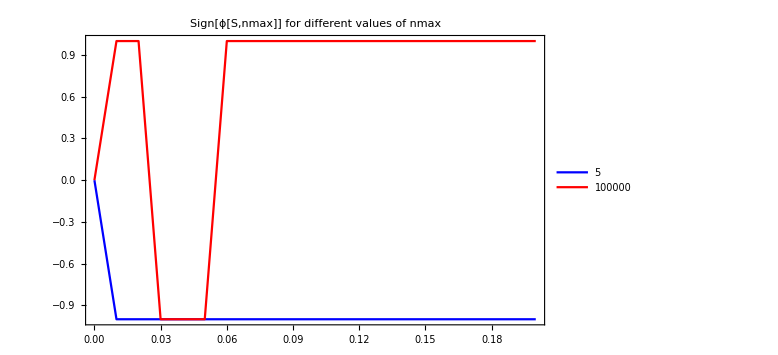

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
μ=0},
DiscretePlot[{
Sign[ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,5]],
Sign[ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,100000]]},
{t,0,0.2,0.01},Frame->True,PlotRange->All,PlotStyle->{Blue,Red},Filling->None,Joined->True,
PlotLegends->{5,100000},PlotLabel->"Sign[ϕ[S,nmax]] for different values of nmax",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

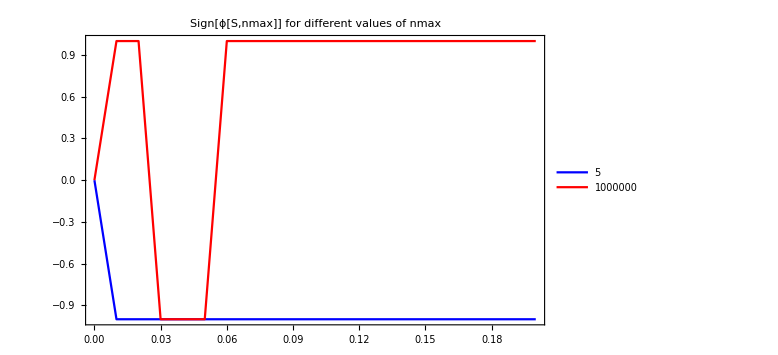

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
μ=0},
DiscretePlot[{
Sign[ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,5]],
Sign[ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000000]]},
{t,0,0.2,0.01},Frame->True,PlotRange->All,PlotStyle->{Blue,Red},Filling->None,Joined->True,
PlotLegends->{5,1000000},PlotLabel->"Sign[ϕ[S,nmax]] for different values of nmax",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

Figure 8

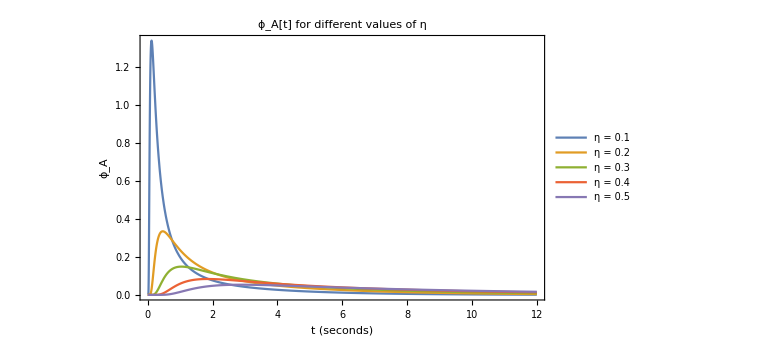

```mathematica
Module[{α=0.01,
σ=0.01/(√(24*3600)),
S=100,
μ=0},
Plot[Evaluate[Table[
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10000],
{η,0.1,0.5,0.1}]],
{t,0,12},Frame->True,PlotRange->All,Filling->None,
PlotLegends->Table[StringJoin["η = ",ToString[η]],{η,0.1,0.5,0.1}],PlotLabel->Style[Framed["ϕ_A[t] for different values of η"],14],AxesOrigin->{0,0},Axes->True,FrameLabel->{Style[Framed["t (seconds)"],12],Style[Framed["ϕ_A"],12]},ImageSize->Large]]
```

Figure 9

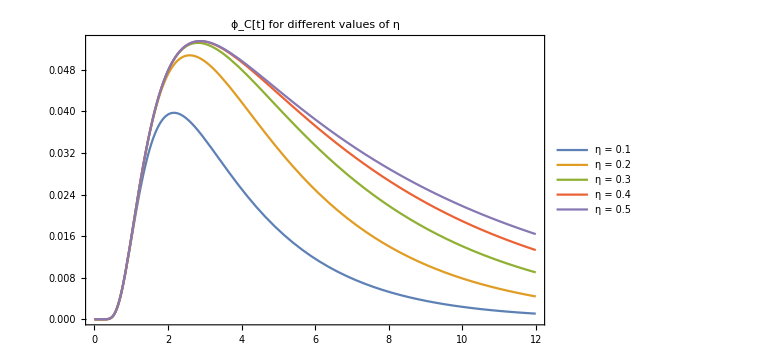

```mathematica
Module[{α=0.01,
σ=0.01/(√(24*3600)),
S=100,
μ=0},
Plot[Evaluate[Table[
ϕtup[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10000],
{η,0.1,0.5,0.1}]],
{t,0,12},Frame->True,PlotRange->All,Filling->None,
PlotLegends->Table[StringJoin["η = ",ToString[η]],{η,0.1,0.5,0.1}],PlotLabel->"ϕ_C[t] for different values of η",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

Figure 10

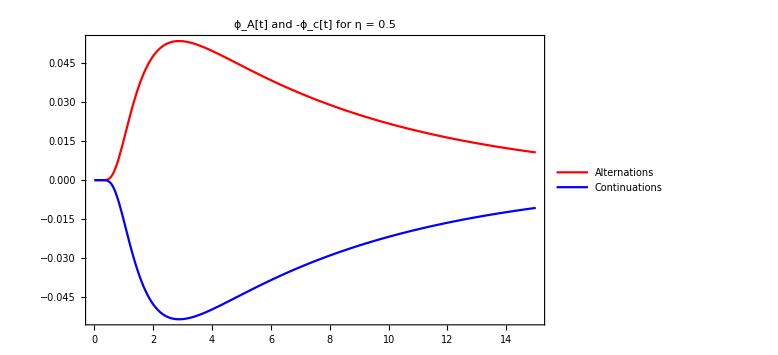

```mathematica
Module[{α=0.01,
σ=0.01/(√(24*3600)),
S=100,
η=0.5,
μ=0},
Plot[{
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10000],
-ϕtup[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10000]},
{t,0,15},Frame->True,PlotRange->All,Filling->None,PlotStyle->{Red,Blue},
PlotLegends->{"Alternations","Continuations"},PlotLabel->"ϕ_A[t] and -ϕ_c[t] for η = 0.5",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

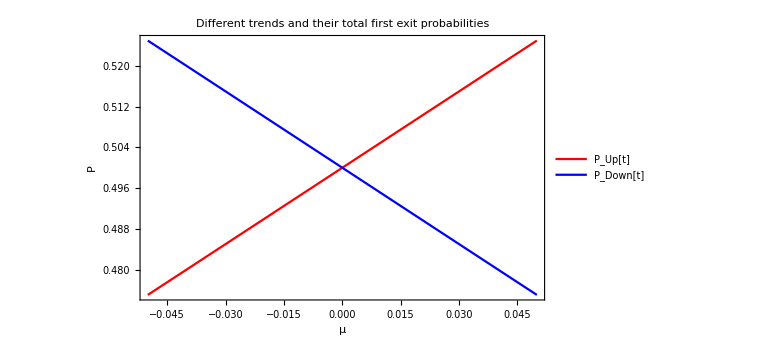

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
t=1},
DiscretePlot[{
Ptup[S,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000],
Ptdown[S,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]},
{μ,-0.05,+0.05,0.01},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},Joined->True,Filling->None,PlotLegends->{"P_Up[t]","P_Down[t]"},PlotLabel->Style[Framed["Different trends and their total first exit probabilities"],14],FrameLabel->{Style[Framed["μ"],12],Style[Framed["P"],12]},ImageSize->Large]]
```

Figure 12

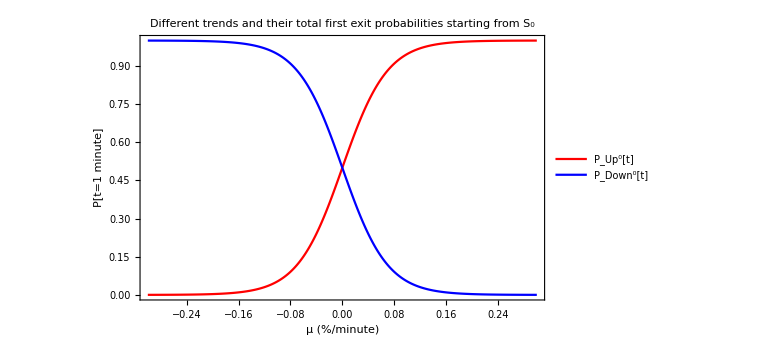

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
t=1/(24*60)},
DiscretePlot[{
Ptup[S,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000],
Ptdown[S,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000]},
{μ,-0.3,+0.3,0.002},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},Joined->True,
Filling->None,PlotLegends->{"P_Up^0[t]","P_Down^0[t]"},AxesOrigin->{0,0.5},PlotLabel->Style[Framed["Different trends and their total first exit probabilities starting from S_0"],14],FrameLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["P[t=1 minute]"],12]},ImageSize->Large]]
```

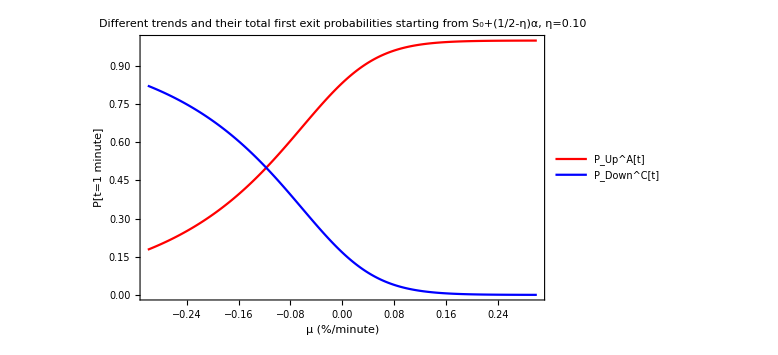

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.1,
t=1/(24*60)},
DiscretePlot[{
Ptup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000],
Ptdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000]},
{μ,-0.3,+0.3,0.002},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},Joined->True,
Filling->None,PlotLegends->{"P_Up^A[t]","P_Down^C[t]"},AxesOrigin->{0,0.5},PlotLabel->Style[Framed["Different trends and their total first exit probabilities starting from S_0+(1/2-η)α, η=0.10"],14],FrameLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["P[t=1 minute]"],12]},ImageSize->Large]]
```

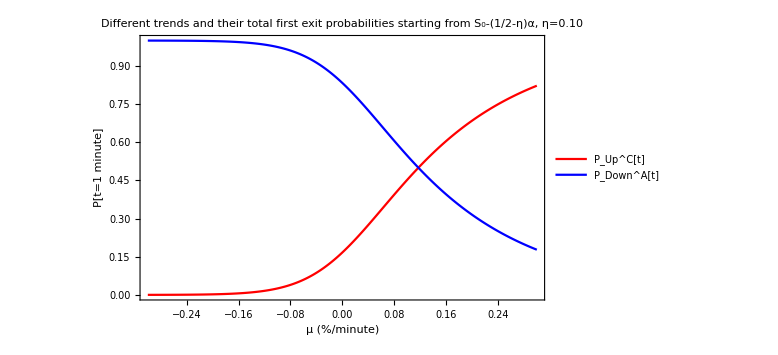

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.1,
t=1/(24*60)},
DiscretePlot[{
Ptup[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000],
Ptdown[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000]},
{μ,-0.3,+0.3,0.002},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},Joined->True,
Filling->None,PlotLegends->{"P_Up^C[t]","P_Down^A[t]"},AxesOrigin->{0,0.5},PlotLabel->Style[Framed["Different trends and their total first exit probabilities starting from S_0-(1/2-η)α, η=0.10"],14],FrameLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["P[t=1 minute]"],12]},ImageSize->Large]]
```

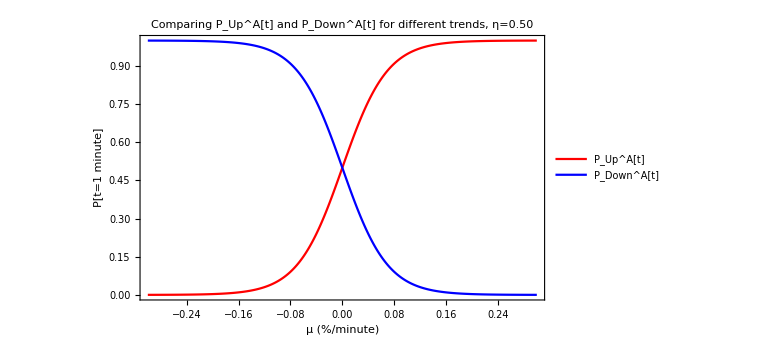

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.5,
t=1/(24*60)},
DiscretePlot[{
Ptup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000],
Ptdown[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000]},
{μ,-0.3,+0.3,0.002},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},Joined->True,
Filling->None,PlotLegends->{"P_Up^A[t]","P_Down^A[t]"},AxesOrigin->{0,0.5},PlotLabel->Style[Framed["Comparing P_Up^A[t] and P_Down^A[t] for different trends, η=0.50"],14],FrameLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["P[t=1 minute]"],12]},ImageSize->Large]]
```

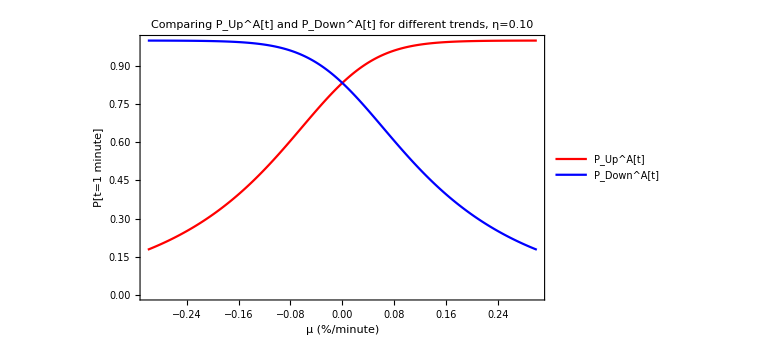

```mathematica
Module[{α=0.01,
σ=0.01,
S=100,
η=0.1,
t=1/(24*60)},
DiscretePlot[{
Ptup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000],
Ptdown[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,1000]},
{μ,-0.3,+0.3,0.002},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},Joined->True,
Filling->None,PlotLegends->{"P_Up^A[t]","P_Down^A[t]"},AxesOrigin->{0,0.5},PlotLabel->Style[Framed["Comparing P_Up^A[t] and P_Down^A[t] for different trends, η=0.10"],14],FrameLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["P[t=1 minute]"],12]},ImageSize->Large]]
```

```mathematica
fv[j_,η_]:=UnitStep[j-3/2](-1)^j((Quotient[j+2,4]-1/2)+(-1)^Quotient[j,2] η);
fvc[j_]:=2UnitStep[j-3/2](-1)^j((Quotient[j+2,4]-1/2)+(-1)^Quotient[j,2] 1/4);
```

```mathematica
fmat[level_]:=Module[{n},
n=4level+1;
SparseArray[{
{i_,j_}/;And[i≤3,4≤j≤5]->1,
{i_,j_}/;And[i≥4,Or[j==4Quotient[i,4]-2+Boole[OddQ[i]],j==4Quotient[i,4]+4+Boole[OddQ[i]]]]->1},
{n,n}]];
```

```mathematica
Grid[fmat[2],Frame->All]
```

0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0

```mathematica
AdjacencyGraph[
((fmat[2])),DirectedEdges->True,VertexLabels->None,VertexCoordinates->Table[{2Quotient[j-2,4],fvc[j]},{j,9}]]
```

-Graphics-

```mathematica
stattm[S_,α_,σ_,μ_,η_,nmax_:1000]:=Module[{init,pup0,pupA,pdownA,tmat,proc,probs},
pup0=Ptup[S,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
init={pup0,1-pup0,0,0,0,0};
(* Print[Grid[{init},Frame->True]]; *)
pupA=Ptup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
pdownA=Ptdown[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
tmat=
{{0,0,0,pdownA,1-pdownA,0},
{0,0,pupA,0,0,1-pupA},
{1,0,0,0,0,0},
{0,1,0,0,0,0},
{1,0,0,0,0,0},
{0,1,0,0,0,0}};
(* Print[Grid[tmat,Frame->True]]; *)
proc=DiscreteMarkovProcess[init,tmat];
probs=Chop[Table[PDF[StationaryDistribution[proc],j],{j,Length[init]}]];
(* Print[StringJoin["eta = ",ToString[(probs⟦5⟧+probs⟦6⟧)/(2*(probs⟦3⟧+probs⟦4⟧))]]]; *)
2*probs
];
```

```mathematica
Grid[Map[{#,stattm[100,0.01,0.01,0,0.1,#]}&,{100,1000,10000}]]
```

100 | {0.5,0.5,0.409836,0.409836,0.0901642,0.0901642}
1000 | {0.5,0.5,0.416667,0.416667,0.0833333,0.0833333}
10000 | {0.5,0.5,0.416667,0.416667,0.0833333,0.0833333}

```mathematica
showtm[S_,α_,σ_,μ_,η_,nmax_:1000]:=Module[{init,pup0,pupA,pdownA,tmat,proc,probs},
pup0=Ptup[S,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
init={pup0,1-pup0,0,0,0,0};
(* Print[Grid[{init},Frame->True]]; *)
pupA=Ptup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
pdownA=Ptdown[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
tmat=
{{0,0,0,pdownA,1-pdownA,0},
{0,0,pupA,0,0,1-pupA},
{1,0,0,0,0,0},
{0,1,0,0,0,0},
{1,0,0,0,0,0},
{0,1,0,0,0,0}};
tmat
];
```

```mathematica
Grid[Map[{#,Grid[showtm[100,0.01,0.01,0,0.1,#]]}&,{100,1000,10000}],Frame->All]
```

100 | 0 | 0 | 0 | 0.819672 | 0.180328 | 0
0 | 0 | 0.819672 | 0 | 0 | 0.180328
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1000 | 0 | 0 | 0 | 0.833333 | 0.166667 | 0
0 | 0 | 0.833333 | 0 | 0 | 0.166667
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
10000 | 0 | 0 | 0 | 0.833333 | 0.166667 | 0
0 | 0 | 0.833333 | 0 | 0 | 0.166667
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0

```mathematica
getdmp[S_,α_,σ_,μ_,η_,nmax_:1000]:=Module[{init,pup0,pupA,pdownA,tmat,proc,probs},
pup0=Ptup[S,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
init={pup0,1-pup0,0,0,0,0};
(* Print[Grid[{init},Frame->True]]; *)
pupA=Ptup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
pdownA=Ptdown[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
tmat=
{{0,0,0,pdownA,1-pdownA,0},
{0,0,pupA,0,0,1-pupA},
{1,0,0,0,0,0},
{0,1,0,0,0,0},
{1,0,0,0,0,0},
{0,1,0,0,0,0}};
(* Print[Grid[tmat,Frame->True]]; *)
proc=DiscreteMarkovProcess[init,tmat];
proc
];
```

```mathematica
Grid[showtm[100,0.01,0.01,0,0.5,1000]]
```

0 | 0 | 0 | 0.5 | 0.5 | 0
0 | 0 | 0.5 | 0 | 0 | 0.5
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0

```mathematica
dmp1=getdmp[100,0.01,0.01,0,0.5,1000];
```

```mathematica
moves1=RandomFunction[dmp1,{0,100000}];
```

```mathematica
Grid[Sort[Tally[Last[Transpose[First[Normal[moves1]]]]]]]
```

1 | 25048
2 | 24953
3 | 12440
4 | 12440
5 | 12608
6 | 12512

```mathematica
dmp2=getdmp[100,0.01,0.01,0,0.1,1000];
```

```mathematica
moves2=RandomFunction[dmp2,{0,100000}];
```

```mathematica
Grid[Sort[Tally[Last[Transpose[First[Normal[moves2]]]]]]]
```

1 | 25091
2 | 24910
3 | 20785
4 | 20784
5 | 4306
6 | 4125

```mathematica
dmp3=getdmp[100,0.01,0.01,0.05,0.5,1000];
```

```mathematica
moves3=RandomFunction[dmp3,{0,100000}];
```

```mathematica
Grid[Sort[Tally[Last[Transpose[First[Normal[moves3]]]]]]]
```

1 | 26403
2 | 23598
3 | 12470
4 | 12471
5 | 13932
6 | 11127

```mathematica
Log2[9*3600/0.005]
```

22.6276

```mathematica
Log2[9*3600/0.25]
```

16.9837

```mathematica
Solve[((1+4η)/(6η))/((2+2η)/3)==r,η]
```

{{η→(1-r-√(1-r+r^2))/(2 r)},{η→(1-r+√(1-r+r^2))/(2 r)}}

```mathematica
(1-r+√(1-r+r^2))/(2 r)//.r->0.9
```

0.585522

```mathematica
fstatstm[S_,α_,σ_,μ_,η_,nmax_:1000]:=Module[{probs,eta},
probs=stattm[S,α,σ,μ,η,nmax];
eta=(probs⟦5⟧+probs⟦6⟧)/(2*(probs⟦3⟧+probs⟦4⟧));
eta];
```

Equation H Real Eta

```mathematica
FullSimplify[Table[PDF[StationaryDistribution[DiscreteMarkovProcess[
{PUP0,1-PUP0,0,0,0,0},
{{0,0,0,PDOWNA,1-PDOWNA,0},
{0,0,PUPA,0,0,1-PUPA},
{1,0,0,0,0,0},
{0,1,0,0,0,0},
{1,0,0,0,0,0},
{0,1,0,0,0,0}}]],j],{j,6}]]
```

{PUPA/(2 (PDOWNA+PUPA)),PDOWNA/(2 (PDOWNA+PUPA)),(PDOWNA PUPA)/(2 (PDOWNA+PUPA)),(PDOWNA PUPA)/(2 (PDOWNA+PUPA)),-((-1+PDOWNA) PUPA)/(2 (PDOWNA+PUPA)),-(PDOWNA (-1+PUPA))/(2 (PDOWNA+PUPA))}

```mathematica
FullSimplify[((PDOWNA (1-PUPA))/(PDOWNA+PUPA)+((1-PDOWNA) PUPA)/(PDOWNA+PUPA))/(2((PDOWNA PUPA)/(PDOWNA+PUPA)+(PDOWNA PUPA)/(PDOWNA+PUPA)))]
```

(PDOWNA+PUPA-2 PDOWNA PUPA)/(4 PDOWNA PUPA)

```mathematica
Heta[S_,α_,σ_,μ_,η_,nmax_:1000]:=Module[{pupA,pdownA},
pupA=Ptup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
pdownA=Ptdown[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,1,μ,nmax];
(pupA+pdownA)/(4*pupA*pdownA)-1/2
];
```

```mathematica
FullSimplify[(1/(1+2η)+1/(1+2η))/(4*1/(1+2η)*1/(1+2η))-1/2]
```

η

```mathematica
Module[{α=0.01,σ=0.01,S=100,μ=0,η=0.5},fstatstm[S,α,σ,μ,η]]
```

0.5

```mathematica
Module[{α=0.01,μ=0,S=100},
DiscretePlot3D[Heta[S,α,σ,μ*(24*60)/100,η],
{σ,0.002,0.02,0.001},{η,0.05,0.50,0.05},
AxesLabel->{Style[Framed["σ"],12],Style[Framed["UZ η"],12],Style[Framed["H"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["H for different σ with μ=0"],14]]]
```

-Graphics3D-

```mathematica
Module[{α=0.01,μ=0,S=100},
DiscretePlot3D[fstatstm[S,α,σ,μ*(24*60)/100,η],
{σ,0.002,0.02,0.002},{η,0.10,0.50,0.10},
AxesLabel->{Style[Framed["σ"],12],Style[Framed["UZ η"],12],Style[Framed["H"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["H for different σ with μ=0"],14]]]
```

-Graphics3D-

```mathematica
Module[{α=0.01,σ=0.01,S=100},
DiscretePlot3D[{Heta[S,α,σ,μ*(24*60)/100,η],Heta[S,α,σ,μ*(24*60)/100,η]-η},
{μ,-0.05,+0.05,0.01},{η,0.10,0.50,0.10},PlotStyle->{Blue,Red},PlotLegends->{"H","Δη"},
AxesLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["UZ η"],12],Style[Framed["H"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["H for different μ with σ=1%"],14]]]
```

-Graphics3D-

```mathematica
Module[{α=0.01,σ=0.02,S=100},
DiscretePlot3D[{Heta[S,α,σ,μ*(24*60)/100,η],Heta[S,α,σ,μ*(24*60)/100,η]-η},
{μ,-0.05,+0.05,0.01},{η,0.10,0.50,0.10},PlotStyle->{Blue,Red},PlotLegends->{"H","Δη"},
AxesLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["UZ η"],12],Style[Framed["H"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["H for different μ with σ=2%"],14]]]
```

-Graphics3D-

```mathematica
Module[{α=0.01,σ=0.005,S=100},
DiscretePlot3D[{Heta[S,α,σ,μ*(24*60)/100,η],Heta[S,α,σ,μ*(24*60)/100,η]-η},
{μ,-0.01,+0.01,0.001},{η,0.10,0.50,0.10},PlotStyle->{Blue,Red},PlotLegends->{"H","Δη"},
AxesLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["UZ η"],12],Style[Framed["H"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["H for different μ with σ=0.5%"],14]]]
```

-Graphics3D-

Figure 13

```mathematica
Module[{α=0.01,σ=0.01,S=100},
DiscretePlot3D[{Heta[S,α,σ,μ*(24*60)/100,η],Heta[S,α,2σ,μ*(24*60)/100,η]},
{μ,-0.05,+0.05,0.005},{η,0.10,0.50,0.10},PlotStyle->{Blue,Red},PlotLegends->Placed[{"σ=1.0%","σ=2.0%"},Bottom],
AxesLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["η"],12],Style[Framed["H"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["H for different μ and high σ"],14]]]
```

-Graphics3D-

Figure 13

```mathematica
Module[{α=0.01,σ=0.01,S=100},
DiscretePlot3D[{Heta[S,α,σ,μ*(24*60)/100,η],Heta[S,α,σ/2,μ*(24*60)/100,η]},
{μ,-0.01,+0.01,0.001},{η,0.10,0.50,0.10},PlotStyle->{Blue,Red},PlotLegends->Placed[{"σ=1.0%","σ=0.5%"},Bottom],
AxesLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["η"],12],Style[Framed["H"],12]},ImageSize->Large,BoxStyle->Directive[Dashed],PlotLabel->Style[Framed["H for different μ and low σ"],14]]]
```

-Graphics3D-

```mathematica
Module[{α=0.01,σ=0.01,S=100,μ=0,η=0.1,t=1},stattm[S,α,σ,μ,η]]
```

0.5 | 0.5 | 0 | 0 | 0 | 0

0 | 0 | 0 | 0.833333 | 0.166667 | 0
0 | 0 | 0.833333 | 0 | 0 | 0.166667
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0

eta = 0.1

Up = 0.5 , Down = 0.5

{0.5,0.5,0.416667,0.416667,0.0833333,0.0833333}

```mathematica
Module[{α=0.01,σ=0.01,S=100,μ=0.01*(24*60)/100,η=0.5,t=1},stattm[S,α,σ,μ,η]]
```

0.571507 | 0.428493 | 0 | 0 | 0 | 0

0 | 0 | 0 | 0.428493 | 0.571507 | 0
0 | 0 | 0.571507 | 0 | 0 | 0.428493
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0

eta = 0.52088

Up = 0.571507 , Down = 0.428493

{0.571507,0.428493,0.244887,0.244887,0.32662,0.183607}

```mathematica
Module[{α=0.01,σ=0.01,S=100,μ=-0.01*(24*60)/100,η=0.5,t=1},stattm[S,α,σ,μ,η]]
```

0.428494 | 0.571506 | 0 | 0 | 0 | 0

0 | 0 | 0 | 0.571506 | 0.428494 | 0
0 | 0 | 0.428494 | 0 | 0 | 0.571506
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0

eta = 0.52088

Up = 0.428494 , Down = 0.571506

{0.428494,0.571506,0.244887,0.244887,0.183607,0.326619}

```mathematica
Module[{α=0.01,σ=0.01,S=100,μ=0.01*(24*60)/100,η=0.1,t=1},stattm[S,α,σ,μ,η]]
```

0.543093 | 0.456907 | 0 | 0 | 0 | 0

0 | 0 | 0 | 0.808447 | 0.191553 | 0
0 | 0 | 0.856381 | 0 | 0 | 0.143619
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0

eta = 0.101161

{0.514396,0.485604,0.415862,0.415862,0.0985341,0.069742}

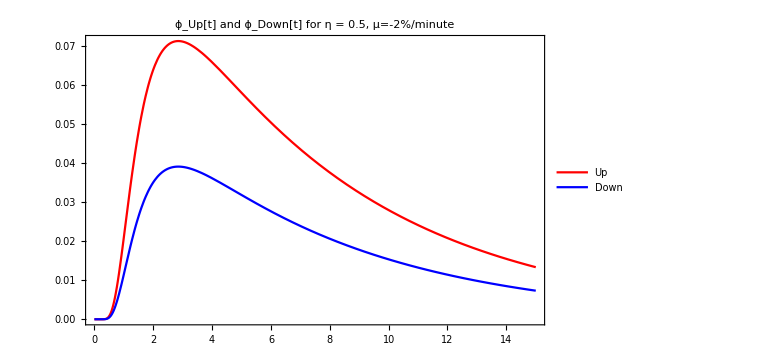

```mathematica
Module[{α=0.01,
σ=0.01/(√(24*3600)),
S=100,
η=0.5,
μ=0.005/(24*60)},
Plot[{
ϕtup[S,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000],
ϕtdown[S,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]},
{t,0,15},Frame->True,PlotRange->All,Filling->None,PlotStyle->{Red,Blue},
PlotLegends->{"Up","Down"},PlotLabel->"ϕ_Up[t] and ϕ_Down[t] for η = 0.5, μ=-2%/minute",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

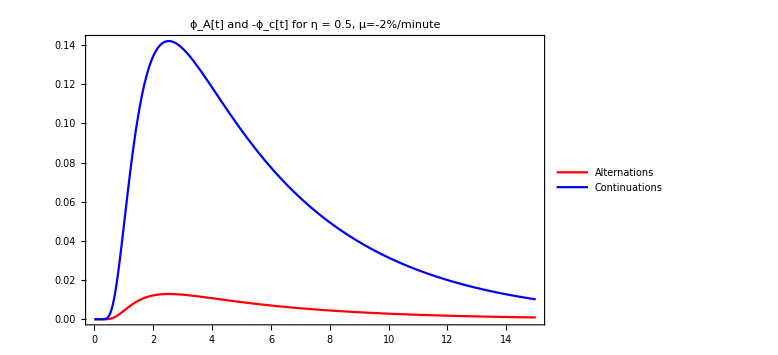

```mathematica
Module[{α=0.01,
σ=0.01/(√(24*3600)),
S=100,
η=0.5,
μ=-0.02/(24*60)},
Plot[{
ϕtup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10000],
ϕtdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10000]},
{t,0,15},Frame->True,PlotRange->All,Filling->None,PlotStyle->{Red,Blue},
PlotLegends->{"Alternations","Continuations"},PlotLabel->"ϕ_A[t] and ϕ_c[t] for η = 0.5, μ=-2%/minute",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

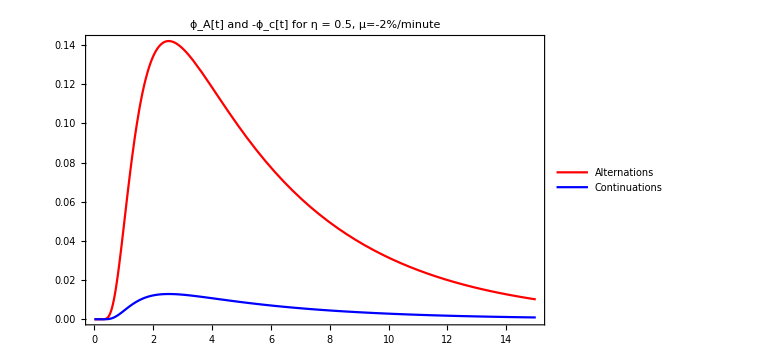

```mathematica
Module[{α=0.01,
σ=0.01/(√(24*3600)),
S=100,
η=0.5,
μ=-0.02/(24*60)},
Plot[{
ϕtdown[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10000],
ϕtup[S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10000]},
{t,0,15},Frame->True,PlotRange->All,Filling->None,PlotStyle->{Red,Blue},
PlotLegends->{"Alternations","Continuations"},PlotLabel->"ϕ_A[t] and ϕ_c[t] for η = 0.5, μ=-2%/minute",AxesOrigin->{0,0},Axes->True,ImageSize->Large]]
```

### 3.3.4 Conditional durations for the Uncertainty Zones model

#### 3.3.4 Mean durations

```mathematica
FullSimplify[Refine[Integrate[√(2π)ⅇ^(μ/σ^2(b-x0)) ns[((μ-1/2 σ^2)t)/(σ √t)]ns[x/(σ √t)] x/(σ √t),t],t≥0&&σ>0&&x<0&&b>0&&x0>0&&μ∈Reals]]
```

(ⅇ^(-(2 (-b+x0) μ+x Abs[-2 μ+σ^2])/(2 σ^2)) x (-1+Erf[(-2 x+t Abs[-2 μ+σ^2])/(2 √2 √t σ)]+ⅇ^((x Abs[-2 μ+σ^2])/σ^2) (1+Erf[(2 x+t Abs[-2 μ+σ^2])/(2 √2 √t σ)])))/Abs[-2 μ+σ^2]

```mathematica
(ⅇ^(-(2 (-b+x0) μ+x Abs[-2 μ+σ^2])/(2 σ^2)) x (-1+Erf[(-2 x+t Abs[-2 μ+σ^2])/(2 √2 √t σ)]+ⅇ^((x Abs[-2 μ+σ^2])/σ^2) (1+Erf[(2 x+t Abs[-2 μ+σ^2])/(2 √2 √t σ)])))/Abs[-2 μ+σ^2]
```

```mathematica
(ⅇ^(((b-x0) μ-x Abs[μ-1/2 σ^2])/σ^2) x (-1+Erf[(-x+t Abs[μ-1/2 σ^2])/(√2 √t σ)]+ⅇ^((2x Abs[μ-1/2 σ^2])/σ^2) (1+Erf[(x+t Abs[μ-1/2 σ^2])/(√2 √t σ)])))/(2Abs[μ-1/2 σ^2])
```

```mathematica
FullSimplify[D[(ⅇ^(-(2 (-b+x0) μ+x Abs[-2 μ+σ^2])/(2 σ^2)) x (-1+Erf[(-2 x+t Abs[-2 μ+σ^2])/(2 √2 √t σ)]+ⅇ^((x Abs[-2 μ+σ^2])/σ^2) (1+Erf[(2 x+t Abs[-2 μ+σ^2])/(2 √2 √t σ)])))/Abs[-2 μ+σ^2],t]]
```

(ⅇ^(-(4 x^2+8 t (-b+x0) μ+t^2 Abs[-2 μ+σ^2]^2)/(8 t σ^2)) x)/(√(2 π) √t σ)

```mathematica
FullSimplify[D[(ⅇ^(((b-x0) μ-x Abs[μ-1/2 σ^2])/σ^2) x (-1+Erf[(-x+t Abs[μ-1/2 σ^2])/(√2 √t σ)]+ⅇ^((2x Abs[μ-1/2 σ^2])/σ^2) (1+Erf[(x+t Abs[μ-1/2 σ^2])/(√2 √t σ)])))/(2Abs[μ-1/2 σ^2]),t]]
```

(ⅇ^(-(x^2+2 t (-b+x0) μ+t^2 Abs[μ-σ^2/2]^2)/(2 t σ^2)) x)/(√(2 π) √t σ)

```mathematica
?ϕtup
```

```mathematica
fintdurup[S0_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=Module[{x0,bu,bd,abst},
If[t==0,0,
x0=Log[S0];
bu=Log[Bu];
bd=Log[Bd];
abst=Abs[μ-1/2 σ^2];
yn[n_]:=+1*(2*(n-1)*bd-(2n-1)*bu+x0);
zn[n_]:=+1*(2*n*bd-(2n-1)*bu-x0);
Sum[Quiet[
(ⅇ^(((bu-x0) μ-zn[n] abst)/σ^2) zn[n] (-1+Erf[(-zn[n]+t abst)/(√2 √t σ)]+ⅇ^((2zn[n] abst)/σ^2) (1+Erf[(zn[n]+t abst)/(√2 √t σ)])))/(2abst)-
(ⅇ^(((bu-x0) μ-yn[n] abst)/σ^2) yn[n] (-1+Erf[(-yn[n]+t abst)/(√2 √t σ)]+ⅇ^((2yn[n] abst)/σ^2) (1+Erf[(yn[n]+t abst)/(√2 √t σ)])))/(2abst)],{n,1,nmax}]]];
```

```mathematica
fintdurdown[S0_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=
Module[{x0,bu,bd,abst},
If[t==0,0,
x0=Log[S0];
bu=Log[Bu];
bd=Log[Bd];
abst=Abs[μ-1/2 σ^2];
yn[n_]:=-1*(2*(n-1)*bu-(2n-1)*bd+x0);
zn[n_]:=-1*(2*n*bu-(2n-1)*bd-x0);
Sum[Quiet[
(ⅇ^(((bd-x0) μ-zn[n] abst)/σ^2) zn[n] (-1+Erf[(-zn[n]+t abst)/(√2 √t σ)]+ⅇ^((2zn[n] abst)/σ^2) (1+Erf[(zn[n]+t abst)/(√2 √t σ)])))/(2abst)-
(ⅇ^(((bd-x0) μ-yn[n] abst)/σ^2) yn[n] (-1+Erf[(-yn[n]+t abst)/(√2 √t σ)]+ⅇ^((2yn[n] abst)/σ^2) (1+Erf[(yn[n]+t abst)/(√2 √t σ)])))/(2abst)],{n,1,nmax}]]];
```

```mathematica
condduralt[S1_,S2_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=(fintdurup[S1,Bu,Bd,σ,t,μ,nmax]+fintdurdown[S2,Bu,Bd,σ,t,μ,nmax])/(Ptup[S1,Bu,Bd,σ,t,μ,nmax]+Ptdown[S2,Bu,Bd,σ,t,μ,nmax]);
```

```mathematica
conddurcont[S1_,S2_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=(fintdurdown[S1,Bu,Bd,σ,t,μ,nmax]+fintdurup[S2,Bu,Bd,σ,t,μ,nmax])/(2-Ptup[S1,Bu,Bd,σ,t,μ,nmax]-Ptdown[S2,Bu,Bd,σ,t,μ,nmax]);
```

```mathematica
(* conddurup[S1_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=fintdurup[S1,Bu,Bd,σ,t,μ,nmax]/Ptup[S1,Bu,Bd,σ,t,μ,nmax]; *)
```

```mathematica
(* unconddur[S1_,S2_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=(fintdurup[S1,Bu,Bd,σ,t,μ,nmax]+fintdurup[S2,Bu,Bd,σ,t,μ,nmax])/(Ptup[S1,Bu,Bd,σ,t,μ,nmax]+Ptup[S2,Bu,Bd,σ,t,μ,nmax]); *)
```

```mathematica
unconddur[S1_,S2_,Bu_,Bd_,σ_,t_,μ_:0,nmax_:nmaxd]:=(fintdurup[S1,Bu,Bd,σ,t,μ,nmax]+fintdurdown[S1,Bu,Bd,σ,t,μ,nmax]+fintdurup[S2,Bu,Bd,σ,t,μ,nmax]+fintdurdown[S2,Bu,Bd,σ,t,μ,nmax])/2;
```

```mathematica
Module[{S=100,α=0.01,η=0.5},
x0=Log[S+(1/2+η)α];
bu=Log[S+(1/2+η)α];
bd=Log[S-(1/2+η)α];
ynA[n_]:=+1*(2*(n-1)*bd-(2n-1)*bu+x0);
znA[n_]:=+1*(2*n*bd-(2n-1)*bu-x0);
ynC[n_]:=+1*(2*(n-1)*bd-(2n-1)*bu+x0);
znC[n_]:=+1*(2*n*bd-(2n-1)*bu-x0);
TableForm[Table[{n,ynA[n],znA[n],ynC[n],znC[n]},{n,1,10}]]]
```

1 | 0. | -0.0004 | 0. | -0.0004
2 | -0.0004 | -0.0008 | -0.0004 | -0.0008
3 | -0.0008 | -0.0012 | -0.0008 | -0.0012
4 | -0.0012 | -0.0016 | -0.0012 | -0.0016
5 | -0.0016 | -0.002 | -0.0016 | -0.002
6 | -0.002 | -0.0024 | -0.002 | -0.0024
7 | -0.0024 | -0.0028 | -0.0024 | -0.0028
8 | -0.0028 | -0.0032 | -0.0028 | -0.0032
9 | -0.0032 | -0.0036 | -0.0032 | -0.0036
10 | -0.0036 | -0.004 | -0.0036 | -0.004

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.5,μ=0},2η(α/(σ S))^2]
```

0.0001

Figure 15

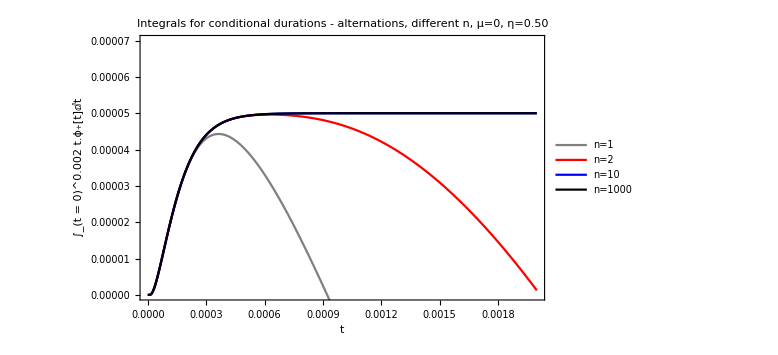

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.5,μ=0},DiscretePlot[
{fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1],
fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,2],
fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]},
{t,0,0.002,0.000002},Frame->True,PlotRange->{All,{0,0.7 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Gray,Red,Blue,Black},
Filling->None,PlotLegends->{"n=1","n=2","n=10","n=1000"},AxesOrigin->{0,0},PlotLabel->Style[Framed["Integrals for conditional durations - alternations, different n, μ=0, η=0.50"],14],FrameLabel->{Style[Framed["t"],12],Style[Framed["∫_(t = 0)^0.002 t.ϕ_+[t]ⅆt"],12]},ImageSize->Large]]
```

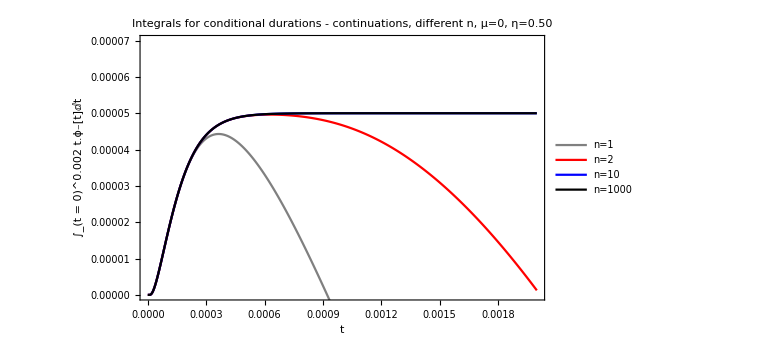

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.5,μ=0},DiscretePlot[
{fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1],
fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,2],
fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]},
{t,0,0.002,0.000002},Frame->True,PlotRange->{All,{0,0.7 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Gray,Red,Blue,Black},
Filling->None,PlotLegends->{"n=1","n=2","n=10","n=1000"},AxesOrigin->{0,0},PlotLabel->Style[Framed["Integrals for conditional durations - continuations, different n, μ=0, η=0.50"],14],FrameLabel->{Style[Framed["t"],12],Style[Framed["∫_(t = 0)^0.002 t.ϕ_-[t]ⅆt"],12]},ImageSize->Large]]
```

Figure 14

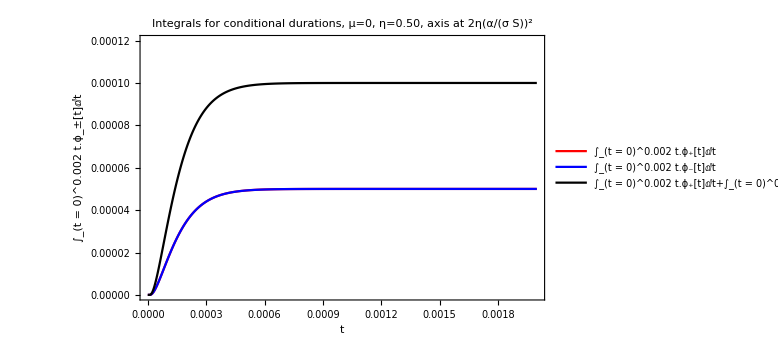

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.5,μ=0},DiscretePlot[
{fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10]+fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10]},
{t,0,0.002,0.000001},Frame->True,PlotRange->{All,{0,1.2 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Red,Blue,Black},
Filling->None,PlotLegends->Placed[{"∫_(t = 0)^0.002 t.ϕ_+[t]ⅆt","∫_(t = 0)^0.002 t.ϕ_-[t]ⅆt","∫_(t = 0)^0.002 t.ϕ_+[t]ⅆt+∫_(t = 0)^0.002 t.ϕ_-[t]ⅆt"},Bottom],AxesOrigin->{0,2η(α/(σ S))^2},Axes->True,PlotLabel->Style[Framed["Integrals for conditional durations, μ=0, η=0.50, axis at 2η(α/(σ S))^2"],14],FrameLabel->{Style[Framed["t"],12],Style[Framed["∫_(t = 0)^0.002 t.ϕ_±[t]ⅆt"],12]},ImageSize->Large]]
```

Figure 16

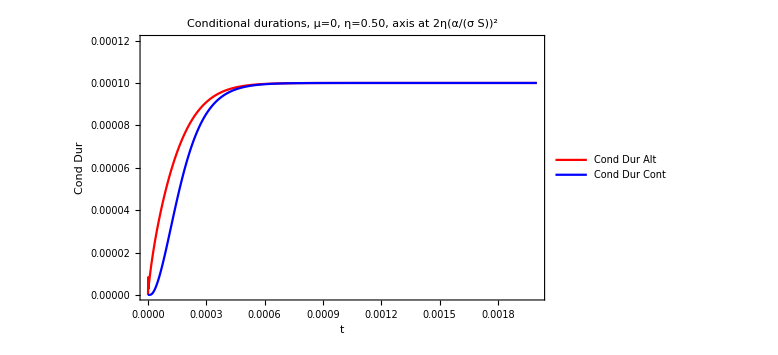

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.5,μ=0},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10]},
{t,0,0.002,0.000001},Frame->True,PlotRange->{All,{0,1.2 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt","Cond Dur Cont"},Bottom],AxesOrigin->{0,2η(α/(σ S))^2},Axes->True,PlotLabel->Style[Framed["Conditional durations, μ=0, η=0.50, axis at 2η(α/(σ S))^2"],14],FrameLabel->{Style[Framed["t"],12],Style[Framed["Cond Dur"],12]},ImageSize->Large]]
```

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.1,μ=0},2η(α/(σ S))^2]
```

0.00002

Figure 15

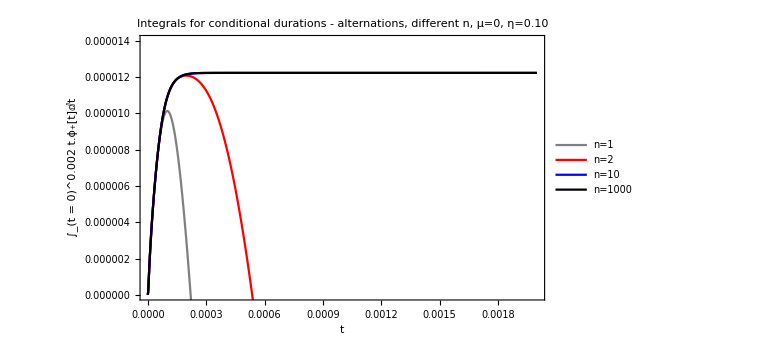

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.1,μ=0},DiscretePlot[
{fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1],
fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,2],
fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]},
{t,0,0.002,0.000002},Frame->True,PlotRange->{All,{0,0.7 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Gray,Red,Blue,Black},
Filling->None,PlotLegends->{"n=1","n=2","n=10","n=1000"},AxesOrigin->{0,0},PlotLabel->Style[Framed["Integrals for conditional durations - alternations, different n, μ=0, η=0.10"],14],FrameLabel->{Style[Framed["t"],12],Style[Framed["∫_(t = 0)^0.002 t.ϕ_+[t]ⅆt"],12]},ImageSize->Large]]
```

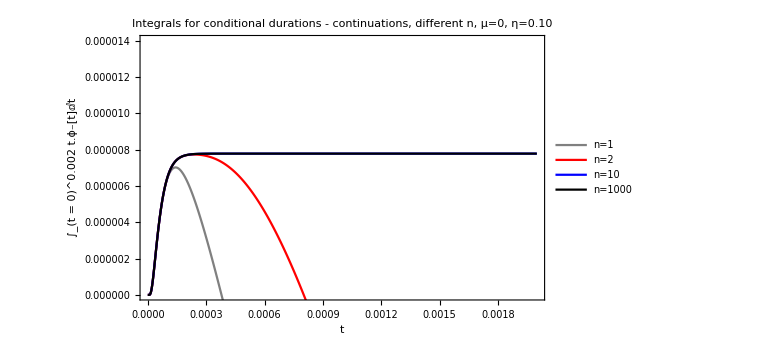

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.1,μ=0},DiscretePlot[
{fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1],
fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,2],
fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,1000]},
{t,0,0.002,0.000002},Frame->True,PlotRange->{All,{0,0.7 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Gray,Red,Blue,Black},
Filling->None,PlotLegends->{"n=1","n=2","n=10","n=1000"},AxesOrigin->{0,0},PlotLabel->Style[Framed["Integrals for conditional durations - continuations, different n, μ=0, η=0.10"],14],FrameLabel->{Style[Framed["t"],12],Style[Framed["∫_(t = 0)^0.002 t.ϕ_-[t]ⅆt"],12]},ImageSize->Large]]
```

Figure 14

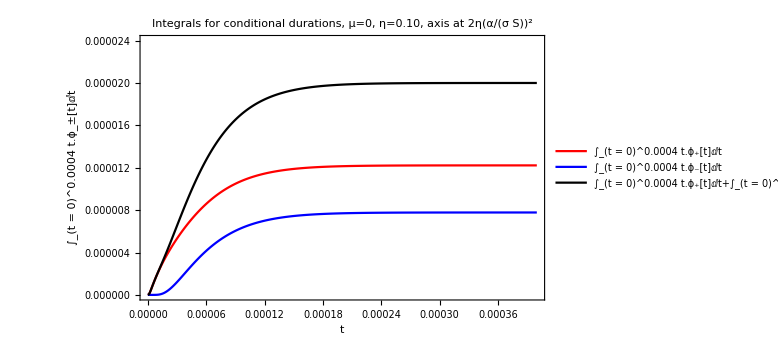

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.1,μ=0},DiscretePlot[
{fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
fintdurup[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10]+fintdurdown[S+(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10]},
{t,0,0.0004,0.000001},Frame->True,PlotRange->{All,{0,1.2 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Red,Blue,Black},
Filling->None,PlotLegends->Placed[{"∫_(t = 0)^0.0004 t.ϕ_+[t]ⅆt","∫_(t = 0)^0.0004 t.ϕ_-[t]ⅆt","∫_(t = 0)^0.0004 t.ϕ_+[t]ⅆt+∫_(t = 0)^0.0004 t.ϕ_-[t]ⅆt"},Bottom],AxesOrigin->{0,2η(α/(σ S))^2},Axes->True,PlotLabel->Style[Framed["Integrals for conditional durations, μ=0, η=0.10, axis at 2η(α/(σ S))^2"],14],FrameLabel->{Style[Framed["t"],12],Style[Framed["∫_(t = 0)^0.0004 t.ϕ_±[t]ⅆt"],12]},ImageSize->Large]]
```

Figure 16

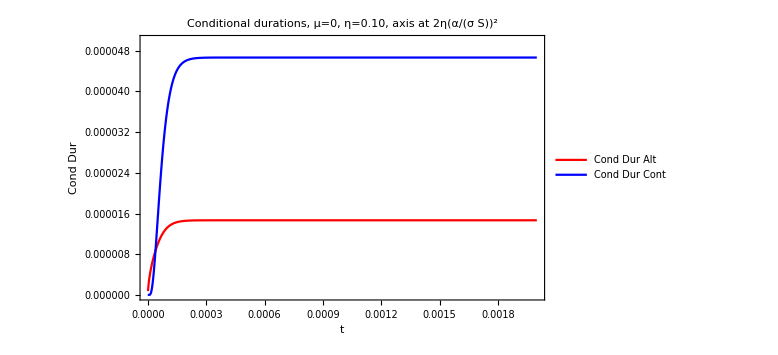

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.1,μ=0},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ,10]},
{t,0,0.002,0.000001},Frame->True,PlotRange->{All,{0,2.5 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt","Cond Dur Cont"},Bottom],AxesOrigin->{0,2η(α/(σ S))^2},Axes->True,PlotLabel->Style[Framed["Conditional durations, μ=0, η=0.10, axis at 2η(α/(σ S))^2"],14],FrameLabel->{Style[Framed["t"],12],Style[Framed["Cond Dur"],12]},ImageSize->Large]]
```

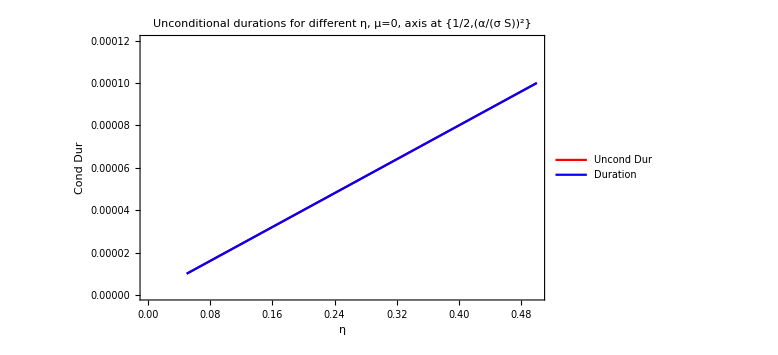

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=0},DiscretePlot[
{unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
2η(α/(σ S))^2},
{η,0.05,0.50,0.01},Frame->True,PlotRange->{All,{0,1.2 (α/(σ S))^2}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"Uncond Dur","Duration"},Bottom],AxesOrigin->{0.5,(α/(σ S))^2},Axes->True,PlotLabel->Style[Framed["Unconditional durations for different η, μ=0, axis at {1/2,(α/(σ S))^2}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Cond Dur"],12]},ImageSize->Large]]
```

Figure 18

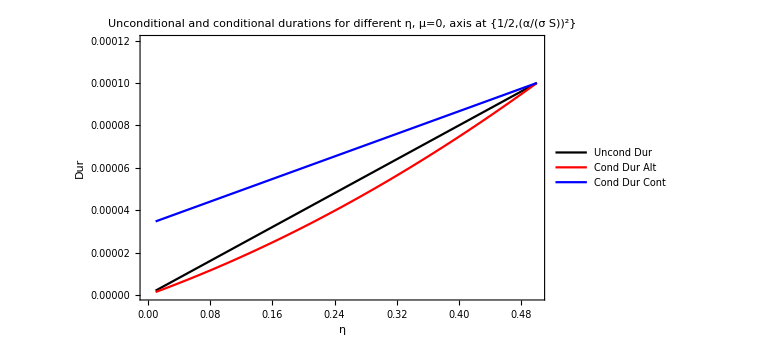

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=0},DiscretePlot[
{unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]},
{η,0.01,0.50,0.01},Frame->True,PlotRange->{All,{0,1.2 (α/(σ S))^2}},Joined->True,PlotStyle->{Black,Red,Blue},
Filling->None,PlotLegends->Placed[{"Uncond Dur","Cond Dur Alt","Cond Dur Cont"},Bottom],AxesOrigin->{0.5,(α/(σ S))^2},Axes->True,PlotLabel->Style[Framed["Unconditional and conditional durations for different η, μ=0, axis at {1/2,(α/(σ S))^2}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Dur"],12]},ImageSize->Large]]
```

Figure 17

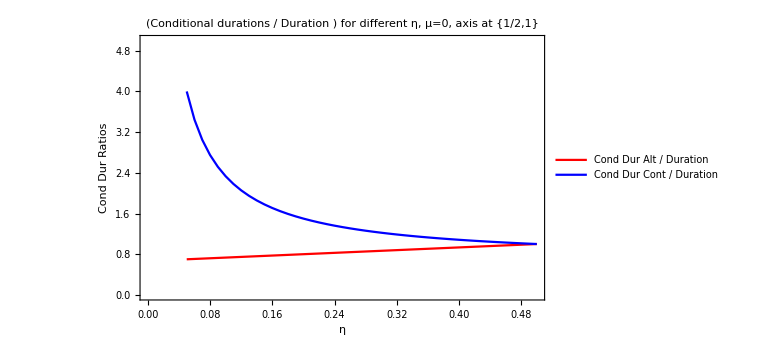

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=0},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/(2η(α/(σ S))^2),
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/(2η(α/(σ S))^2)},
{η,0.05,0.50,0.01},Frame->True,PlotRange->{All,{0,5}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt / Duration", "Cond Dur Cont / Duration"},Bottom],AxesOrigin->{0.5,1},Axes->True,PlotLabel->Style[Framed["(Conditional durations / Duration ) for different η, μ=0, axis at {1/2,1}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Cond Dur Ratios"],12]},ImageSize->Large]]
```

Figure 17

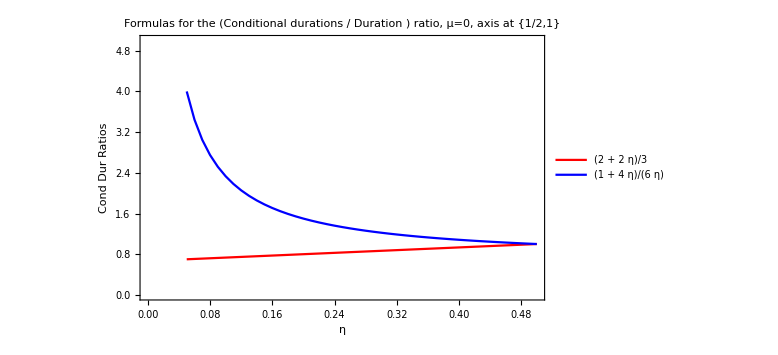

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=0},DiscretePlot[
{(2+2η)/3,
(1+4η)/(6η)},
{η,0.05,0.50,0.01},Frame->True,PlotRange->{All,{0,5}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"(2 + 2  η)/3", "(1 + 4  η)/(6  η)"},Bottom],AxesOrigin->{0.5,1},Axes->True,PlotLabel->Style[Framed["Formulas for the (Conditional durations / Duration ) ratio, μ=0, axis at {1/2,1}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Cond Dur Ratios"],12]},ImageSize->Large]]
```

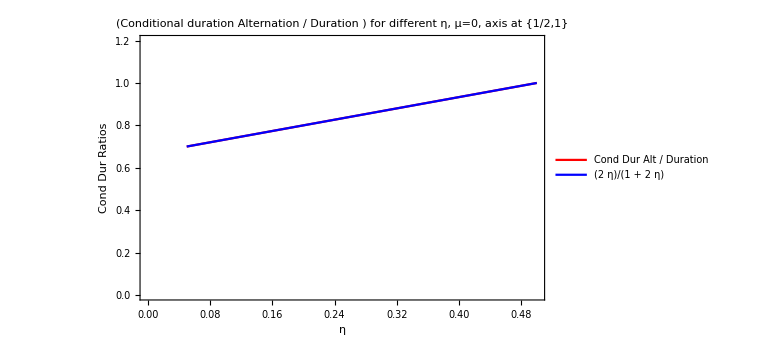

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=0},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/(2η(α/(σ S))^2),(2+2η)/3},
{η,0.05,0.50,0.01},Frame->True,PlotRange->{All,{0,1.2}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt / Duration", "(2  η)/(1 + 2  η)"},Bottom],AxesOrigin->{0.5,1},Axes->True,PlotLabel->Style[Framed["(Conditional duration Alternation / Duration ) for different η, μ=0, axis at {1/2,1}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Cond Dur Ratios"],12]},ImageSize->Large]]
```

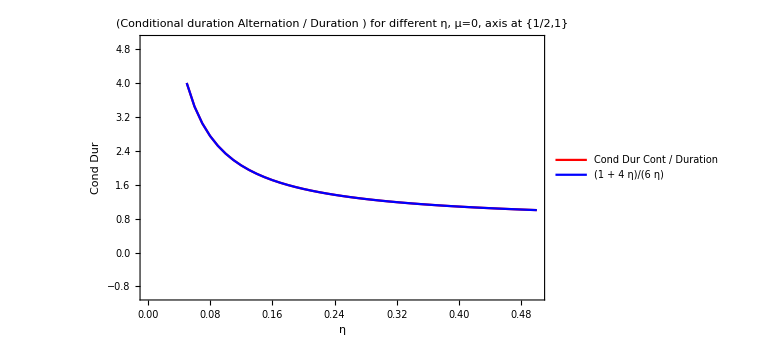

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=0},DiscretePlot[
{conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/(2η(α/(σ S))^2),(1+4η)/(6η)},
{η,0.05,0.50,0.01},Frame->True,PlotRange->{All,{-1,5}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"Cond Dur Cont / Duration", "(1 + 4  η)/(6  η)"},Bottom],AxesOrigin->{0.5,1},Axes->True,PlotLabel->Style[Framed["(Conditional duration Alternation / Duration ) for different η, μ=0, axis at {1/2,1}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Cond Dur"],12]},ImageSize->Large]]
```

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=0},FindFit[Table[{η,conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/(2η(α/(σ S))^2)},
{η,0.05,0.50,0.01}],a+b/η,{a,b},η]]
```

{a→0.666667,b→0.166667}

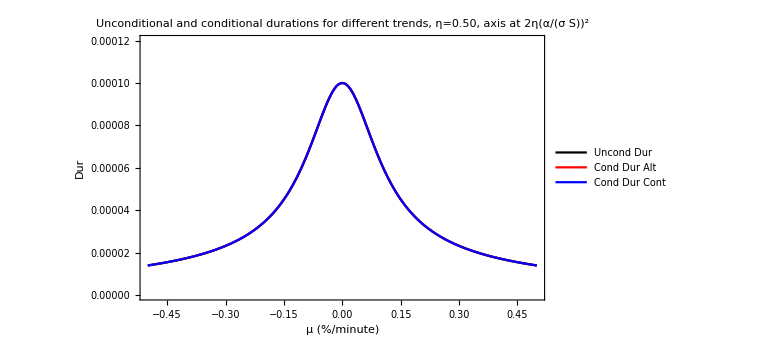

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.5,t=0.002},DiscretePlot[
{unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]},
{μ,-0.5,+0.5,0.005},Frame->True,PlotRange->{All,{0,1.2 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Black,Red,Blue},
Filling->None,PlotLegends->Placed[{"Uncond Dur","Cond Dur Alt","Cond Dur Cont"},Bottom],AxesOrigin->{0,2η(α/(σ S))^2},Axes->True,PlotLabel->Style[Framed["Unconditional and conditional durations for different trends, η=0.50, axis at 2η(α/(σ S))^2"],14],FrameLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["Dur"],12]},ImageSize->Large]]
```

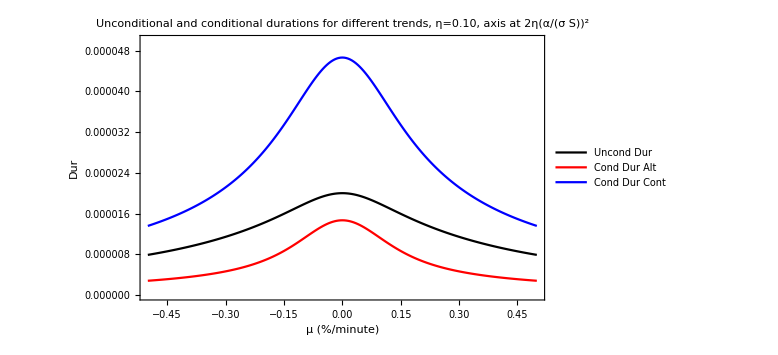

```mathematica
Module[{S=100,α=0.01,σ=0.01,η=0.1,t=0.002},DiscretePlot[
{unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]},
{μ,-0.5,+0.5,0.005},Frame->True,PlotRange->{All,{0,2.5 2η(α/(σ S))^2}},Joined->True,PlotStyle->{Black,Red,Blue},
Filling->None,PlotLegends->Placed[{"Uncond Dur","Cond Dur Alt","Cond Dur Cont"},Bottom],AxesOrigin->{0,2η(α/(σ S))^2},Axes->True,PlotLabel->Style[Framed["Unconditional and conditional durations for different trends, η=0.10, axis at 2η(α/(σ S))^2"],14],FrameLabel->{Style[Framed["μ (%/minute)"],12],Style[Framed["Dur"],12]},ImageSize->Large]]
```

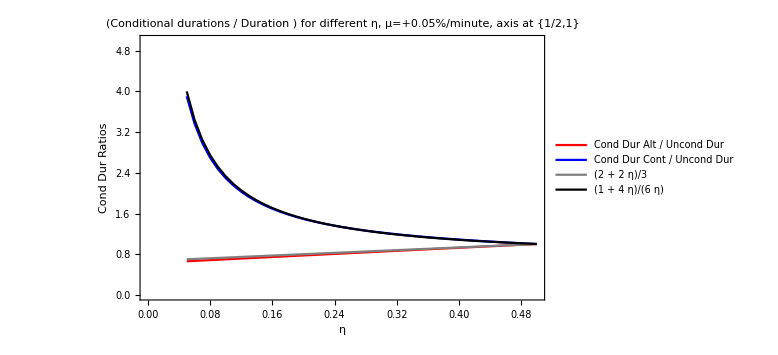

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=+0.05},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
(2+2η)/3,(1+4η)/(6η)},
{η,0.05,0.50,0.01},Frame->True,PlotRange->{All,{0,5}},Joined->True,PlotStyle->{Red,Blue,Gray,Black},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt / Uncond Dur", "Cond Dur Cont / Uncond Dur","(2 + 2  η)/3", "(1 + 4  η)/(6  η)"},Bottom],AxesOrigin->{0.5,1},Axes->True,PlotLabel->Style[Framed["(Conditional durations / Duration ) for different η, μ=+0.05%/minute, axis at {1/2,1}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Cond Dur Ratios"],12]},ImageSize->Large]]
```

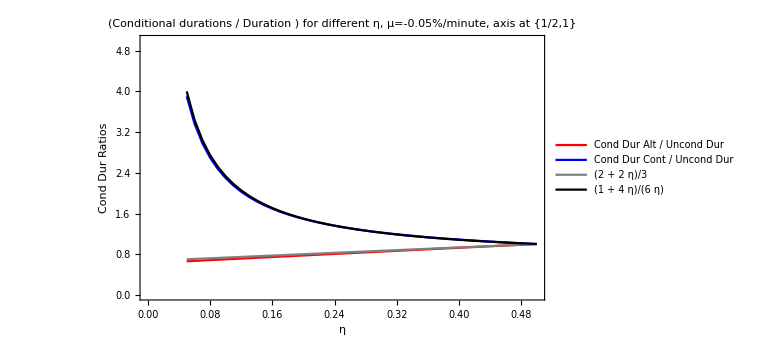

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=-0.05},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
(2+2η)/3,(1+4η)/(6η)},
{η,0.05,0.50,0.01},Frame->True,PlotRange->{All,{0,5}},Joined->True,PlotStyle->{Red,Blue,Gray,Black},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt / Uncond Dur", "Cond Dur Cont / Uncond Dur","(2 + 2  η)/3", "(1 + 4  η)/(6  η)"},Bottom],AxesOrigin->{0.5,1},Axes->True,PlotLabel->Style[Framed["(Conditional durations / Duration ) for different η, μ=-0.05%/minute, axis at {1/2,1}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Cond Dur Ratios"],12]},ImageSize->Large]]
```

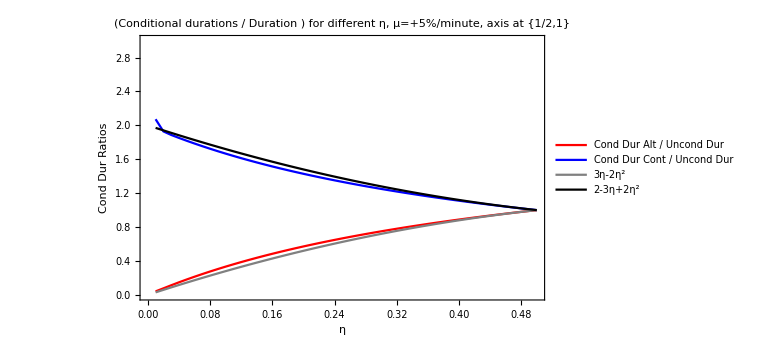

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,μ=+5},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
3η-2 η^2,2-3η+2 η^2},
{η,0.01,0.50,0.01},Frame->True,PlotRange->{All,{0,3}},Joined->True,PlotStyle->{Red,Blue,Gray,Black},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt / Uncond Dur", "Cond Dur Cont / Uncond Dur","3η-2η^2", "2-3η+2η^2"},Bottom],AxesOrigin->{0.5,1},Axes->True,PlotLabel->Style[Framed["(Conditional durations / Duration ) for different η, μ=+5%/minute, axis at {1/2,1}"],14],FrameLabel->{Style[Framed["η"],12],Style[Framed["Cond Dur Ratios"],12]},ImageSize->Large]]
```

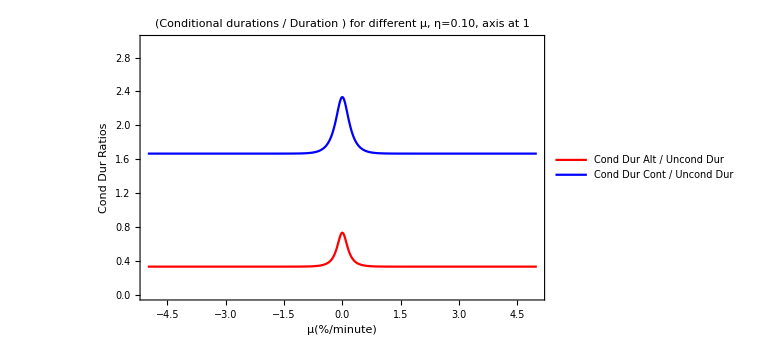

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,η=0.1},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]},
{μ,-5.0,+5.0,0.005},Frame->True,PlotRange->{All,{0,3}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt / Uncond Dur", "Cond Dur Cont / Uncond Dur"},Bottom],AxesOrigin->{0,1},Axes->True,PlotLabel->Style[Framed["(Conditional durations / Duration ) for different μ, η=0.10, axis at 1"],14],FrameLabel->{Style[Framed["μ(%/minute)"],12],Style[Framed["Cond Dur Ratios"],12]},ImageSize->Large]]
```

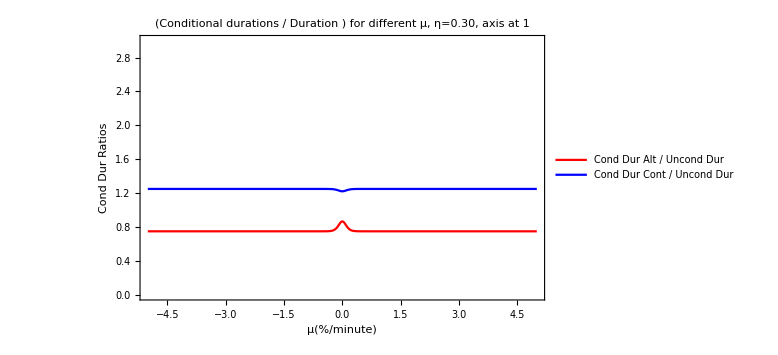

```mathematica
Module[{S=100,α=0.01,σ=0.01,t=0.002,η=0.3},DiscretePlot[
{condduralt[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20],
conddurcont[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]/unconddur[S+(1/2-η)α,S-(1/2-η)α,S+(1/2+η)α,S-(1/2+η)α,σ,t,μ*(24*60)/100,20]},
{μ,-5.0,+5.0,0.005},Frame->True,PlotRange->{All,{0,3}},Joined->True,PlotStyle->{Red,Blue},
Filling->None,PlotLegends->Placed[{"Cond Dur Alt / Uncond Dur", "Cond Dur Cont / Uncond Dur"},Bottom],AxesOrigin->{0,1},Axes->True,PlotLabel->Style[Framed["(Conditional durations / Duration ) for different μ, η=0.30, axis at 1"],14],FrameLabel->{Style[Framed["μ(%/minute)"],12],Style[Framed["Cond Dur Ratios"],12]},ImageSize->Large]]
```

## Old stuff

```mathematica
PUp0[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=P[1,S,S,α,η,σ,t,μ,nmax];
PDown0[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=P[-1,S,S,α,η,σ,t,μ,nmax];
P0[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=PUp0[S,α,η,σ,t,μ,nmax]+PDown0[S,α,η,σ,t,μ,nmax];PCUp[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=P[1,S-(1/2-η)α,S,α,η,σ,t,μ,nmax];PCDown[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=P[-1,S+(1/2-η)α,S,α,η,σ,t,μ,nmax];PAUp[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=P[1,S+(1/2-η)α,S,α,η,σ,t,μ,nmax];PADown[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=P[-1,S-(1/2-η)α,S,α,η,σ,t,μ,nmax];PC[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=PCUp[S,α,η,σ,t,μ,nmax]+PCDown[S,α,η,σ,t,μ,nmax];PA[S_,α_,η_,σ_,t_,μ_:0,nmax_:nmaxd]:=PAUp[S,α,η,σ,t,μ,nmax]+PADown[S,α,η,σ,t,μ,nmax];
```

```mathematica
PTUp0[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[1,S,S,α,η,σ,1,μ,nmax];
PTDown0[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[-1,S,S,α,η,σ,1,μ,nmax];
PT0[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=PTUp0[S,α,η,σ,μ,nmax]+PTDown0[S,α,η,σ,μ,nmax];PTCUp[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[1,S-(1/2-η)α,S,α,η,σ,1,μ,nmax];PTCDown[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[-1,S+(1/2-η)α,S,α,η,σ,1,μ,nmax];PTAUp[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[1,S+(1/2-η)α,S,α,η,σ,1,μ,nmax];PTADown[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[-1,S-(1/2-η)α,S,α,η,σ,1,μ,nmax];PTC[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=PTCUp[S,α,η,σ,μ,nmax]+PTCDown[S,α,η,σ,μ,nmax];PTA[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=PTAUp[S,α,η,σ,μ,nmax]+PTADown[S,α,η,σ,μ,nmax];
```

```mathematica
PTP0[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[2(UnitStep[μ]-1/2),S,S,α,η,σ,1,μ,nmax];
PTN0[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[-2(UnitStep[μ]-1/2),S,S,α,η,σ,1,μ,nmax];
PTCP[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[2(UnitStep[μ]-1/2),S-2(UnitStep[μ]-1/2)(1/2-η)α,S,α,η,σ,1,μ,nmax];
PTCN[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[-2(UnitStep[μ]-1/2),S+2(UnitStep[μ]-1/2)(1/2-η)α,S,α,η,σ,1,μ,nmax];PTAP[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[2(UnitStep[μ]-1/2),S+2(UnitStep[μ]-1/2)(1/2-η)α,S,α,η,σ,1,μ,nmax];PTAN[S_,α_,η_,σ_,μ_:0,nmax_:nmaxd]:=P[-2(UnitStep[μ]-1/2),S-2(UnitStep[μ]-1/2)(1/2-η)α,S,α,η,σ,1,μ,nmax];
```

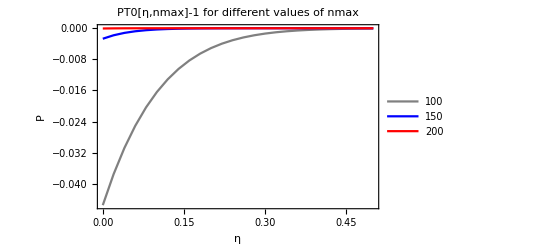

```mathematica
α=0.01;
σ=0.01;
S=100;
ω=0;
DiscretePlot[{
PT0[S,α,η,σ,ω,100]-1,
PT0[S,α,η,σ,ω,150]-1,
PT0[S,α,η,σ,ω,200]-1},
{η,0,0.5,0.02},Frame->True,PlotRange->All,PlotStyle->{Gray,Blue,Red},Filling->None,Joined->True,
PlotLegends->{100,150,200},AxesLabel->{"η","P"},PlotLabel->"PT0[η,nmax]-1 for different values of nmax",AxesOrigin->{0,0}]
```

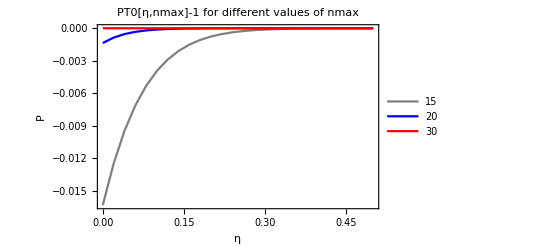

```mathematica
α=0.01;
σ=0.00125;
S=100;
ω=0;
DiscretePlot[{
PT0[S,α,η,σ,ω,15]-1,
PT0[S,α,η,σ,ω,20]-1,
PT0[S,α,η,σ,ω,30]-1},
{η,0,0.5,0.02},Frame->True,PlotRange->All,PlotStyle->{Gray,Blue,Red},Filling->None,Joined->True,
PlotLegends->{15,20,30},AxesLabel->{"η","P"},PlotLabel->"PT0[η,nmax]-1 for different values of nmax",AxesOrigin->{0,0}]
```

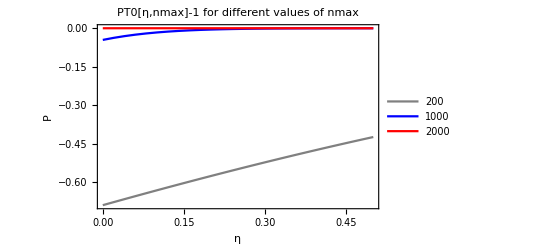

```mathematica
α=0.001;
σ=0.01;
S=100;
ω=0;
DiscretePlot[{
PT0[S,α,η,σ,ω,200]-1,
PT0[S,α,η,σ,ω,1000]-1,
PT0[S,α,η,σ,ω,2000]-1},
{η,0,0.5,0.02},Frame->True,PlotRange->All,PlotStyle->{Gray,Blue,Red},Filling->None,Joined->True,
PlotLegends->{200,1000,2000},AxesLabel->{"η","P"},PlotLabel->"PT0[η,nmax]-1 for different values of nmax",AxesOrigin->{0,0}]
```

```mathematica
roundP[ud_,S0_,S_,α_,η_,σ_,t_,ω_:0,ϵ_:0.01,nmax_:nmaxd]:=Module[{maxp},
If[t==0,0,
maxp=P[ud,S0,S,α,η,σ,1,ω,nmax];
Round[P[ud,S0,S,α,η,σ,t,ω,nmax]/maxp,ϵ]]
];
```

```mathematica
draw[function_,prevpts_,n_]:=Module[{bounds,rnds,pts},
bounds={0,Max[Map[First,prevpts]]};
rnds=RandomReal[bounds,n];
pts=Sort[Join[prevpts,ParallelMap[{#,function[#]}&,rnds]]];
DeleteDuplicatesBy[pts,Last]];
```

```mathematica
Ppoints[ud_,S0_,S_,α_,η_,σ_,ω_:0,nrnd_:20,ϵ_:0.01,nmax_:nmaxd]:=
NestWhileList[draw[roundP[ud,S0,S,α,η,σ,#,ω,ϵ,nmax]&,#,nrnd]&,{{0,0},{1,1.}},(Length[#]≤1/ϵ+1)&];
```

```mathematica
testicdf=RandomVariate[NormalDistribution[],100^2];
```

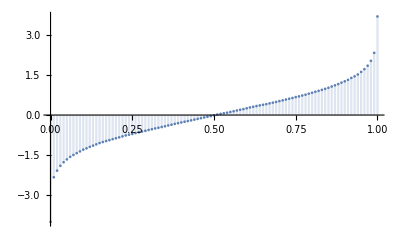

```mathematica
DiscretePlot[InverseCDF[EmpiricalDistribution[testicdf],y],{y,0,1,0.01}]
```

```mathematica
Timing[P[1,100,100,0.01,0.2,0.01,1,0]]
```

{0.10083,0.5}

```mathematica
Timing[Table[P[1,100,100,0.01,0.2,0.01,1,0, 2000],{j,10}]]
```

{8.48642,{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}}

```mathematica
Timing[ParallelTable[P[1,100,100,0.01,0.2,0.01,1,0, 2000],{j,10}]]
```

{3.56735,{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}}

```mathematica
Timing[Parallelize[Table[P[1,100,100,0.01,0.2,0.01,1,0, 2000],{j,10}]]]
```

{0.121334,{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}}

```mathematica
Timing[testpcdf=Parallelize[Table[P[1,100,100,0.01,0.2,0.01,0.000001j,0],{j,1,500}]]/0.5]
```

{6.20776,{5.12803×10^-12,1.48747×10^-6,0.000106303,0.000930911,0.00349142,0.00853584,0.0163058,0.0266622,0.0392685,0.0537222,0.0696272,0.0866279,0.10442,0.122751,0.141417,0.160252,0.179126,0.197936,0.216602,0.235062,0.253269,0.271189,0.288794,0.306066,0.322991,0.339563,0.355775,0.371627,0.387118,0.402251,0.417029,0.431456,0.445539,0.459282,0.472692,0.485776,0.498539,0.51099,0.523135,0.534981,0.546534,0.557802,0.568791,0.579507,0.589959,0.600151,0.61009,0.619783,0.629235,0.638452,0.647441,0.656206,0.664753,0.673088,0.681216,0.689141,0.69687,0.704407,0.711756,0.718923,0.725911,0.732726,0.739371,0.745851,0.75217,0.758332,0.76434,0.7702,0.775913,0.781485,0.786918,0.792216,0.797382,0.80242,0.807332,0.812123,0.816794,0.821349,0.825791,0.830122,0.834346,0.838465,0.842481,0.846397,0.850216,0.85394,0.857572,0.861113,0.864566,0.867934,0.871217,0.874419,0.877542,0.880586,0.883555,0.886451,0.889274,0.892027,0.894711,0.897329,0.899882,0.902371,0.904798,0.907166,0.909474,0.911724,0.913919,0.91606,0.918147,0.920182,0.922166,0.924101,0.925989,0.927829,0.929623,0.931373,0.933079,0.934743,0.936366,0.937948,0.939491,0.940995,0.942462,0.943893,0.945288,0.946648,0.947974,0.949268,0.950529,0.951759,0.952959,0.954128,0.955269,0.956381,0.957466,0.958523,0.959554,0.96056,0.961541,0.962497,0.963429,0.964339,0.965225,0.96609,0.966933,0.967755,0.968557,0.969339,0.970101,0.970844,0.971569,0.972276,0.972965,0.973638,0.974293,0.974932,0.975555,0.976163,0.976756,0.977334,0.977897,0.978447,0.978983,0.979505,0.980015,0.980512,0.980996,0.981469,0.98193,0.982379,0.982817,0.983244,0.983661,0.984067,0.984463,0.984849,0.985226,0.985594,0.985952,0.986301,0.986642,0.986974,0.987298,0.987613,0.987921,0.988222,0.988515,0.9888,0.989079,0.98935,0.989615,0.989873,0.990125,0.99037,0.99061,0.990843,0.991071,0.991293,0.991509,0.991721,0.991926,0.992127,0.992323,0.992514,0.9927,0.992881,0.993058,0.993231,0.993399,0.993563,0.993723,0.99388,0.994032,0.99418,0.994325,0.994466,0.994603,0.994738,0.994868,0.994996,0.99512,0.995242,0.99536,0.995475,0.995588,0.995698,0.995805,0.995909,0.996011,0.99611,0.996207,0.996301,0.996393,0.996483,0.99657,0.996655,0.996738,0.99682,0.996899,0.996976,0.997051,0.997124,0.997196,0.997265,0.997333,0.9974,0.997464,0.997527,0.997589,0.997649,0.997707,0.997764,0.99782,0.997874,0.997927,0.997979,0.998029,0.998078,0.998126,0.998172,0.998218,0.998262,0.998305,0.998347,0.998388,0.998428,0.998468,0.998506,0.998543,0.998579,0.998614,0.998649,0.998682,0.998715,0.998747,0.998778,0.998809,0.998838,0.998867,0.998895,0.998923,0.99895,0.998976,0.999001,0.999026,0.99905,0.999074,0.999097,0.999119,0.999141,0.999163,0.999183,0.999204,0.999223,0.999243,0.999262,0.99928,0.999298,0.999315,0.999332,0.999349,0.999365,0.999381,0.999396,0.999411,0.999426,0.99944,0.999454,0.999468,0.999481,0.999494,0.999506,0.999519,0.999531,0.999542,0.999554,0.999565,0.999576,0.999586,0.999596,0.999607,0.999616,0.999626,0.999635,0.999644,0.999653,0.999662,0.99967,0.999678,0.999686,0.999694,0.999702,0.999709,0.999716,0.999723,0.99973,0.999737,0.999744,0.99975,0.999756,0.999762,0.999768,0.999774,0.999779,0.999785,0.99979,0.999796,0.999801,0.999806,0.99981,0.999815,0.99982,0.999824,0.999829,0.999833,0.999837,0.999841,0.999845,0.999849,0.999853,0.999856,0.99986,0.999863,0.999867,0.99987,0.999873,0.999876,0.999879,0.999882,0.999885,0.999888,0.999891,0.999894,0.999896,0.999899,0.999901,0.999904,0.999906,0.999909,0.999911,0.999913,0.999915,0.999917,0.999919,0.999921,0.999923,0.999925,0.999927,0.999929,0.999931,0.999932,0.999934,0.999936,0.999937,0.999939,0.99994,0.999942,0.999943,0.999945,0.999946,0.999947,0.999949,0.99995,0.999951,0.999953,0.999954,0.999955,0.999956,0.999957,0.999958,0.999959,0.99996,0.999961,0.999962,0.999963,0.999964,0.999965,0.999966,0.999967,0.999967,0.999968,0.999969,0.99997,0.999971,0.999971,0.999972,0.999973,0.999973,0.999974,0.999975,0.999975,0.999976,0.999977,0.999977,0.999978,0.999978,0.999979,0.999979,0.99998,0.99998,0.999981,0.999981,0.999982,0.999982,0.999983,0.999983,0.999984,0.999984,0.999984,0.999985,0.999985,0.999985,0.999986,0.999986,0.999987,0.999987,0.999987,0.999988,0.999988,0.999988,0.999988,0.999989,0.999989,0.999989,0.99999,0.99999,0.99999,0.99999,0.999991,0.999991,0.999991,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999993,0.999993,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999996,0.999996}}

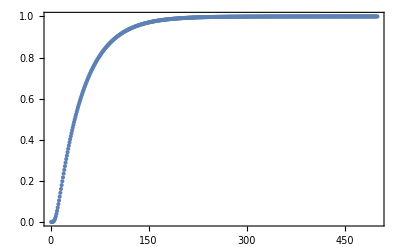

```mathematica
ListPlot[testpcdf,Frame->True,PlotRange->All]
```

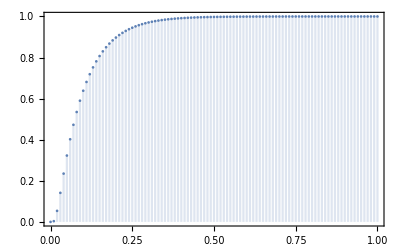

```mathematica
DiscretePlot[InverseCDF[EmpiricalDistribution[testpcdf],y],{y,0,1,0.01},Frame->True,PlotRange->All]
```

```mathematica
Timing[FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.000930911,{t,0.000005,0,1}]]
```

{1.27222,{t→4.×10^-6}}

```mathematica
Timing[FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.000930911,{t,0.00001,0,1}]]
```

{1.78006,{t→4.×10^-6}}

```mathematica
Timing[FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.000930911,{t,0.000001,0,1}]]
```

{2.24657,{t→4.×10^-6}}

```mathematica
Timing[FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.01,{t,0.000001,0,1}]]
```

{2.37665,{t→6.21833×10^-6}}

```mathematica
Timing[FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.01,{t,0.00001,0,1}]]
```

{1.23667,{t→6.21833×10^-6}}

```mathematica
Timing[FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.5,{t,0.000001,0,1}]]
```

{2.89942,{t→0.000037116}}

```mathematica
Timing[FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.5,{t,0.00001,0,1}]]
```

{1.05031,{t→0.000037116}}

```mathematica
TableForm[Table[{m,FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.01,{t,10^m,0,1}]},{m,-8,-2}]]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-8}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-7}. Try perturbing the initial point(s).

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {t} = {-1.35525×10^-20}.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {0.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

-8 | t→1.×10^-8
-7 | t→1.×10^-7
-6 | t→6.21833×10^-6
-5 | t→6.21833×10^-6
-4 | t→0.0001
-3 | t→0.
-2 | t→0.

```mathematica
TableForm[Table[{m,FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.5,{t,10^m,0,1}]},{m,-8,-2}]]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-8}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-7}. Try perturbing the initial point(s).

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {t} = {-1.35525×10^-20}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {t} = {-1.73472×10^-18}.

-8 | t→1.×10^-8
-7 | t→1.×10^-7
-6 | t→0.000037116
-5 | t→0.000037116
-4 | t→0.0001
-3 | t→0.000037116
-2 | t→0.01

```mathematica
TableForm[Table[{m,FindRoot[P[1,100,100,0.01,0.2,0.01,t,0]/0.5==0.99,{t,10^m,0,1}]},{m,-8,-2}]]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-8}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-7}. Try perturbing the initial point(s).

FindRoot::reged: The point {1.} is at the edge of the search region {0.,1.} in coordinate 1 and the computed search direction points outside the region.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {t} = {-5.42101×10^-20}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-8 | t→1.×10^-8
-7 | t→1.×10^-7
-6 | t→1.
-5 | t→0.000192501
-4 | t→0.000192501
-3 | t→0.00038742
-2 | t→0.01

```mathematica
TableForm[Table[{m,FindRoot[P[1,100,100,0.01,0.2,0.00125,t,0]/0.5==0.5,{t,10^m,0,1}]},{m,-8,-2}]]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-8}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-7}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {1.×10^-6}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

General::munfl: (4.33425×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.35464×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

-8 | t→1.×10^-8
-7 | t→1.×10^-7
-6 | t→1.×10^-6
-5 | t→0.00001
-4 | t→0.00237543
-3 | t→0.00237543
-2 | t→0.00237543

```mathematica
AbsoluteTiming[points25=Ppoints[1,100,100,0.01,0.2,0.01,0,25,0.01,200];]
```

{35.7514,Null}

```mathematica
Timing[points20=Ppoints[1,100,100,0.01,0.2,0.01];]
```

General::munfl: (3.51316×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.70603×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.12387×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{254.656,Null}

```mathematica
Timing[points15=Ppoints[1,100,100,0.01,0.2,0.01,0,15];]
```

General::munfl: (3.44845×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.56213×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.22973×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{259.648,Null}

```mathematica
Timing[points10=Ppoints[1,100,100,0.01,0.2,0.01,0,10];]
```

General::munfl: (4.08713×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.25571×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.20346×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{181.125,Null}

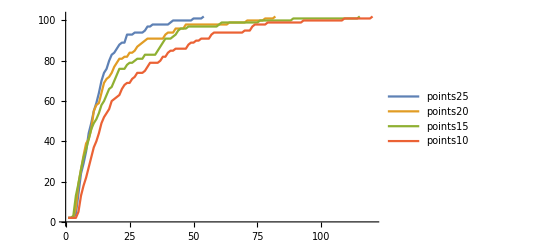

```mathematica
ListLinePlot[{Map[Length,points25],Map[Length,points20],Map[Length,points15],Map[Length,points10]},PlotLegends->{"points25","points20","points15","points10"}]
```

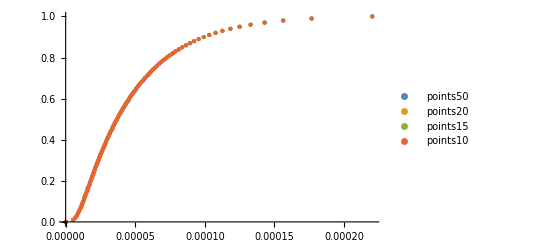

```mathematica
ListPlot[{Last[points25],Last[points20],Last[points15],Last[points10]},PlotRange->All,PlotLegends->{"points50","points20","points15","points10"}]
```

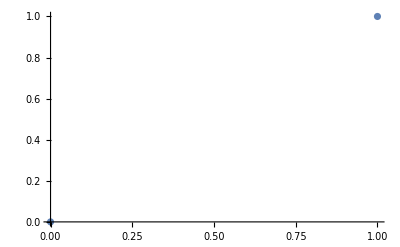
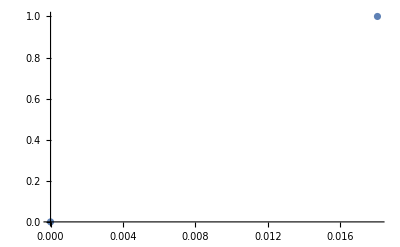
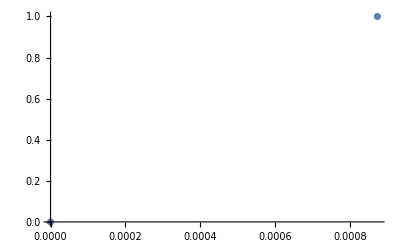
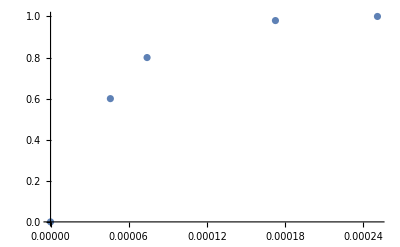
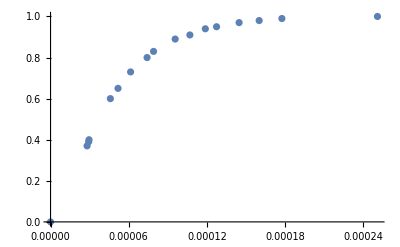
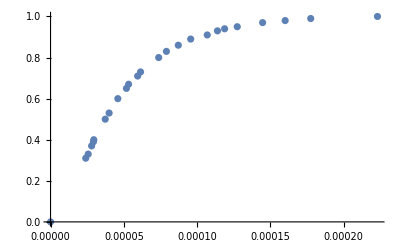
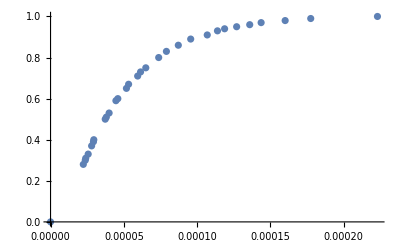
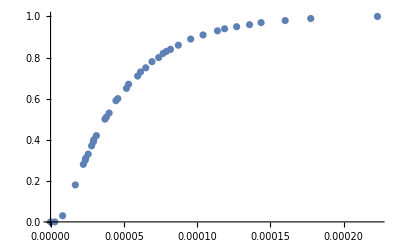
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListPlot,points20]
```

```mathematica
α=0.01;
σ=0.00125;
S=100;
η=0.5;
nmax=50;
Plot[{PTP0[S,α,η,σ,ω,nmax],PTN0[S,α,η,σ,ω,nmax]},
{ω,-0.03,0.03},Frame->True,PlotRange->All,PlotStyle->{Blue,Red},
AxesLabel->{"ω","P"},PlotLabel->"PTP0[η=0.5,ω,σ=0.00125] and PTN0[η=0.5,ω,σ=0.00125]",AxesOrigin->{0,0.5},PlotLegends->"Expressions"]
```

General::munfl: (4.40541×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.40673×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
α=0.01;
σ=0.00125;
S=100;
η=0.1;
nmax=50;
Plot[{PTP0[S,α,η,σ,ω,nmax],PTN0[S,α,η,σ,ω,nmax]},
{ω,-0.05,0.05},Frame->True,PlotRange->All,PlotStyle->{Blue,Red},
AxesLabel->{"ω","P"},PlotLabel->"PTP0[η=0.1,ω,σ=0.00125] and PTN0[η=0.1,ω,σ=0.00125]",AxesOrigin->{0,0.5},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
α=0.01;
σ=0.00125;
S=100;
nmax=50;
Plot3D[
PTP0[S,α,η,σ,ω,nmax],
{η,0,0.5},{ω,-0.03,0.03},PlotRange->All,AxesLabel->{"η","ω","P"},PlotLabel->"PTP0[η,ω,σ=0.00125]",ImageSize->Large]
```

-Graphics3D-

```mathematica
α=0.01;
η=0.5;
S=100;
nmax=200;
Plot3D[
PTP0[S,α,η,σ,ω,nmax],
{σ,0.001,0.01},{ω,-0.03,0.03},PlotRange->All,AxesLabel->{"σ","ω","P"},PlotLabel->"PTP0[η=0.5,ω,σ]",ImageSize->Large]
```

General::munfl: Exp[-709.996] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.988] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-721.979] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
α=0.01;
η=0.5;
S=100;
nmax=200;
Plot3D[
{PTCP[S,α,η,σ,ω,nmax],PTCN[S,α,η,σ,ω,nmax]},
{σ,0.001,0.01},{ω,-0.03,0.03},PlotRange->All,AxesLabel->{"σ","ω","P"},PlotLabel->"PTCP[η=0.5,ω,σ] and PTCN[η=0.5,ω,σ]",ImageSize->Large,PlotLegends->"Expressions",PlotStyle->{Darker[Blue],Lighter[Blue]}]
```

General::munfl: Exp[-709.996] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.988] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-721.979] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
α=0.01;
η=0.5;
S=100;
nmax=200;
Plot3D[
{PTAP[S,α,η,σ,ω,nmax],PTAN[S,α,η,σ,ω,nmax]},
{σ,0.001,0.01},{ω,-0.03,0.03},PlotRange->All,AxesLabel->{"σ","ω","P"},PlotLabel->"PTAP[η=0.5,ω,σ] and PTAN[η=0.5,ω,σ]",ImageSize->Large,PlotLegends->"Expressions",PlotStyle->{Darker[Red],Lighter[Red]}]
```

General::munfl: Exp[-709.996] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.988] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-721.979] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
α=0.01;
η=0.5;
S=100;
nmax=200;
Plot3D[
{PTCP[S,α,η,σ,ω,nmax],PTAP[S,α,η,σ,ω,nmax]},
{σ,0.001,0.01},{ω,-0.03,0.03},PlotRange->All,AxesLabel->{"σ","ω","P"},PlotLabel->"PTCP[η=0.5,ω,σ] and PTAP[η=0.5,ω,σ]",ImageSize->Large,PlotLegends->"Expressions",PlotStyle->{Darker[Blue],Darker[Red]}]
```

General::munfl: Exp[-709.996] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.988] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-721.979] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
α=0.01;
η=0.5;
S=100;
nmax=200;
Plot3D[
{PTCN[S,α,η,σ,ω,nmax],PTAN[S,α,η,σ,ω,nmax]},
{σ,0.001,0.01},{ω,-0.03,0.03},PlotRange->All,AxesLabel->{"σ","ω","P"},PlotLabel->"PTCN[η=0.5,ω,σ] and PTAN[η=0.5,ω,σ]",ImageSize->Large,PlotLegends->"Expressions",PlotStyle->{Lighter[Blue],Lighter[Red]}]
```

General::munfl: Exp[-709.996] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.988] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-721.979] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
α=0.01;
η=0.1;
S=100;
nmax=200;
Plot3D[
{PTCP[S,α,η,σ,ω,nmax],PTAP[S,α,η,σ,ω,nmax]},
{σ,0.001,0.01},{ω,-0.03,0.03},PlotRange->All,AxesLabel->{"σ","ω","P"},PlotLabel->"PTCP[η=0.1,ω,σ] and PTAP[η=0.1,ω,σ]",ImageSize->Large,PlotLegends->"Expressions",PlotStyle->{Darker[Blue],Darker[Red]}]
```

General::munfl: Exp[-708.798] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.789] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.988] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
α=0.01;
η=0.1;
S=100;
nmax=200;
Plot3D[
{PTCN[S,α,η,σ,ω,nmax],PTAN[S,α,η,σ,ω,nmax]},
{σ,0.001,0.01},{ω,-0.03,0.03},PlotRange->All,AxesLabel->{"σ","ω","P"},PlotLabel->"PTCN[η=0.1,ω,σ] and PTAN[η=0.1,ω,σ]",ImageSize->Large,PlotLegends->"Expressions",PlotStyle->{Lighter[Blue],Lighter[Red]}]
```

General::munfl: Exp[-708.798] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.789] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.988] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[η]
```

```mathematica
fv[j_]:=UnitStep[j-3/2](-1)^j((Quotient[j+2,4]-1/2)+(-1)^Quotient[j,2] η);
fvc[j_]:=2UnitStep[j-3/2](-1)^j((Quotient[j+2,4]-1/2)+(-1)^Quotient[j,2] 1/4);
```

```mathematica
(* TableForm[Table[{j,fv[j],2Quotient[j-2,4],fvc[j]},{j,13}]] *)
```

```mathematica
fpmat[S_,α_,σ_,ω_,η_,level_,nmax_:200]:=Module[{n,ptp0,ptn0,ptcup,ptaup,ptcdown,ptadown},
n=4level+1;
ptp0=PTUp0[S,α,η,σ,ω,nmax];
ptn0=1-ptp0;
ptcup=PTCUp[S,α,η,σ,ω,nmax];
ptaup=PTAUp[S,α,η,σ,ω,nmax];
ptcdown=PTCDown[S,α,η,σ,ω,nmax];
ptadown=PTADown[S,α,η,σ,ω,nmax];
SparseArray[{
{1,4}->ptp0,{1,5}->ptn0,
{2,4}->ptaup,{2,5}->ptcdown,
{3,4}->ptcup,{3,5}->ptadown,
{i_,j_}/;And[i≥4,Mod[i,4]==0,j==4Quotient[i,4]-2+Boole[OddQ[i]]]->ptadown,
{i_,j_}/;And[i≥4,Mod[i,4]==0,j==4Quotient[i,4]+4+Boole[OddQ[i]]]->ptcup,
{i_,j_}/;And[i≥4,Mod[i,4]==1,j==4Quotient[i,4]-2+Boole[OddQ[i]]]->ptaup,
{i_,j_}/;And[i≥4,Mod[i,4]==1,j==4Quotient[i,4]+4+Boole[OddQ[i]]]->ptcdown,
{i_,j_}/;And[i≥4,Mod[i,4]==2,j==4Quotient[i,4]-2+Boole[OddQ[i]]]->ptcdown,
{i_,j_}/;And[i≥4,Mod[i,4]==2,j==4Quotient[i,4]+4+Boole[OddQ[i]]]->ptaup,
{i_,j_}/;And[i≥4,Mod[i,4]==3,j==4Quotient[i,4]-2+Boole[OddQ[i]]]->ptcup,
{i_,j_}/;And[i≥4,Mod[i,4]==3,j==4Quotient[i,4]+4+Boole[OddQ[i]]]->ptadown
},
{n,n}]];
```

```mathematica
(* MatrixForm[fpmat[100,0.01,0.01,0,0.5,3]] *)
```

```mathematica
fmp[S_,α_,σ_,ω_,η_,level_,nmax_:200]:=Module[{n,init,ptp0,ptn0,ptcup,ptaup,ptcdown,ptadown,tmat},
n=4level+1;
init=Prepend[ConstantArray[0,n-1],1];
ptp0=PTUp0[S,α,η,σ,ω,nmax];
ptn0=1-ptp0;
ptcup=PTCUp[S,α,η,σ,ω,nmax];
ptaup=PTAUp[S,α,η,σ,ω,nmax];
ptcdown=PTCDown[S,α,η,σ,ω,nmax];
ptadown=PTADown[S,α,η,σ,ω,nmax];
tmat=SparseArray[{
{1,4}->ptp0,{1,5}->ptn0,
{2,4}->ptaup,{2,5}->ptcdown,
{3,4}->ptcup,{3,5}->ptadown,
{i_,j_}/;And[i≥4,Mod[i,4]==0,j==4Quotient[i,4]-2+Boole[OddQ[i]]]->ptadown,
{i_,j_}/;And[i≥4,Mod[i,4]==0,j==4Quotient[i,4]+4+Boole[OddQ[i]]]->ptcup,
{i_,j_}/;And[i≥4,Mod[i,4]==1,j==4Quotient[i,4]-2+Boole[OddQ[i]]]->ptaup,
{i_,j_}/;And[i≥4,Mod[i,4]==1,j==4Quotient[i,4]+4+Boole[OddQ[i]]]->ptcdown,
{i_,j_}/;And[i≥4,Mod[i,4]==2,j==4Quotient[i,4]-2+Boole[OddQ[i]]]->ptcdown,
{i_,j_}/;And[i≥4,Mod[i,4]==2,j==4Quotient[i,4]+4+Boole[OddQ[i]]]->ptaup,
{i_,j_}/;And[i≥4,Mod[i,4]==3,j==4Quotient[i,4]-2+Boole[OddQ[i]]]->ptcup,
{i_,j_}/;And[i≥4,Mod[i,4]==3,j==4Quotient[i,4]+4+Boole[OddQ[i]]]->ptadown
},
{n,n}];
DiscreteMarkovProcess[init,tmat]];
```

```mathematica
Clear[fmpred]
```

```mathematica
fmpred[S_,α_,σ_,ω_,η_,nmax_:200]:=Module[{init,ptp0,ptn0,ptcup,ptaup,ptcdown,ptadown,tmat},
init={1,0,0,0,0};
ptp0=PTUp0[S,α,η,σ,ω,nmax];
ptn0=1-ptp0;
ptcup=PTCUp[S,α,η,σ,ω,nmax];
ptaup=PTAUp[S,α,η,σ,ω,nmax];
ptcdown=PTCDown[S,α,η,σ,ω,nmax];
ptadown=PTADown[S,α,η,σ,ω,nmax];
tmat=
{{0,ptp0,ptn0,0,0},
{0,0,0,ptadown,ptcup},
{0,0,0,ptaup,ptcdown},
{0,ptaup,ptadown,0,0},
{0,ptcup,ptcdown,0,0}};
DiscreteMarkovProcess[init,tmat]];
```

```mathematica
etafmpred[S_,α_,σ_,ω_,η_,nmax_:200]:=Module[{init,ptp0,ptn0,ptcup,ptaup,ptcdown,ptadown,tmat,proc,probs},
init={1,0,0,0,0};
ptp0=PTUp0[S,α,η,σ,ω,nmax];
ptn0=1-ptp0;
ptcup=PTCUp[S,α,η,σ,ω,nmax];
ptaup=PTAUp[S,α,η,σ,ω,nmax];
ptcdown=PTCDown[S,α,η,σ,ω,nmax];
ptadown=PTADown[S,α,η,σ,ω,nmax];
tmat=
{{0,ptp0,ptn0,0,0},
{0,0,0,ptadown,ptcup},
{0,0,0,ptaup,ptcdown},
{0,ptaup,ptadown,0,0},
{0,ptcup,ptcdown,0,0}};
proc=DiscreteMarkovProcess[init,tmat];
probs=Chop[Table[PDF[StationaryDistribution[proc],j],{j,5}]];
probs⟦5⟧/(2*probs⟦4⟧)
];
```

```mathematica
DiscretePlot3D[etafmpred[100,0.01,σ,ω,0.3],{σ,0.001,0.01,0.001},{ω,-0.02,0.02,0.001},AxesLabel->Automatic]
```

General::munfl: (4.26627×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.48837×10^-278 4.68327×10^-33 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.23729×10^-279 6.77733×10^-34 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

-Graphics3D-

```mathematica
DiscretePlot3D[etafmpred[100,0.01,σ,ω,0.3]-0.3,{σ,0.0015,0.01,0.0005},{ω,-0.02,0.02,0.001},AxesLabel->Automatic,ImageSize->Large]
```

General::munfl: 2.94099×10^-204 8.81151×10^-106 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.09285×10^-205 8.51233×10^-107 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7104×10^-205 8.12893×10^-108 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

-Graphics3D-

```mathematica
DiscretePlot3D[etafmpred[100,0.01,σ,ω,0.2]-0.2,{σ,0.0015,0.01,0.0005},{ω,-0.02,0.02,0.001},AxesLabel->Automatic,ImageSize->Large]
```

General::munfl: 3.21456×10^-204 1.01944×10^-105 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.26014×10^-205 1.32041×10^-106 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.66778×10^-205 1.69567×10^-107 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

-Graphics3D-

```mathematica
DiscretePlot3D[etafmpred[100,0.01,σ,0,η]-η,{σ,0.001,0.01,0.0005},{η,0.05,0.50,0.05},AxesLabel->Automatic,ImageSize->Large]
```

General::munfl: (4.2667×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.42994×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.26686×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

-Graphics3D-

```mathematica
DiscretePlot3D[etafmpred[100,0.01,σ,0.01,η]-η,{σ,0.001,0.01,0.0005},{η,0.05,0.50,0.05},AxesLabel->Automatic,ImageSize->Large]
```

General::munfl: 3.96122×10^-158 4.0224×10^-152 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.31869×10^-158 2.21958×10^-153 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.38964×10^-159 1.20987×10^-154 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

-Graphics3D-

```mathematica
DiscretePlot3D[etafmpred[100,0.01,σ,0.01,η]-η,{σ,0.0015,0.005,0.0005},{η,0.05,0.50,0.05},AxesLabel->Automatic,ImageSize->Large]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::munfl: (2.71032×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.71046×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

General::munfl: 7.35841×10^-108 1.66391×10^-202 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
DiscretePlot3D[etafmpred[100,0.005,σ,0.01,η]-η,{σ,0.0015,0.005,0.0005},{η,0.05,0.50,0.05},AxesLabel->Automatic,ImageSize->Large]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

-Graphics3D-

```mathematica
DiscretePlot3D[etafmpred[100,0.02,σ,0.01,η]-η,{σ,0.0015,0.005,0.0005},{η,0.05,0.50,0.05},AxesLabel->Automatic,ImageSize->Large]
```

General::munfl: 6.16016×10^-108 7.40018×10^-203 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.31725×10^-108 8.47379×10^-205 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.71767×10^-109 9.50155×10^-207 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

-Graphics3D-

```mathematica
DiscretePlot3D[etafmpred[100,0.02,σ,0.01,η]/η-1,{σ,0.0015,0.005,0.0005},{η,0.05,0.50,0.05},AxesLabel->Automatic,ImageSize->Large]
```

General::munfl: 6.16016×10^-108 7.40018×10^-203 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.31725×10^-108 8.47379×10^-205 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.71767×10^-109 9.50155×10^-207 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

-Graphics3D-

```mathematica
reduced0=DiscreteMarkovProcess[
{1,0,0,0,0},
{{0,1/2,1/2,0,0},
{0,0,0,1/(1+2η),(2η)/(1+2η)},
{0,0,0,1/(1+2η),(2η)/(1+2η)},
{0,1/2,1/2,0,0},
{0,1/2,1/2,0,0}}]
```

DiscreteMarkovProcess[{1,0,0,0,0},{{0,1/2,1/2,0,0},{0,0,0,1/(1+2 η),(2 η)/(1+2 η)},{0,0,0,1/(1+2 η),(2 η)/(1+2 η)},{0,1/2,1/2,0,0},{0,1/2,1/2,0,0}}]

```mathematica
MarkovProcessProperties[reduced0]
```

Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0,0,0,0,0}
HoldingTimeVariance | {0,0,0,0,0}
Structural Properties | 
CommunicatingClasses | {2,3,4,5}, {1}
RecurrentClasses | {2,3,4,5}
TransientClasses | {1}
AbsorbingClasses | None
PeriodicClasses | {2,3,4,5}
Periods | {2,∞}
Irreducible | False
Primitive | False
Aperiodic | False
Transient Properties | 
TransientVisitMean | {1}
TransientVisitVariance | {0}
TransientTotalVisitMean | 1
Limiting Properties | 
ReachabilityProbability | {0,1,1,1,1}
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
FullSimplify[StationaryDistribution[reduced0]]
```

ProbabilityDistribution[((1+2 η) Boole[x==2]+(1+2 η) Boole[x==3]+2 Boole[x==4]+4 η Boole[x==5])/(4+8 η),{x,1,5,1}]

```mathematica
Graph[reduced0]
```

-Graphics-

```mathematica
dmp=fmp[100,0.01,0.01,0,0.5,20];
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

```mathematica
(* MarkovProcessProperties[dmp] *)
```

```mathematica
(* Graph[dmp] *)
```

```mathematica
simul=RandomFunction[dmp,{0,1000},1000];
```

```mathematica
ListLinePlot[First[simul["Paths"]],PlotRange->All,Frame->True]
```

-Graphics-

```mathematica
(* N[Map[MatrixForm,estproc=EstimatedProcess[simul,DiscreteMarkovProcess[13]]],3] *)
```

```mathematica
fmat[level_]:=Module[{n},
n=4level+1;
SparseArray[{
{i_,j_}/;And[i≤3,4≤j≤5]->1,
{i_,j_}/;And[i≥4,Or[j==4Quotient[i,4]-2+Boole[OddQ[i]],j==4Quotient[i,4]+4+Boole[OddQ[i]]]]->1},
{n,n}]];
```

```mathematica
(* MatrixForm[fmat[3]] *)
```

```mathematica
(* ArrayPlot[fmat[10]] *)
```

```mathematica
AdjacencyGraph[
((fmat[3])),DirectedEdges->True,VertexLabels->Table[j->fv[j],{j,13}],VertexCoordinates->Table[{2Quotient[j-2,4],fvc[j]},{j,13}]]
```

-Graphics-

```mathematica
lookup[pdf_,y_]:=First[SelectFirst[pdf,Last[#]==y&]];
```

```mathematica
nextinpath[{t_,st_,x_,p_},{S_,α_,η_,ϵ_},
{ptp0_,tpp0_,ptn0_,tpn0_,ptcup_,tpcup_,
ptaup_,tpaup_,ptcdown_,tpcdown_,ptadown_,tpadown_}]:=Module[
{rnd,choice,choicecdft,newtp,dt,newt,newst,newx,newp},
rnd=RandomReal[];
choice=Which[
st==1,{ptp0,{4,5}},
st==2,{ptaup,{4,5}},
st==3,{ptcup,{4,5}},
Mod[st,4]==0,{ptadown,{4Quotient[st,4]-2+Boole[OddQ[st]],4Quotient[st,4]+4+Boole[OddQ[st]]}},
Mod[st,4]==1,{ptaup,{4Quotient[st,4]-2+Boole[OddQ[st]],4Quotient[st,4]+4+Boole[OddQ[st]]}},
Mod[st,4]==2,{ptcdown,{4Quotient[st,4]-2+Boole[OddQ[st]],4Quotient[st,4]+4+Boole[OddQ[st]]}},
Mod[st,4]==3,{ptcup,{4Quotient[st,4]-2+Boole[OddQ[st]],4Quotient[st,4]+4+Boole[OddQ[st]]}}];
choicecdft=Which[
st==1,{ptp0,{tpp0,tpn0}},
st==2,{ptaup,{tpaup,tpcdown}},
st==3,{ptcup,{tpcup,tpadown}},
Mod[st,4]==0,{ptadown,{tpadown,tpcup}},
Mod[st,4]==1,{ptaup,{tpaup,tpcdown}},
Mod[st,4]==2,{ptcdown,{tpcdown,tpaup}},
Mod[st,4]==3,{ptcup,{tpcup,tpadown}}];
newst=If[rnd≤choice⟦1⟧,choice⟦2,1⟧,choice⟦2,2⟧];
newtp=If[rnd≤choicecdft⟦1⟧,choicecdft⟦2,1⟧,choicecdft⟦2,2⟧];
dt=lookup[newtp,Round[rnd,ϵ]];
newt=t+dt;
newx=S+UnitStep[st-3/2](-1)^st((Quotient[st+2,4]-1/2)+(-1)^Quotient[st,2] η)α;
newp=S+(-1)^st Quotient[st,4]α;
{newt,newst,newx,newp}
];
```

```mathematica
Clear[fpath]
```

```mathematica
fpath[S_,α_,σ_,ω_,η_,lpath_:50,npaths_:1,nrnd_:20,ϵ_:0.01,nmax_:200]:=Module[
{ptp0,tpp0,ptn0,tpn0,ptcup,tpcup,
ptaup,tpaup,ptcdown,tpcdown,ptadown,tpadown,init},
Print[{S,α,σ,ω,η,lpath,npaths,nrnd,ϵ,nmax}];
ptp0=PTUp0[S,α,η,σ,ω,nmax];
ptn0=1-ptp0;
ptcup=PTCUp[S,α,η,σ,ω,nmax];
ptaup=PTAUp[S,α,η,σ,ω,nmax];
ptcdown=PTCDown[S,α,η,σ,ω,nmax];
ptadown=PTADown[S,α,η,σ,ω,nmax];
Print[{ptp0,ptn0,ptcup,ptaup,ptcdown,ptadown}];
tpp0=Last[Ppoints[1,S,S,α,η,σ,ω,nrnd,ϵ,nmax]];
Print["tpp0"];
tpn0=Last[Ppoints[-1,S,S,α,η,σ,ω,nrnd,ϵ,nmax]];
Print["tpn0"];
tpcup=Last[Ppoints[1,S-(1/2-η)α,S,α,η,σ,ω,nrnd,ϵ,nmax]];
Print["tpcup"];
tpaup=Last[Ppoints[1,S+(1/2-η)α,S,α,η,σ,ω,nrnd,ϵ,nmax]];
Print["tpaup"];
tpcdown=Last[Ppoints[-1,S+(1/2-η)α,S,α,η,σ,ω,nrnd,ϵ,nmax]];
Print["tpcdown"];
tpadown=Last[Ppoints[-1,S-(1/2-η)α,S,α,η,σ,ω,nrnd,ϵ,nmax]];
Print["tpadown"];
init={0,1,S,S};
(*
Table[
NestList[nextinpath[#,{S,α,η,ϵ},{ptp0,tpp0,ptn0,tpn0,ptcup,tpcup,ptaup,tpaup,ptcdown,tpcdown,ptadown,tpadown}]&,init,lpath],{npaths}]
*)
Table[
NestWhileList[nextinpath[#,{S,α,η,ϵ},{ptp0,tpp0,ptn0,tpn0,ptcup,tpcup,ptaup,tpaup,ptcdown,tpcdown,ptadown,tpadown}]&,init,(First[#]≤1)&],{npaths}]

];
```

```mathematica
Timing[pointstest=Ppoints[1,100,100,0.01,0.2,0.01,0,15,0.01,200];]
```

General::munfl: (2.53597×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.67482×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.39478×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{246.514,Null}

```mathematica
lookup[Last[pointstest],0.45]
```

0.0000330751

```mathematica
Timing[pathstest=fpath[100,0.01,0.01,0,0.2,10,1000,20,0.01,200];]
```

{100,0.01,0.01,0,0.2,10,1000,20,0.01,200}

{0.5,0.5,0.285714,0.714286,0.285714,0.714286}

General::munfl: (4.32744×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.980419 2.25107×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.32596×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

tpp0

tpn0

tpcup

tpaup

tpcdown

tpadown

{3208.86,Null}

```mathematica
For[
j=1,
j<1001,
j++,
Export[StringJoin["pathstest",ToString[j],".csv"],pathstest⟦j⟧];
Print[j]]
```

```mathematica
ListLinePlot[Map[{First[#],Last[#]}&,Take[pathstest,5],{2}]]
```

-Graphics-

```mathematica
ListLinePlot[Map[{First[#],Last[#]}&,Map[Take[#,50]&,Take[pathstest,5]],{2}]]
```

-Graphics-

```mathematica
ListLinePlot[Map[{First[#],Last[#]}&,Map[Take[#,-20]&,Take[pathstest,5]],{2}]]
```

```mathematica
Plot[{1/(1+2η),(2η)/(1+2η)},{η,0,1/2},Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
eta=0.5;
alpha=0.01;
vol=0.0025;
spot=100;
Plot[{
P[1,spot,spot,alpha,eta,vol,t,0,100],
-P[-1,spot,spot,alpha,eta,vol,t,0,100],
P[1,spot,spot,alpha,eta,vol,t,-0.01,100],
-P[-1,spot,spot,alpha,eta,vol,t,-0.01,100]},
{t,0,1},Frame->True,PlotRange->All,
PlotLabel->StringJoin["η=",ToString[eta]],
PlotStyle->{Red,Blue,Darker[Red],Darker[Blue]},
PlotLegends->{
"S => S+(1/2+η)α",
"S => S-(1/2+η)α",
"New: S => S+(1/2+η)α, μ=-0.01",
"New: S => S-(1/2+η)α, μ=-0.01"}]
```

-Graphics-

```mathematica
eta=0.5;
alpha=0.01;
vol=0.0025;
spot=100;
Plot[{
P[1,spot,spot,alpha,eta,vol,t,0,100],
-P[-1,spot,spot,alpha,eta,vol,t,0,100],
P[1,spot,spot,alpha,eta,vol,t,-0.01,100],
-P[-1,spot,spot,alpha,eta,vol,t,-0.01,100]},
{t,0,1},Frame->True,PlotRange->All,
PlotLabel->StringJoin["η=",ToString[eta]],
PlotStyle->{Red,Blue,Darker[Red],Darker[Blue]},
PlotLegends->{
"S => S+(1/2+η)α",
"S => S-(1/2+η)α",
"New: S => S+(1/2+η)α, μ=-0.01",
"New: S => S-(1/2+η)α, μ=-0.01"}]
```

-Graphics-

```mathematica
eta=0.5;
alpha=0.01;
vol=0.0025;
spot=100;
Plot[{
P[1,spot+(1/2-eta)alpha,spot,alpha,eta,vol,t,0,100],
-P[-1,spot+(1/2-eta)alpha,spot,alpha,eta,vol,t,0,100],
P[1,spot+(1/2-eta)alpha,spot,alpha,eta,vol,t,-0.01,100],
-P[-1,spot+(1/2-eta)alpha,spot,alpha,eta,vol,t,-0.01,100]},
{t,0,1},Frame->True,PlotRange->All,
PlotLabel->StringJoin["η=",ToString[eta]],
PlotStyle->{Red,Blue,Darker[Red],Darker[Blue]},
PlotLegends->{
"Alternation: S+(1/2-η)α => S+(1/2+η)α",
"Continuation: S+(1/2-η)α => S-(1/2+η)α",
"New Alternation: S+(1/2-η)α => S+(1/2+η)α, μ=-0.01",
"New Continuation: S+(1/2-η)α => S-(1/2+η)α, μ=-0.01"}]
```

-Graphics-

```mathematica
eta=0.5;
alpha=0.01;
vol=0.0025;
spot=100;
Plot[{
-P[1,spot-(1/2-eta)alpha,spot,alpha,eta,vol,t,0,100],
P[-1,spot-(1/2-eta)alpha,spot,alpha,eta,vol,t,0,100],
-P[1,spot-(1/2-eta)alpha,spot,alpha,eta,vol,t,-0.01,100],
P[-1,spot-(1/2-eta)alpha,spot,alpha,eta,vol,t,-0.01,100]},
{t,0,1},Frame->True,PlotRange->All,
PlotLabel->StringJoin["η=",ToString[eta]],
PlotStyle->{Red,Blue,Darker[Red],Darker[Blue]},
PlotLegends->{
"Continuation: S-(1/2-η)α => S+(1/2+η)α",
"Alternation: S-(1/2-η)α => S-(1/2+η)α",
"New Continuation: S-(1/2-η)α => S+(1/2+η)α, μ=-0.01",
"New Alternation: S-(1/2-η)α => S-(1/2+η)α, μ=-0.01"}]
```

-Graphics-